# Quantifying the toxic effect of metal combinations: an application in Saccharomyces cerevisiae Penelope Kahn & Sarah Otto University of British Columbia

```mathematica
Off[FittedModel::constr];
Off[FindRoot::precw];
Off[FindRoot::nrnum];
Off[FindRoot::lstol];
Off[FindRoot::cvmit];
```

## Growth rate as a measure of fitness

## Fitting growth rate data

#### Data upload

```mathematica
SetDirectory["~/Documents/Students/PennyKahn/DoubleMetalTolerance"];
```

```mathematica
datafile=Import["vgraph_growthrates_unavg_mM_19Feb25.csv"];
```

```mathematica
header=datafile[[1]]
```

{metal,conc,trial,met1_mM,met2_mM,replicate,initOD,finalOD,maxSlope}

```mathematica
datafile=Drop[datafile,1];
```

Column for the maximum growth rate estimates:

```mathematica
rcol=Flatten[Position[header,"maxSlope"]][[1]]
```

9

There is an NA growth rate in one of the rows:

```mathematica
deleteme=Position[datafile[[All,rcol]],_?StringQ]//Flatten
```

{111,1}

```mathematica
datafile[[deleteme[[1]]]]
```

{CoMn,1,one,0.7,0.86,1,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

Removing this row :

```mathematica
Length[datafile]
datafile=Drop[datafile,{deleteme[[1]]}];
Length[datafile]
```

580

579

The list of double metals tested:

```mathematica
doublelist=DeleteDuplicates[Select[datafile,#[[5]]>0&][[All,1]]]
```

{CdCo,CdCu,CdMn,CdNi,CdZn,CoCu,CoMn,CoNi,CoZn,CuMn,CuNi,CuZn,MnNi,MnZn,NiZn}

```mathematica
Length[doublelist]
```

15

```mathematica
color["CdCo"]=RGBColor["#9D8F8B"];
color["CdCu"]=RGBColor["#90B927"];
color["CdMn"]=RGBColor["#FE878B"];
color["CdNi"]=RGBColor["#FFC60C"];
color["CdZn"]=RGBColor["#D48D8B"];
color["CoCu"]=RGBColor["#3DC19D"];
color["CoMn"]=RGBColor["#8A58D5"];
color["CoNi"]=RGBColor["#2BA735"];
color["CoZn"]=RGBColor["#7282FF"];
color["CuMn"]=RGBColor["#55D0E6"];
color["CuNi"]=RGBColor["#CBDF1C"];
color["CuZn"]=RGBColor["#3C99DB"];
color["MnNi"]=RGBColor["#FEB380"];
color["MnZn"]=RGBColor["#D37AFF"];
color["NiZn"]=RGBColor["#BB9B56"];
```

#### General model of metal interactions

Let us explore how metal concentrations interact for two metals.  We will use the method of Jonker et al. (2009) to estimate the synergism/antagonism of the metal interactions.  

This model assumes that increasing the concentration of one metal leads to a log-logistic-like decline in growth rate, with max as the maximal growth rate when no metal is added (x1=0):

```mathematica
Simplify[max/(1+(c[i]/EC50[i])^β[i])/.c[i]->0,β[i]>0]
```

max

and EC50[i] describes the metal concentration at which there is half-max growth:

```mathematica
Solve[max/(1+(c[i]/EC50[i])^β[i])==max/2,c[i],Assumptions->{max>0,c1>0}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c[i]→EC50[i]}}

The slope at this midpoint (measured relative to the height) is given by -β[i]/(2 EC50[i]):

```mathematica
Simplify[D[max/(1+(c[i]/EC50[i])^β[i]),c[i]]/(max/2)/.c[i]->EC50[i]]
```

-β[i]/(2 EC50[i])

The slope at 0 is 0 as long as β[i]>1 and goes to -infinity otherwise:

```mathematica
D[max/(1+(c[i]/EC50[i])^β[i]),c[i]]/(max/2)/.c[i]->0
```

-(2 0^(-1+β[i]) β[i])/((1+0^β[i])^2 EC50[i])

```mathematica
Manipulate[Plot[max/(1+(c/EC50)^β),{c,0,10},AxesLabel->{"[metal]","m"},PlotRange->{Automatic,{0,max}}],{{max,0.25},0,1},{{β,3},1,10},{{EC50,5},0,10}]
```

For two metals, we first determine f^-1(Y), where Y is the growth rate in the two metals in order to estimate the effective concentration c[i] for each metal that would have to be present (when alone) to have the same growth rate as that observed in the metal combination:

```mathematica
Solve[max/(1+((Subscript[c, eff][i])/EC50[i])^β[i])==Y,Subscript[c, eff][i]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c_eff[i]→(-1+max/Y)^(1/β[i]) EC50[i]}}

Equation 3 then divides the actual concentration for each of the two metals (c[1] and c[2]) by this effective concentration needed to give the growth seen in the metal concentration :

```mathematica
c[1]/(Subscript[c, eff][1])+c[2]/(Subscript[c, eff][2])
```

c[1]/c_eff[1]+c[2]/c_eff[2]

If the metals being combined were exactly the same, then the effective concentrations that yield the same growth rate Y as seen in the mixture should just be twice (c_eff[i] = 2 c[i] for each metal i).  In this case, the above becomes c[1]/c_eff[1]+c[2]/c_eff[2]=1/2+1/2=1. This is the “concentration addition” assumption: toxins when combined are constrained to behave in a way that is blind to whether the toxins are actually the same exact ones or behave as if they were.

Alternatively, if the metals interact, Jonker et al [OR BEFORE] allowed for a deviation from CA, that accounted for the relative toxicity of each metal being combined:

```mathematica
c[1]/(Subscript[c, eff][1])+c[2]/(Subscript[c, eff][2])==Exp[a (c[1]/EC50[1] c[2]/EC50[2])/(c[1]/EC50[1]+c[2]/EC50[2])^2]
```

c[1]/c_eff[1]+c[2]/c_eff[2]==ⅇ^((a c[1] c[2])/(EC50[1] (c[1]/EC50[1]+c[2]/EC50[2])^2 EC50[2]))

```mathematica
fitme[conc_,Y_]:=fitme[conc,Y]=Block[{},
c[1]=conc[[1]];
c[2]=conc[[2]];
c[1]/((max/Y-1)^(1/β[1]) EC50[1])+c[2]/((max/Y-1)^(1/β[2]) EC50[2])-Exp[a (c[1]/EC50[1] c[2]/EC50[2])/(c[1]/EC50[1]+c[2]/EC50[2])^2]
]
```

If a is zero (no interaction), then the above is zero (concentration addition):

```mathematica
Simplify[PowerExpand[c[1]/((max/Y-1)^(1/β[1]) EC50[1])+c[2]/((max/Y-1)^(1/β[2]) EC50[2])-1/.Y->max/(1+((2c[1])/EC50[1])^β[1])/.β[2]->β[1]/.EC50[2]->EC50[1]/.c[2]->c[1]],β[1]>0]
```

0

```mathematica
Clear[findY]
findY[{0,0},param_,a_]:=param[[1]];
findY[conc_,param_,a_]:=findY[conc,param]=Block[{c1=conc[[1]],c2=conc[[2]],
max=param[[1]],EC501=param[[2]],β1=param[[3]],EC502=param[[4]],β2=param[[5]]},
Y/.FindRoot[c1/((max/Y-1)^(1/β1) EC501)+c2/((max/Y-1)^(1/β2) EC502)-Exp[a (c1/EC501 c2/EC502)/(c1/EC501+c2/EC502)^2]==0,{Y,max/2}]
]
```

We can use maximum growth rate of 0.3 and measure the metal concentrations relative to their EC50’s (so EC50 is effectively 1). The βs and a remain free parameters in this plot:

```mathematica
Manipulate[Plot3D[findY[{c1,c2},{max,1,β1,1,β2},a],{c1,0,2},{c2,0,2},AxesLabel->{"[metal]","[metal2]","m"},PlotRange->{All,All,{0,max}}],{{max,0.3},0,1},{{β1,3},1,10},{{β2,3},1,10},{{a,0},-5,5}]
```

Using this combined growth rate to estimate δ:

{0.999262,0.998621,0.997424,0.995188,0.99101,0.983205,0.968625,0.941391,0.890527,0.795557,0.618328,0.287911,-0.326996}

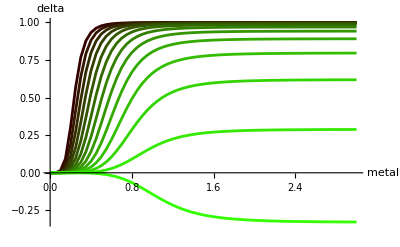

```mathematica
TRYparam={0.3,1,5,1,5};
Clear[delta]
For[TRYc=0,TRYc≤3,TRYc=TRYc+1/20,
For[TRYa=-3,TRYa≤3,TRYa=TRYa+1/2,
delta[TRYc,TRYa]=Chop[1-2 findY[{TRYc,TRYc},TRYparam,TRYa]/(findY[{TRYc,0},TRYparam,TRYa]+findY[{0,TRYc},TRYparam,TRYa])]
]
]
Table[delta[3,a],{a,-3,3,1/2}]
Show[Table[
ListPlot[Table[{c,delta[c,a]},{c,0,3,1/20}],Joined->True,PlotStyle->RGBColor[0.2,(a+3)/6,0]],{a,-3,3,1/2}],
AxesLabel->{"metal","delta"},PlotRange->All
]
```

```mathematica
Table[{N[a],RGBColor[0.2,(a+3)/6,0]},{a,-3,3,1/2}]//MatrixForm
```

(-3. | RGBColor[0.2, 0, 0]
-2.5 | RGBColor[0.2, Rational[1, 12], 0]
-2. | RGBColor[0.2, Rational[1, 6], 0]
-1.5 | RGBColor[0.2, Rational[1, 4], 0]
-1. | RGBColor[0.2, Rational[1, 3], 0]
-0.5 | RGBColor[0.2, Rational[5, 12], 0]
0. | RGBColor[0.2, Rational[1, 2], 0]
0.5 | RGBColor[0.2, Rational[7, 12], 0]
1. | RGBColor[0.2, Rational[2, 3], 0]
1.5 | RGBColor[0.2, Rational[3, 4], 0]
2. | RGBColor[0.2, Rational[5, 6], 0]
2.5 | RGBColor[0.2, Rational[11, 12], 0]
3. | RGBColor[0.2, 1, 0])

Smaller βs

{0.971201,0.960662,0.946278,0.926658,0.899916,0.863503,0.813992,0.746799,0.655843,0.533146,0.368407,0.148606,-0.142213}

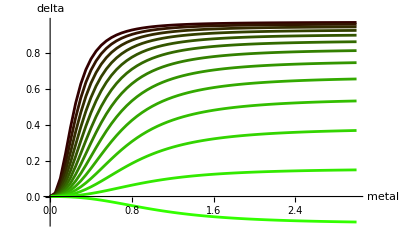

```mathematica
TRYparam={0.3,1,2.5,1,2.5};
Clear[delta]
For[TRYc=0,TRYc≤3,TRYc=TRYc+1/20,
For[TRYa=-3,TRYa≤3,TRYa=TRYa+1/2,
delta[TRYc,TRYa]=Chop[1-2 findY[{TRYc,TRYc},TRYparam,TRYa]/(findY[{TRYc,0},TRYparam,TRYa]+findY[{0,TRYc},TRYparam,TRYa])]
]
]
Table[delta[3,a],{a,-3,3,1/2}]
Show[Table[
ListPlot[Table[{c,delta[c,a]},{c,0,3,1/20}],Joined->True,PlotStyle->RGBColor[0.2,(a+3)/6,0]],{a,-3,3,1/2}],
AxesLabel->{"metal","delta"},PlotRange->All
]
```

Different βs

Power::infy: Infinite expression 1/0. encountered.

{0.998427,0.997262,0.995264,0.991861,0.986108,0.976457,0.960392,0.933873,0.890473,0.820099,0.707127,0.527808,0.2469}

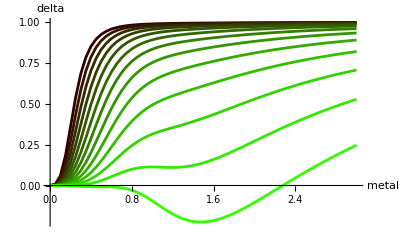

```mathematica
TRYparam={0.3,1,2.5,1,5};
Clear[delta]
For[TRYc=0,TRYc≤3,TRYc=TRYc+1/20,
For[TRYa=-3,TRYa≤3,TRYa=TRYa+1/2,
delta[TRYc,TRYa]=Chop[1-2 findY[{TRYc,TRYc},TRYparam,TRYa]/(findY[{TRYc,0},TRYparam,TRYa]+findY[{0,TRYc},TRYparam,TRYa])]
]
]
Table[delta[3,a],{a,-3,3,1/2}]
Show[Table[
ListPlot[Table[{c,delta[c,a]},{c,0,3,1/20}],Joined->True,PlotStyle->RGBColor[0.2,(a+3)/6,0]],{a,-3,3,1/2}],
AxesLabel->{"metal","delta"},PlotRange->All
]
```

Measuring the metal concentrations relative to their EC50 (calling these y[i]) and the combined growth rate, Y, relative to max, there is no explicit solution for the predicted growth rate in the metal combination:

```mathematica
Solve[y[1]/(1/Y-1)^(1/β[1])+y[2]/(1/Y-1)^(1/β[2])==Exp[a (y[1]y[2])/(y[1]+y[2])^2],Y]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[(-1+1/Y)^(-1/β[1]) y[1]+(-1+1/Y)^(-1/β[2]) y[2]==ⅇ^((a y[1] y[2])/(y[1]+y[2])^2),Y]

There is if the metals have the same β:

```mathematica
Simplify[Solve[y[1]/(1/Y-1)^(1/β)+y[2]/(1/Y-1)^(1/β)==Exp[a (y[1]y[2])/(y[1]+y[2])^2],Y]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Y→1/(1+(ⅇ^(-(a y[1] y[2])/(y[1]+y[2])^2) (y[1]+y[2]))^β)}}

```mathematica
Simplify[Solve[c[1]/((max/Y-1)^(1/β) EC50[1])+c[2]/((max/Y-1)^(1/β) EC50[2])==Exp[a (c[1]/EC50[1] c[2]/EC50[2])/(c[1]/EC50[1]+c[2]/EC50[2])^2],Y]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Y→max/(1+((ⅇ^(-(a c[1] c[2] EC50[1] EC50[2])/(c[2] EC50[1]+c[1] EC50[2])^2) (c[2] EC50[1]+c[1] EC50[2]))/(EC50[1] EC50[2]))^β)}}

Thus, we can predict delta if the beta’s were similar.

```mathematica
Simplify[PowerExpand[1-2 (max/(1+((ⅇ^(-(a c[1] c[2] EC50[1] EC50[2])/(c[2] EC50[1]+c[1] EC50[2])^2) (c[2] EC50[1]+c[1] EC50[2]))/(EC50[1] EC50[2]))^β))/(max/(1+(c[1]/EC50[1])^β)+max/(1+(c[2]/EC50[2])^β))]]
```

1-2/((1+ⅇ^(-(a β c[1] c[2] EC50[1] EC50[2])/(c[2] EC50[1]+c[1] EC50[2])^2) EC50[1]^-β EC50[2]^-β (c[2] EC50[1]+c[1] EC50[2])^β) (EC50[1]^β/(c[1]^β+EC50[1]^β)+EC50[2]^β/(c[2]^β+EC50[2]^β)))

Measuring the metal concentrations relative to their EC50 and setting the metals at an equal concentration relative to EC50:

```mathematica
Simplify[PowerExpand[%/.c[1]->c*EC50[1]/.c[2]->c*EC50[2]]]
```

(c^β (2^β-ⅇ^((a β)/4)))/(2^β c^β+ⅇ^((a β)/4))

Assuming c is large (to get the asymptote), we get: 1-2^-β ⅇ^((a β)/4) or equivalently  1-(ⅇ^(a/4)/2)^β

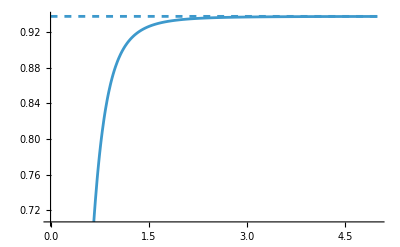

```mathematica
Show[
Plot[(c^β (2^β-ⅇ^((a β)/4)))/(2^β c^β+ⅇ^((a β)/4))/.a->0/.β->4,{c,0,5}],
Plot[1-1/(2^β  ⅇ^(-(a β)/4))/.a->0/.β->4,{c,0,5},PlotStyle->Dashed]
]
```

With the proportional distance to the optimum equal to  1/(ⅇ^(-(a β)/4+ β Log[2 c])-1):

```mathematica
((1-1/(2^β  ⅇ^(-(a β)/4)))-((c^β (2^β-ⅇ^((a β)/4)))/(2^β c^β+ⅇ^((a β)/4))))/(1-1/(2^β  ⅇ^(-(a β)/4)))//Simplify
```

ⅇ^((a β)/4)/(2^β c^β+ⅇ^((a β)/4))

#### Functions for the likelihood & sum of squares

Expected growth, Y, in two metals at concentration c1 and c2 for a given value of interaction (a):

```mathematica
Clear[fitfindY]
fitfindY[max_?NumericQ,EC501_?NumericQ,β1_?NumericQ,EC502_?NumericQ,β2_?NumericQ,a_?NumericQ,0,0]:=findY[max,EC501,β1,EC502,β2,a,0,0]=max;

fitfindY[max_?NumericQ,EC501_?NumericQ,β1_?NumericQ,EC502_?NumericQ,β2_?NumericQ,a_?NumericQ,c1_?NumericQ,c2_?NumericQ]:=findY[max,EC501,β1,EC502,β2,a,c1,c2]=
Chop[Y/.FindRoot[c1/((max/Y-1)^(1/β1) EC501)+c2/((max/Y-1)^(1/β2) EC502)-Exp[a (c1/EC501 c2/EC502)/(c1/EC501+c2/EC502)^2]==0,{Y,1/10},WorkingPrecision->100]]
```

[?NumericQ was needed in the FindRoot command for Y for the FindMinimum search below to work, avoiding cases where the search returned non-numeric values.]

If a = 0, we can use:

```mathematica
fitfindY[max_?NumericQ,EC501_?NumericQ,β1_?NumericQ,EC502_?NumericQ,β2_?NumericQ,0,0]:=findY[max,EC501,β1,EC502,β2,0,0]=max;

fitfindY[max_?NumericQ,EC501_?NumericQ,β1_?NumericQ,EC502_?NumericQ,β2_?NumericQ,c1_?NumericQ,c2_?NumericQ]:=findY[max,EC501,β1,EC502,β2,c1,c2]=
Chop[Y/.FindRoot[c1/((max/Y-1)^(1/β1) EC501)+c2/((max/Y-1)^(1/β2) EC502)==1,{Y,1/10},WorkingPrecision->100]]
```

The sum of squared differences between the observed and expected growth:

```mathematica
Clear[sumofsquares]
sumofsquares[max_?NumericQ,EC501_?NumericQ,β1_?NumericQ,EC502_?NumericQ,β2_?NumericQ,a_?NumericQ,data_]:=sumofsquares[max,EC501,β1,EC502,β2,a,data]=
Chop[
Sum[(data[[i,3]]-fitfindY[max,EC501,β1,EC502,β2,a,data[[i,1]],data[[i,2]]])^2,{i,1,Length[data]}]]
```

If a = 0, we can use:

```mathematica
sumofsquares[max_?NumericQ,EC501_?NumericQ,β1_?NumericQ,EC502_?NumericQ,β2_?NumericQ,data_]:=sumofsquares[max,EC501,β1,EC502,β2,data]=
Chop[
Sum[(data[[i,3]]-fitfindY[max,EC501,β1,EC502,β2,data[[i,1]],data[[i,2]]])^2,{i,1,Length[data]}]]
```

Assuming that the deviation is normally distributed around the predicted combination fitness (Y) with a constant σ:

```mathematica
FullSimplify[Log[PDF[NormalDistribution[Y,σ],x]],{x>0,Y>0,σ>0}]
```

-(x-Y)^2/(2 σ^2)-1/2 Log[2 π]+Log[1/σ]

```mathematica
Clear[lnlikelihood]
lnlikelihood[max_?NumericQ,EC501_?NumericQ,β1_?NumericQ,EC502_?NumericQ,β2_?NumericQ,a_?NumericQ,σ_?NumericQ,data_]:=lnlikelihood[max,EC501,β1,EC502,β2,a,σ,data]=Chop[
Sum[-(data[[i,3]]-fitfindY[max,EC501,β1,EC502,β2,a,data[[i,1]],data[[i,2]]])^2/(2 σ^2)-1/2 Log[2 π]+Log[1/σ],{i,1,Length[data]}]]
```

If a = 0, we can use:

```mathematica
lnlikelihood[max_?NumericQ,EC501_?NumericQ,β1_?NumericQ,EC502_?NumericQ,β2_?NumericQ,σ_?NumericQ,data_]:=lnlikelihood[max,EC501,β1,EC502,β2,σ,data]=Chop[
Sum[-(data[[i,3]]-fitfindY[max,EC501,β1,EC502,β2,data[[i,1]],data[[i,2]]])^2/(2 σ^2)-1/2 Log[2 π]+Log[1/σ],{i,1,Length[data]}]]
```

#### CdCo growth data: a = -0.16 NS

```mathematica
ypad="YPAD";
single1="Cd";
single2="Co";
double="CdCo";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,0.344675},{0,0,0.342987},{0,0,0.346982},{0,0,0.341592},{0,0,0.327645},{0,0,0.299649},{0,0,0.3333},{0,0,0.30274},{0,0,0.286864},{0,0,0.347208}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,0,0.273043},{0.008,0,0.267291},{0.011,0,0.250546},{0.011,0,0.229222},{0.017,0,0.218167},{0.017,0,0.221917},{0.026,0,0.077551},{0.026,0,0.0891747},{0.038,0,0.0765231},{0.038,0,0.0725543},{0.005,0,0.264267},{0.005,0,0.291587},{0.01,0,0.272103},{0.01,0,0.262951},{0.016,0,0.230977},{0.016,0,0.22176},{0.022,0,0.0631486},{0.022,0,0.159048},{0.027,0,0.0724519},{0.027,0,0.0938391}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0.7,0.280117},{0,0.7,0.28456},{0,0.86,0.241364},{0,0.86,0.255618},{0,1.,0.10552},{0,1.,0.130922},{0,1.32,0.102152},{0,1.32,0.0936645},{0,2.05,0.0312513},{0,2.05,0.0169948},{0,0.5,0.268174},{0,0.5,0.26661},{0,0.85,0.20741},{0,0.85,0.20144},{0,0.9,0.135898},{0,0.9,0.127819},{0,0.95,0.102088},{0,0.95,0.0936526},{0,1.3,0.0237777},{0,1.3,0.0523439}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,0.7,0.116758},{0.008,0.7,0.128962},{0.008,0.7,0.1315},{0.011,0.86,0.129677},{0.011,0.86,0.122541},{0.011,0.86,0.145089},{0.017,1.,0.0588871},{0.017,1.,0.0581486},{0.017,1.,0.0318858},{0.026,1.32,0.0561758},{0.026,1.32,0.0441993},{0.026,1.32,0.0394771},{0.038,2.05,0.0459534},{0.038,2.05,0.0465959},{0.038,2.05,0.0474358},{0.005,0.5,0.110043},{0.005,0.5,0.12136},{0.005,0.5,0.120218},{0.01,0.85,0.116913},{0.01,0.85,0.11975},{0.01,0.85,0.137763},{0.016,0.9,0.0434922},{0.016,0.9,0.0813243},{0.016,0.9,0.0605342},{0.022,0.95,0.0426563},{0.022,0.95,0.033369},{0.022,0.95,0.0290142},{0.027,1.3,0.030259},{0.027,1.3,0.0334902},{0.027,1.3,0.0293521}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.011 | 0.011 | 0.017 | 0.017 | 0.026 | 0.026 | 0.038 | 0.038 | 0.005 | 0.005 | 0.01 | 0.01 | 0.016 | 0.016 | 0.022 | 0.022 | 0.027 | 0.027 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.008 | 0.011 | 0.011 | 0.011 | 0.017 | 0.017 | 0.017 | 0.026 | 0.026 | 0.026 | 0.038 | 0.038 | 0.038 | 0.005 | 0.005 | 0.005 | 0.01 | 0.01 | 0.01 | 0.016 | 0.016 | 0.016 | 0.022 | 0.022 | 0.022 | 0.027 | 0.027 | 0.027
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.86 | 0.86 | 1. | 1. | 1.32 | 1.32 | 2.05 | 2.05 | 0.5 | 0.5 | 0.85 | 0.85 | 0.9 | 0.9 | 0.95 | 0.95 | 1.3 | 1.3 | 0.7 | 0.7 | 0.7 | 0.86 | 0.86 | 0.86 | 1. | 1. | 1. | 1.32 | 1.32 | 1.32 | 2.05 | 2.05 | 2.05 | 0.5 | 0.5 | 0.5 | 0.85 | 0.85 | 0.85 | 0.9 | 0.9 | 0.9 | 0.95 | 0.95 | 0.95 | 1.3 | 1.3 | 1.3
0.344675 | 0.342987 | 0.346982 | 0.341592 | 0.327645 | 0.299649 | 0.3333 | 0.30274 | 0.286864 | 0.347208 | 0.273043 | 0.267291 | 0.250546 | 0.229222 | 0.218167 | 0.221917 | 0.077551 | 0.0891747 | 0.0765231 | 0.0725543 | 0.264267 | 0.291587 | 0.272103 | 0.262951 | 0.230977 | 0.22176 | 0.0631486 | 0.159048 | 0.0724519 | 0.0938391 | 0.280117 | 0.28456 | 0.241364 | 0.255618 | 0.10552 | 0.130922 | 0.102152 | 0.0936645 | 0.0312513 | 0.0169948 | 0.268174 | 0.26661 | 0.20741 | 0.20144 | 0.135898 | 0.127819 | 0.102088 | 0.0936526 | 0.0237777 | 0.0523439 | 0.116758 | 0.128962 | 0.1315 | 0.129677 | 0.122541 | 0.145089 | 0.0588871 | 0.0581486 | 0.0318858 | 0.0561758 | 0.0441993 | 0.0394771 | 0.0459534 | 0.0465959 | 0.0474358 | 0.110043 | 0.12136 | 0.120218 | 0.116913 | 0.11975 | 0.137763 | 0.0434922 | 0.0813243 | 0.0605342 | 0.0426563 | 0.033369 | 0.0290142 | 0.030259 | 0.0334902 | 0.0293521)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{0.008,0.273043},{0.008,0.267291},{0.011,0.250546},{0.011,0.229222},{0.017,0.218167},{0.017,0.221917},{0.026,0.077551},{0.026,0.0891747},{0.038,0.0765231},{0.038,0.0725543},{0.005,0.264267},{0.005,0.291587},{0.01,0.272103},{0.01,0.262951},{0.016,0.230977},{0.016,0.22176},{0.022,0.0631486},{0.022,0.159048},{0.027,0.0724519},{0.027,0.0938391}}

{max→0.320975,EC501→0.0192771,β1→2.37242}

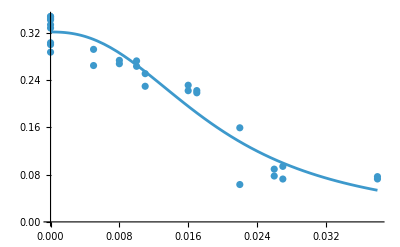

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{0.7,0.280117},{0.7,0.28456},{0.86,0.241364},{0.86,0.255618},{1.,0.10552},{1.,0.130922},{1.32,0.102152},{1.32,0.0936645},{2.05,0.0312513},{2.05,0.0169948},{0.5,0.268174},{0.5,0.26661},{0.85,0.20741},{0.85,0.20144},{0.9,0.135898},{0.9,0.127819},{0.95,0.102088},{0.95,0.0936526},{1.3,0.0237777},{1.3,0.0523439}}

{max→0.324288,EC502→0.919324,β2→4.68106}

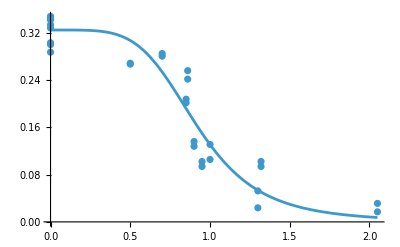

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{0.322632,0.0192771,2.37242,0.919324,4.68106}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

0.122384

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{0.0974726,{max→0.327272,EC501→0.0185913,β1→1.76069,EC502→0.903581,β2→2.83584}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{154.893,{max→0.327273,EC501→0.0185913,β1→1.76069,EC502→0.903581,β2→2.83584,σ→0.0349057}}

Here the fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.0000441305,0.0000652631,0.000108395,0.0000368715,0.0000471279}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{0.0971476,{max→0.328003,EC501→0.0187363,β1→1.72707,EC502→0.907712,β2→2.75701,a→-0.162074}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

FindMaximum::nrnum: The function value 232741.-379588. ⅈ is not a real number at {max,EC501,β1,EC502,β2,a,σ} = {0.34733,0.0168282,0.0237242,0.895666,4.02968,-0.0553816,0.0296125}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

{155.027,{max→0.328003,EC501→0.0187363,β1→1.72706,EC502→0.907711,β2→2.757,a→-0.162076,σ→0.0348474}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-0.0000628254,0.0000810259,0.000166776,0.0000478175,0.0000864611,-0.000922239}

Testing whether adding the parameter “a” significantly improves the fit:

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841. This is NOT SIGNIFICANT:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

0.605188

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.108277,0.321773,0.492742,0.598343,0.661048,0.700072,0.726315,0.745425,0.760312,0.772524}

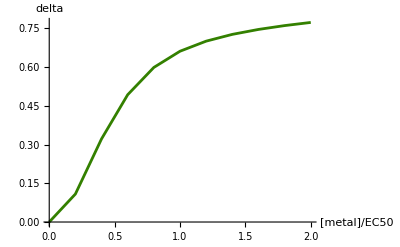

```mathematica
Clear[delta]
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

-0.162076

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

0.0187363

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

0.907711

#### CdCu growth data: a = -1.59**

```mathematica
ypad="YPAD";
single1="Cd";
single2="Cu";
double="CdCu";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,0.344675},{0,0,0.342987},{0,0,0.346982},{0,0,0.341592},{0,0,0.327645},{0,0,0.299649},{0,0,0.3333},{0,0,0.30274},{0,0,0.286864},{0,0,0.347208}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,0,0.273043},{0.008,0,0.267291},{0.011,0,0.250546},{0.011,0,0.229222},{0.017,0,0.218167},{0.017,0,0.221917},{0.026,0,0.077551},{0.026,0,0.0891747},{0.038,0,0.0765231},{0.038,0,0.0725543},{0.005,0,0.264267},{0.005,0,0.291587},{0.01,0,0.272103},{0.01,0,0.262951},{0.016,0,0.230977},{0.016,0,0.22176},{0.022,0,0.0631486},{0.022,0,0.159048},{0.027,0,0.0724519},{0.027,0,0.0938391}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,8.83,0.259677},{0,8.83,0.238123},{0,10.17,0.217344},{0,10.17,0.180045},{0,10.83,0.160271},{0,10.83,0.171678},{0,12.,0.166475},{0,12.,0.204235},{0,13.5,0.00481236},{0,13.5,0.0423212},{0,4.,0.18923},{0,4.,0.250912},{0,8.83,0.185402},{0,8.83,0.203011},{0,10.17,0.114962},{0,10.17,0.115593},{0,10.85,0.163957},{0,10.85,0.134471},{0,12.9,0.00979951},{0,12.9,0.0099776}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,8.83,0.0961073},{0.008,8.83,0.10876},{0.008,8.83,0.0902524},{0.011,10.17,0.107024},{0.011,10.17,0.109526},{0.011,10.17,0.127808},{0.017,10.83,0.0121224},{0.017,10.83,0.128737},{0.017,10.83,0.048089},{0.026,12.,0.0397929},{0.026,12.,0.00819978},{0.026,12.,0.0326658},{0.038,13.5,0.00646257},{0.038,13.5,0.0439212},{0.038,13.5,0.0234566},{0.005,4.,0.101178},{0.005,4.,0.123983},{0.005,4.,0.124719},{0.01,8.83,0.0853488},{0.01,8.83,0.0991435},{0.01,8.83,0.0980182},{0.016,10.17,0.0564587},{0.016,10.17,0.014127},{0.016,10.17,0.0555038},{0.022,10.85,0.0135138},{0.022,10.85,0.00447037},{0.022,10.85,0.0123879},{0.027,12.9,0.011382},{0.027,12.9,0.00505251},{0.027,12.9,0.00590193}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.011 | 0.011 | 0.017 | 0.017 | 0.026 | 0.026 | 0.038 | 0.038 | 0.005 | 0.005 | 0.01 | 0.01 | 0.016 | 0.016 | 0.022 | 0.022 | 0.027 | 0.027 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.008 | 0.011 | 0.011 | 0.011 | 0.017 | 0.017 | 0.017 | 0.026 | 0.026 | 0.026 | 0.038 | 0.038 | 0.038 | 0.005 | 0.005 | 0.005 | 0.01 | 0.01 | 0.01 | 0.016 | 0.016 | 0.016 | 0.022 | 0.022 | 0.022 | 0.027 | 0.027 | 0.027
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.83 | 8.83 | 10.17 | 10.17 | 10.83 | 10.83 | 12. | 12. | 13.5 | 13.5 | 4. | 4. | 8.83 | 8.83 | 10.17 | 10.17 | 10.85 | 10.85 | 12.9 | 12.9 | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.83 | 10.83 | 10.83 | 12. | 12. | 12. | 13.5 | 13.5 | 13.5 | 4. | 4. | 4. | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.85 | 10.85 | 10.85 | 12.9 | 12.9 | 12.9
0.344675 | 0.342987 | 0.346982 | 0.341592 | 0.327645 | 0.299649 | 0.3333 | 0.30274 | 0.286864 | 0.347208 | 0.273043 | 0.267291 | 0.250546 | 0.229222 | 0.218167 | 0.221917 | 0.077551 | 0.0891747 | 0.0765231 | 0.0725543 | 0.264267 | 0.291587 | 0.272103 | 0.262951 | 0.230977 | 0.22176 | 0.0631486 | 0.159048 | 0.0724519 | 0.0938391 | 0.259677 | 0.238123 | 0.217344 | 0.180045 | 0.160271 | 0.171678 | 0.166475 | 0.204235 | 0.00481236 | 0.0423212 | 0.18923 | 0.250912 | 0.185402 | 0.203011 | 0.114962 | 0.115593 | 0.163957 | 0.134471 | 0.00979951 | 0.0099776 | 0.0961073 | 0.10876 | 0.0902524 | 0.107024 | 0.109526 | 0.127808 | 0.0121224 | 0.128737 | 0.048089 | 0.0397929 | 0.00819978 | 0.0326658 | 0.00646257 | 0.0439212 | 0.0234566 | 0.101178 | 0.123983 | 0.124719 | 0.0853488 | 0.0991435 | 0.0980182 | 0.0564587 | 0.014127 | 0.0555038 | 0.0135138 | 0.00447037 | 0.0123879 | 0.011382 | 0.00505251 | 0.00590193)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{0.008,0.273043},{0.008,0.267291},{0.011,0.250546},{0.011,0.229222},{0.017,0.218167},{0.017,0.221917},{0.026,0.077551},{0.026,0.0891747},{0.038,0.0765231},{0.038,0.0725543},{0.005,0.264267},{0.005,0.291587},{0.01,0.272103},{0.01,0.262951},{0.016,0.230977},{0.016,0.22176},{0.022,0.0631486},{0.022,0.159048},{0.027,0.0724519},{0.027,0.0938391}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→0.320975,EC501→0.0192771,β1→2.37242}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{8.83,0.259677},{8.83,0.238123},{10.17,0.217344},{10.17,0.180045},{10.83,0.160271},{10.83,0.171678},{12.,0.166475},{12.,0.204235},{13.5,0.00481236},{13.5,0.0423212},{4.,0.18923},{4.,0.250912},{8.83,0.185402},{8.83,0.203011},{10.17,0.114962},{10.17,0.115593},{10.85,0.163957},{10.85,0.134471},{12.9,0.00979951},{12.9,0.0099776}}

{max→0.308914,EC502→10.5473,β2→5.84653}

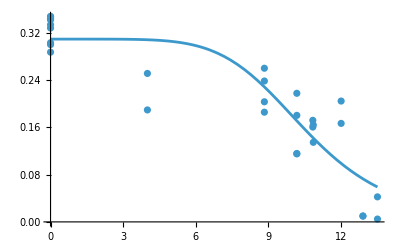

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{0.314945,0.0192771,2.37242,10.5473,5.84653}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

0.176233

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{0.146559,{max→0.315872,EC501→0.0187955,β1→2.6387,EC502→8.68197,β2→1.60468}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{138.579,{max→0.315872,EC501→0.0187955,β1→2.6387,EC502→8.68196,β2→1.60468,σ→0.0428017}}

Here the fits aren’t compatible as there is a ridge that is hard to search:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.0000237111,0.0000328311,0.0000723272,0.0000359042,0.0000539051}

Seeing if we get a better sumofsquares fit if starting at the lnlikelihood fit:

```mathematica
FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,max/.maxll[[2]]},{EC501,EC501/.maxll[[2]]},{β1,β1/.maxll[[2]]},{EC502,EC502/.maxll[[2]]},{β2,β2/.maxll[[2]]}}]
```

{0.146559,{max→0.315872,EC501→0.0187955,β1→2.6387,EC502→8.68197,β2→1.60468}}

This is a better sum of squares and is closer to the ML fit:

```mathematica
100(({max,EC501,β1,EC502,β2}/.%[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.0000237141,0.0000328276,0.0000723649,0.0000359003,0.0000538709}

Seeing if we get a better lnlikelihood fit if starting at the sumofsquares fit:

```mathematica
FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,max/.ssq[[2]]},{EC501,EC501/.ssq[[2]]},{β1,β1/.ssq[[2]]},{EC502,EC502/.ssq[[2]]},{β2,β2/.ssq[[2]]},{σ,0.01,0,1}}]
```

{138.579,{max→0.315872,EC501→0.0187955,β1→2.6387,EC502→8.68196,β2→1.60468,σ→0.0428017}}

This is a lower likelihood (worse fit).

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{0.131552,{max→0.322252,EC501→0.0192657,β1→2.22338,EC502→9.02651,β2→1.28623,a→-1.58679}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

FindMaximum::nrnum: The function value -23770.5-6455.52 ⅈ is not a real number at {max,EC501,β1,EC502,β2,a,σ} = {0.336073,0.0166534,0.0614309,10.3,5.19358,-0.903421,0.039286}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

{142.9,{max→0.322252,EC501→0.0192657,β1→2.22337,EC502→9.0265,β2→1.28623,a→-1.5868,σ→0.0405512}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-0.0000452149,0.0000504646,0.000139918,0.000062591,0.000167604,-0.000267903}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841, which it is:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

0.00328525

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction, the fit is much better:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.251171,0.479401,0.60988,0.683624,0.728217,0.757483,0.77824,0.793967,0.806523,0.816954}

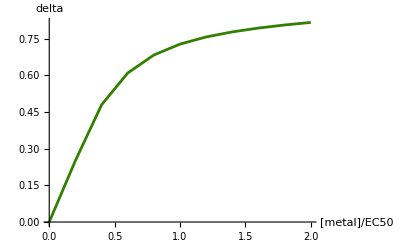

```mathematica
Clear[delta]
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

-1.5868

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

0.0192657

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

9.0265

#### CdMn growth data: a = 1.25*** - Delta at EC50 is 0.48 from the model fit

```mathematica
ypad="YPAD";
single1="Cd";
single2="Mn";
double="CdMn";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,0.344675},{0,0,0.342987},{0,0,0.346982},{0,0,0.341592},{0,0,0.327645},{0,0,0.299649},{0,0,0.3333},{0,0,0.30274},{0,0,0.286864},{0,0,0.347208}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,0,0.273043},{0.008,0,0.267291},{0.011,0,0.250546},{0.011,0,0.229222},{0.017,0,0.218167},{0.017,0,0.221917},{0.026,0,0.077551},{0.026,0,0.0891747},{0.038,0,0.0765231},{0.038,0,0.0725543},{0.005,0,0.264267},{0.005,0,0.291587},{0.01,0,0.272103},{0.01,0,0.262951},{0.016,0,0.230977},{0.016,0,0.22176},{0.022,0,0.0631486},{0.022,0,0.159048},{0.027,0,0.0724519},{0.027,0,0.0938391}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0.86,0.298582},{0,0.86,0.291635},{0,1.14,0.204455},{0,1.14,0.185045},{0,1.31,0.131089},{0,1.31,0.132071},{0,1.66,0.07621},{0,1.66,0.101139},{0,2.23,0.0603872},{0,2.23,0.0464464},{0,0.85,0.29107},{0,0.85,0.248948},{0,1.,0.193578},{0,1.,0.195635},{0,1.14,0.151442},{0,1.14,0.108769},{0,1.25,0.098664},{0,1.25,0.0744238},{0,1.6,0.045561},{0,1.6,0.057657}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,0.86,0.21557},{0.008,0.86,0.244674},{0.008,0.86,0.176642},{0.011,1.14,0.145319},{0.011,1.14,0.120858},{0.011,1.14,0.131116},{0.017,1.31,0.0864283},{0.017,1.31,0.102225},{0.017,1.31,0.0798732},{0.026,1.66,0.0727725},{0.026,1.66,0.0455441},{0.026,1.66,0.0568061},{0.038,2.23,0.0170835},{0.038,2.23,0.0387021},{0.038,2.23,0.0591685},{0.005,0.85,0.189521},{0.005,0.85,0.231975},{0.005,0.85,0.193645},{0.01,1.,0.134761},{0.01,1.,0.112684},{0.01,1.,0.144871},{0.016,1.14,0.0892047},{0.016,1.14,0.105972},{0.016,1.14,0.0743584},{0.022,1.25,0.0623472},{0.022,1.25,0.0530437},{0.022,1.25,0.0676314},{0.027,1.6,0.0294608},{0.027,1.6,0.0336647},{0.027,1.6,0.0281347}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.011 | 0.011 | 0.017 | 0.017 | 0.026 | 0.026 | 0.038 | 0.038 | 0.005 | 0.005 | 0.01 | 0.01 | 0.016 | 0.016 | 0.022 | 0.022 | 0.027 | 0.027 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.008 | 0.011 | 0.011 | 0.011 | 0.017 | 0.017 | 0.017 | 0.026 | 0.026 | 0.026 | 0.038 | 0.038 | 0.038 | 0.005 | 0.005 | 0.005 | 0.01 | 0.01 | 0.01 | 0.016 | 0.016 | 0.016 | 0.022 | 0.022 | 0.022 | 0.027 | 0.027 | 0.027
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86 | 0.86 | 1.14 | 1.14 | 1.31 | 1.31 | 1.66 | 1.66 | 2.23 | 2.23 | 0.85 | 0.85 | 1. | 1. | 1.14 | 1.14 | 1.25 | 1.25 | 1.6 | 1.6 | 0.86 | 0.86 | 0.86 | 1.14 | 1.14 | 1.14 | 1.31 | 1.31 | 1.31 | 1.66 | 1.66 | 1.66 | 2.23 | 2.23 | 2.23 | 0.85 | 0.85 | 0.85 | 1. | 1. | 1. | 1.14 | 1.14 | 1.14 | 1.25 | 1.25 | 1.25 | 1.6 | 1.6 | 1.6
0.344675 | 0.342987 | 0.346982 | 0.341592 | 0.327645 | 0.299649 | 0.3333 | 0.30274 | 0.286864 | 0.347208 | 0.273043 | 0.267291 | 0.250546 | 0.229222 | 0.218167 | 0.221917 | 0.077551 | 0.0891747 | 0.0765231 | 0.0725543 | 0.264267 | 0.291587 | 0.272103 | 0.262951 | 0.230977 | 0.22176 | 0.0631486 | 0.159048 | 0.0724519 | 0.0938391 | 0.298582 | 0.291635 | 0.204455 | 0.185045 | 0.131089 | 0.132071 | 0.07621 | 0.101139 | 0.0603872 | 0.0464464 | 0.29107 | 0.248948 | 0.193578 | 0.195635 | 0.151442 | 0.108769 | 0.098664 | 0.0744238 | 0.045561 | 0.057657 | 0.21557 | 0.244674 | 0.176642 | 0.145319 | 0.120858 | 0.131116 | 0.0864283 | 0.102225 | 0.0798732 | 0.0727725 | 0.0455441 | 0.0568061 | 0.0170835 | 0.0387021 | 0.0591685 | 0.189521 | 0.231975 | 0.193645 | 0.134761 | 0.112684 | 0.144871 | 0.0892047 | 0.105972 | 0.0743584 | 0.0623472 | 0.0530437 | 0.0676314 | 0.0294608 | 0.0336647 | 0.0281347)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{0.008,0.273043},{0.008,0.267291},{0.011,0.250546},{0.011,0.229222},{0.017,0.218167},{0.017,0.221917},{0.026,0.077551},{0.026,0.0891747},{0.038,0.0765231},{0.038,0.0725543},{0.005,0.264267},{0.005,0.291587},{0.01,0.272103},{0.01,0.262951},{0.016,0.230977},{0.016,0.22176},{0.022,0.0631486},{0.022,0.159048},{0.027,0.0724519},{0.027,0.0938391}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→0.320975,EC501→0.0192771,β1→2.37242}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{0.86,0.298582},{0.86,0.291635},{1.14,0.204455},{1.14,0.185045},{1.31,0.131089},{1.31,0.132071},{1.66,0.07621},{1.66,0.101139},{2.23,0.0603872},{2.23,0.0464464},{0.85,0.29107},{0.85,0.248948},{1.,0.193578},{1.,0.195635},{1.14,0.151442},{1.14,0.108769},{1.25,0.098664},{1.25,0.0744238},{1.6,0.045561},{1.6,0.057657}}

{max→0.330552,EC502→1.14189,β2→4.37898}

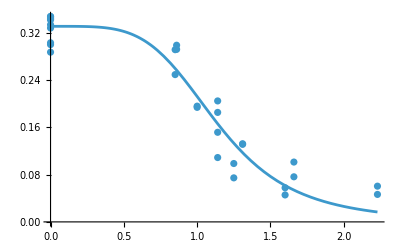

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{0.325763,0.0192771,2.37242,1.14189,4.37898}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

0.139218

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{0.0918087,{max→0.330348,EC501→0.0212086,β1→1.53451,EC502→1.21799,β2→3.08694}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{157.288,{max→0.330348,EC501→0.0212085,β1→1.5345,EC502→1.21799,β2→3.08694,σ→0.0338764}}

The fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.0000493958,0.00006327,0.000143854,0.0000398741,0.0000175878}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{0.0576556,{max→0.326822,EC501→0.0189104,β1→2.08393,EC502→1.14787,β2→4.03383,a→1.25283}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

FindMaximum::nrnum: The function value 379.573-251.327 ⅈ is not a real number at {max,EC501,β1,EC502,β2,a,σ} = {0.31294,0.025205,1.97722,1.405,4.28231,3.04658,-0.0196507}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

{175.897,{max→0.326822,EC501→0.0189104,β1→2.08393,EC502→1.14787,β2→4.03383,a→1.25283,σ→0.0268458}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-0.0000557185,0.0000672133,0.000164039,0.0000290154,0.0000379834,0.0000291337}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841, which it is:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

1.05654×10^-9

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction, the fit is much better:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.0221285,0.125122,0.278295,0.406751,0.487304,0.536691,0.572884,0.604427,0.633824,0.661363}

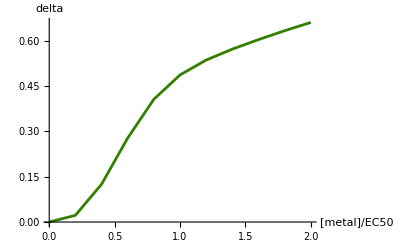

```mathematica
Clear[delta]
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

1.25283

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

0.0189104

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

1.14787

#### CdNi growth data: a = 0.87*** - Delta at EC50 is 0.67 from the model fit

```mathematica
ypad="YPAD";
single1="Cd";
single2="Ni";
double="CdNi";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,0.344675},{0,0,0.342987},{0,0,0.346982},{0,0,0.341592},{0,0,0.327645},{0,0,0.299649},{0,0,0.3333},{0,0,0.30274},{0,0,0.286864},{0,0,0.347208}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,0,0.273043},{0.008,0,0.267291},{0.011,0,0.250546},{0.011,0,0.229222},{0.017,0,0.218167},{0.017,0,0.221917},{0.026,0,0.077551},{0.026,0,0.0891747},{0.038,0,0.0765231},{0.038,0,0.0725543},{0.005,0,0.264267},{0.005,0,0.291587},{0.01,0,0.272103},{0.01,0,0.262951},{0.016,0,0.230977},{0.016,0,0.22176},{0.022,0,0.0631486},{0.022,0,0.159048},{0.027,0,0.0724519},{0.027,0,0.0938391}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,1.88,0.327391},{0,1.88,0.345335},{0,2.4,0.277617},{0,2.4,0.301498},{0,3.,0.161179},{0,3.,0.172964},{0,3.6,0.0728783},{0,3.6,0.0833834},{0,5.1,0.0532982},{0,5.1,0.0435607},{0,2.3,0.325228},{0,2.3,0.331102},{0,2.6,0.291454},{0,2.6,0.301508},{0,2.75,0.137243},{0,2.75,0.0999753},{0,3.,0.100496},{0,3.,0.0797609},{0,3.2,0.036418},{0,3.2,0.0401879}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,1.88,0.21113},{0.008,1.88,0.195747},{0.008,1.88,0.15358},{0.011,2.4,0.11932},{0.011,2.4,0.122707},{0.011,2.4,0.0969722},{0.017,3.,0.0714573},{0.017,3.,0.0524744},{0.017,3.,0.0775654},{0.026,3.6,0.0530364},{0.026,3.6,0.0438934},{0.026,3.6,0.0254383},{0.038,5.1,0.0223563},{0.038,5.1,0.016883},{0.038,5.1,0.042129},{0.005,2.3,0.208},{0.005,2.3,0.184065},{0.005,2.3,0.124119},{0.01,2.6,0.12545},{0.01,2.6,0.139656},{0.01,2.6,0.137469},{0.016,2.75,0.060493},{0.016,2.75,0.0695789},{0.016,2.75,0.0648063},{0.022,3.,0.0371165},{0.022,3.,0.046362},{0.022,3.,0.0320219},{0.027,3.2,0.0435},{0.027,3.2,0.0113343},{0.027,3.2,0.0126511}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.011 | 0.011 | 0.017 | 0.017 | 0.026 | 0.026 | 0.038 | 0.038 | 0.005 | 0.005 | 0.01 | 0.01 | 0.016 | 0.016 | 0.022 | 0.022 | 0.027 | 0.027 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.008 | 0.011 | 0.011 | 0.011 | 0.017 | 0.017 | 0.017 | 0.026 | 0.026 | 0.026 | 0.038 | 0.038 | 0.038 | 0.005 | 0.005 | 0.005 | 0.01 | 0.01 | 0.01 | 0.016 | 0.016 | 0.016 | 0.022 | 0.022 | 0.022 | 0.027 | 0.027 | 0.027
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.88 | 1.88 | 2.4 | 2.4 | 3. | 3. | 3.6 | 3.6 | 5.1 | 5.1 | 2.3 | 2.3 | 2.6 | 2.6 | 2.75 | 2.75 | 3. | 3. | 3.2 | 3.2 | 1.88 | 1.88 | 1.88 | 2.4 | 2.4 | 2.4 | 3. | 3. | 3. | 3.6 | 3.6 | 3.6 | 5.1 | 5.1 | 5.1 | 2.3 | 2.3 | 2.3 | 2.6 | 2.6 | 2.6 | 2.75 | 2.75 | 2.75 | 3. | 3. | 3. | 3.2 | 3.2 | 3.2
0.344675 | 0.342987 | 0.346982 | 0.341592 | 0.327645 | 0.299649 | 0.3333 | 0.30274 | 0.286864 | 0.347208 | 0.273043 | 0.267291 | 0.250546 | 0.229222 | 0.218167 | 0.221917 | 0.077551 | 0.0891747 | 0.0765231 | 0.0725543 | 0.264267 | 0.291587 | 0.272103 | 0.262951 | 0.230977 | 0.22176 | 0.0631486 | 0.159048 | 0.0724519 | 0.0938391 | 0.327391 | 0.345335 | 0.277617 | 0.301498 | 0.161179 | 0.172964 | 0.0728783 | 0.0833834 | 0.0532982 | 0.0435607 | 0.325228 | 0.331102 | 0.291454 | 0.301508 | 0.137243 | 0.0999753 | 0.100496 | 0.0797609 | 0.036418 | 0.0401879 | 0.21113 | 0.195747 | 0.15358 | 0.11932 | 0.122707 | 0.0969722 | 0.0714573 | 0.0524744 | 0.0775654 | 0.0530364 | 0.0438934 | 0.0254383 | 0.0223563 | 0.016883 | 0.042129 | 0.208 | 0.184065 | 0.124119 | 0.12545 | 0.139656 | 0.137469 | 0.060493 | 0.0695789 | 0.0648063 | 0.0371165 | 0.046362 | 0.0320219 | 0.0435 | 0.0113343 | 0.0126511)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{0.008,0.273043},{0.008,0.267291},{0.011,0.250546},{0.011,0.229222},{0.017,0.218167},{0.017,0.221917},{0.026,0.077551},{0.026,0.0891747},{0.038,0.0765231},{0.038,0.0725543},{0.005,0.264267},{0.005,0.291587},{0.01,0.272103},{0.01,0.262951},{0.016,0.230977},{0.016,0.22176},{0.022,0.0631486},{0.022,0.159048},{0.027,0.0724519},{0.027,0.0938391}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→0.320975,EC501→0.0192771,β1→2.37242}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{1.88,0.327391},{1.88,0.345335},{2.4,0.277617},{2.4,0.301498},{3.,0.161179},{3.,0.172964},{3.6,0.0728783},{3.6,0.0833834},{5.1,0.0532982},{5.1,0.0435607},{2.3,0.325228},{2.3,0.331102},{2.6,0.291454},{2.6,0.301508},{2.75,0.137243},{2.75,0.0999753},{3.,0.100496},{3.,0.0797609},{3.2,0.036418},{3.2,0.0401879}}

{max→0.333202,EC502→2.83132,β2→11.6297}

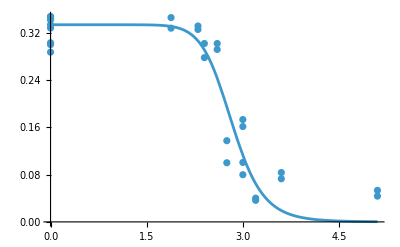

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{0.327088,0.0192771,2.37242,2.83132,11.6297}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

0.151184

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{0.108193,{max→0.337036,EC501→0.0209784,β1→1.26875,EC502→2.87686,β2→8.69416}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{150.72,{max→0.337036,EC501→0.0209784,β1→1.26875,EC502→2.87686,β2→8.69418,σ→0.0367751}}

The fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.000041037,0.0000351978,0.000216248,0.0000202944,-0.000246526}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{0.081791,{max→0.333466,EC501→0.0183195,β1→1.78464,EC502→2.83411,β2→9.99982,a→0.871355}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

FindMaximum::nrnum: The function value 503.801-251.327 ⅈ is not a real number at {max,EC501,β1,EC502,β2,a,σ} = {0.349771,0.0170905,1.50872,2.85099,9.91352,4.11059,-0.0228585}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

{161.91,{max→0.333466,EC501→0.0183195,β1→1.78463,EC502→2.83411,β2→9.99999,a→0.871358,σ→0.0319748}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{0.0000106021,5.60742×10^-6,0.000325004,0.0000201111,-0.00176029,-0.000324535}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841, which it is:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

2.23691×10^-6

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction, the fit is much better:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.0296212,0.159692,0.383081,0.591813,0.678848,0.71541,0.803114,0.883826,0.935182,0.964454}

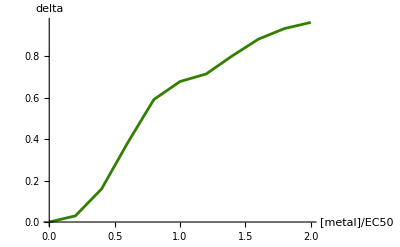

```mathematica
Clear[delta]
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

0.871358

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

0.0183195

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

2.83411

#### CdZn growth data: a = 0.20 NS - Delta at EC50 is 0.72 from the model fit

```mathematica
ypad="YPAD";
single1="Cd";
single2="Zn";
double="CdZn";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,0.344675},{0,0,0.342987},{0,0,0.346982},{0,0,0.341592},{0,0,0.327645},{0,0,0.299649},{0,0,0.3333},{0,0,0.30274},{0,0,0.286864},{0,0,0.347208}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,0,0.273043},{0.008,0,0.267291},{0.011,0,0.250546},{0.011,0,0.229222},{0.017,0,0.218167},{0.017,0,0.221917},{0.026,0,0.077551},{0.026,0,0.0891747},{0.038,0,0.0765231},{0.038,0,0.0725543},{0.005,0,0.264267},{0.005,0,0.291587},{0.01,0,0.272103},{0.01,0,0.262951},{0.016,0,0.230977},{0.016,0,0.22176},{0.022,0,0.0631486},{0.022,0,0.159048},{0.027,0,0.0724519},{0.027,0,0.0938391}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,4.,0.251828},{0,4.,0.24125},{0,4.75,0.21202},{0,4.75,0.224034},{0,5.4,0.161238},{0,5.4,0.17015},{0,6.,0.0966768},{0,6.,0.104308},{0,6.6,0.0368801},{0,6.6,0.0420288},{0,3.33,0.235142},{0,3.33,0.242968},{0,4.,0.206083},{0,4.,0.210944},{0,4.8,0.144694},{0,4.8,0.171222},{0,5.4,0.106978},{0,5.4,0.100649},{0,6.,0.0567384},{0,6.,0.0524779}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,4.,0.180027},{0.008,4.,0.112336},{0.008,4.,0.15934},{0.011,4.75,0.0741748},{0.011,4.75,0.111372},{0.011,4.75,0.0815067},{0.017,5.4,0.0311656},{0.017,5.4,0.0484335},{0.017,5.4,0.0579114},{0.026,6.,0.0302599},{0.026,6.,0.0482291},{0.026,6.,0.0409389},{0.038,6.6,0.00856265},{0.038,6.6,0.0137912},{0.038,6.6,0.0486238},{0.005,3.33,0.149251},{0.005,3.33,0.136437},{0.005,3.33,0.140535},{0.01,4.,0.0920683},{0.01,4.,0.122547},{0.01,4.,0.0832487},{0.016,4.8,0.0393673},{0.016,4.8,0.0648515},{0.016,4.8,0.0454831},{0.022,5.4,0.0187979},{0.022,5.4,0.020683},{0.022,5.4,0.0174343},{0.027,6.,0.0132532},{0.027,6.,0.0248217},{0.027,6.,0.0215477}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.011 | 0.011 | 0.017 | 0.017 | 0.026 | 0.026 | 0.038 | 0.038 | 0.005 | 0.005 | 0.01 | 0.01 | 0.016 | 0.016 | 0.022 | 0.022 | 0.027 | 0.027 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.008 | 0.011 | 0.011 | 0.011 | 0.017 | 0.017 | 0.017 | 0.026 | 0.026 | 0.026 | 0.038 | 0.038 | 0.038 | 0.005 | 0.005 | 0.005 | 0.01 | 0.01 | 0.01 | 0.016 | 0.016 | 0.016 | 0.022 | 0.022 | 0.022 | 0.027 | 0.027 | 0.027
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4. | 4. | 4.75 | 4.75 | 5.4 | 5.4 | 6. | 6. | 6.6 | 6.6 | 3.33 | 3.33 | 4. | 4. | 4.8 | 4.8 | 5.4 | 5.4 | 6. | 6. | 4. | 4. | 4. | 4.75 | 4.75 | 4.75 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6. | 6.6 | 6.6 | 6.6 | 3.33 | 3.33 | 3.33 | 4. | 4. | 4. | 4.8 | 4.8 | 4.8 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6.
0.344675 | 0.342987 | 0.346982 | 0.341592 | 0.327645 | 0.299649 | 0.3333 | 0.30274 | 0.286864 | 0.347208 | 0.273043 | 0.267291 | 0.250546 | 0.229222 | 0.218167 | 0.221917 | 0.077551 | 0.0891747 | 0.0765231 | 0.0725543 | 0.264267 | 0.291587 | 0.272103 | 0.262951 | 0.230977 | 0.22176 | 0.0631486 | 0.159048 | 0.0724519 | 0.0938391 | 0.251828 | 0.24125 | 0.21202 | 0.224034 | 0.161238 | 0.17015 | 0.0966768 | 0.104308 | 0.0368801 | 0.0420288 | 0.235142 | 0.242968 | 0.206083 | 0.210944 | 0.144694 | 0.171222 | 0.106978 | 0.100649 | 0.0567384 | 0.0524779 | 0.180027 | 0.112336 | 0.15934 | 0.0741748 | 0.111372 | 0.0815067 | 0.0311656 | 0.0484335 | 0.0579114 | 0.0302599 | 0.0482291 | 0.0409389 | 0.00856265 | 0.0137912 | 0.0486238 | 0.149251 | 0.136437 | 0.140535 | 0.0920683 | 0.122547 | 0.0832487 | 0.0393673 | 0.0648515 | 0.0454831 | 0.0187979 | 0.020683 | 0.0174343 | 0.0132532 | 0.0248217 | 0.0215477)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{0.008,0.273043},{0.008,0.267291},{0.011,0.250546},{0.011,0.229222},{0.017,0.218167},{0.017,0.221917},{0.026,0.077551},{0.026,0.0891747},{0.038,0.0765231},{0.038,0.0725543},{0.005,0.264267},{0.005,0.291587},{0.01,0.272103},{0.01,0.262951},{0.016,0.230977},{0.016,0.22176},{0.022,0.0631486},{0.022,0.159048},{0.027,0.0724519},{0.027,0.0938391}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→0.320975,EC501→0.0192771,β1→2.37242}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{4.,0.251828},{4.,0.24125},{4.75,0.21202},{4.75,0.224034},{5.4,0.161238},{5.4,0.17015},{6.,0.0966768},{6.,0.104308},{6.6,0.0368801},{6.6,0.0420288},{3.33,0.235142},{3.33,0.242968},{4.,0.206083},{4.,0.210944},{4.8,0.144694},{4.8,0.171222},{5.4,0.106978},{5.4,0.100649},{6.,0.0567384},{6.,0.0524779}}

{max→0.323794,EC502→4.86697,β2→4.57919}

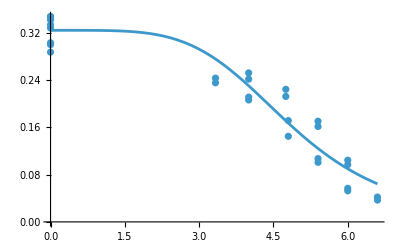

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{0.322385,0.0192771,2.37242,4.86697,4.57919}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

0.0631189

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{0.0583516,{max→0.323026,EC501→0.0194334,β1→2.01055,EC502→4.87048,β2→3.92912}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{175.417,{max→0.323026,EC501→0.0194334,β1→2.01054,EC502→4.87048,β2→3.92912,σ→0.0270073}}

Here the fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.0000390925,0.0000514963,0.000111732,0.0000205991,0.0000352143}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{0.0575375,{max→0.321974,EC501→0.0192035,β1→2.10341,EC502→4.84786,β2→4.06388,a→0.203643}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

FindMaximum::nrnum: The function value -140.963-251.327 ⅈ is not a real number at {max,EC501,β1,EC502,β2,a,σ} = {0.306924,0.0199295,1.56522,4.95062,3.87323,1.17057,-0.0298778}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

{175.979,{max→0.321974,EC501→0.0192035,β1→2.10341,EC502→4.84786,β2→4.06388,a→0.203642,σ→0.0268182}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-0.0000451399,0.0000522038,0.000146818,0.0000199162,0.0000522701,0.000440367}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841. This is NOT SIGNIFICANT:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

0.28906

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.0554006,0.265632,0.498978,0.647885,0.726293,0.769091,0.796698,0.81773,0.83531,0.850545}

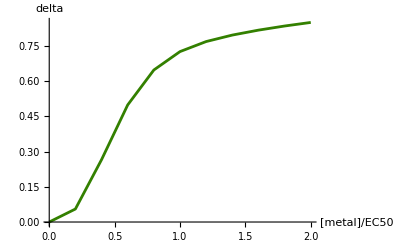

```mathematica
Clear[delta]
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

0.203642

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

0.0192035

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

4.84786

#### CoCu growth data: a = –2.41*** - Delta at EC50 is 0.998 from the model fit

```mathematica
ypad="YPAD";
single1="Co";
single2="Cu";
double="CoCu";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,0.344675},{0,0,0.342987},{0,0,0.346982},{0,0,0.341592},{0,0,0.327645},{0,0,0.299649},{0,0,0.3333},{0,0,0.30274},{0,0,0.286864},{0,0,0.347208}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.7,0,0.280117},{0.7,0,0.28456},{0.86,0,0.241364},{0.86,0,0.255618},{1.,0,0.10552},{1.,0,0.130922},{1.32,0,0.102152},{1.32,0,0.0936645},{2.05,0,0.0312513},{2.05,0,0.0169948},{0.5,0,0.268174},{0.5,0,0.26661},{0.85,0,0.20741},{0.85,0,0.20144},{0.9,0,0.135898},{0.9,0,0.127819},{0.95,0,0.102088},{0.95,0,0.0936526},{1.3,0,0.0237777},{1.3,0,0.0523439}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,8.83,0.259677},{0,8.83,0.238123},{0,10.17,0.217344},{0,10.17,0.180045},{0,10.83,0.160271},{0,10.83,0.171678},{0,12.,0.166475},{0,12.,0.204235},{0,13.5,0.00481236},{0,13.5,0.0423212},{0,4.,0.18923},{0,4.,0.250912},{0,8.83,0.185402},{0,8.83,0.203011},{0,10.17,0.114962},{0,10.17,0.115593},{0,10.85,0.163957},{0,10.85,0.134471},{0,12.9,0.00979951},{0,12.9,0.0099776}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.7,8.83,0.0276007},{0.7,8.83,0.00964607},{0.7,8.83,0.0374432},{0.86,10.17,0.00604919},{0.86,10.17,0.0262002},{0.86,10.17,0.0267061},{1.,10.83,0.00645346},{1.,10.83,0.0156392},{1.,10.83,0.00538175},{1.32,12.,0.0101219},{1.32,12.,0.018061},{1.32,12.,0.0102515},{2.05,13.5,0.0160849},{2.05,13.5,0.00794691},{2.05,13.5,0.0246879},{0.5,4.,0.0142359},{0.5,4.,0.023448},{0.5,4.,0.0163599},{0.85,8.83,0.00815235},{0.85,8.83,0.016854},{0.85,8.83,0.00796167},{0.9,10.17,0.00487953},{0.9,10.17,0.0035555},{0.9,10.17,0.00352831},{0.95,10.85,0.00942361},{0.95,10.85,0.00588449},{0.95,10.85,0.0105333},{1.3,12.9,0.00533197},{1.3,12.9,0.00831473},{1.3,12.9,0.00417861}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.86 | 0.86 | 1. | 1. | 1.32 | 1.32 | 2.05 | 2.05 | 0.5 | 0.5 | 0.85 | 0.85 | 0.9 | 0.9 | 0.95 | 0.95 | 1.3 | 1.3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.7 | 0.86 | 0.86 | 0.86 | 1. | 1. | 1. | 1.32 | 1.32 | 1.32 | 2.05 | 2.05 | 2.05 | 0.5 | 0.5 | 0.5 | 0.85 | 0.85 | 0.85 | 0.9 | 0.9 | 0.9 | 0.95 | 0.95 | 0.95 | 1.3 | 1.3 | 1.3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.83 | 8.83 | 10.17 | 10.17 | 10.83 | 10.83 | 12. | 12. | 13.5 | 13.5 | 4. | 4. | 8.83 | 8.83 | 10.17 | 10.17 | 10.85 | 10.85 | 12.9 | 12.9 | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.83 | 10.83 | 10.83 | 12. | 12. | 12. | 13.5 | 13.5 | 13.5 | 4. | 4. | 4. | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.85 | 10.85 | 10.85 | 12.9 | 12.9 | 12.9
0.344675 | 0.342987 | 0.346982 | 0.341592 | 0.327645 | 0.299649 | 0.3333 | 0.30274 | 0.286864 | 0.347208 | 0.280117 | 0.28456 | 0.241364 | 0.255618 | 0.10552 | 0.130922 | 0.102152 | 0.0936645 | 0.0312513 | 0.0169948 | 0.268174 | 0.26661 | 0.20741 | 0.20144 | 0.135898 | 0.127819 | 0.102088 | 0.0936526 | 0.0237777 | 0.0523439 | 0.259677 | 0.238123 | 0.217344 | 0.180045 | 0.160271 | 0.171678 | 0.166475 | 0.204235 | 0.00481236 | 0.0423212 | 0.18923 | 0.250912 | 0.185402 | 0.203011 | 0.114962 | 0.115593 | 0.163957 | 0.134471 | 0.00979951 | 0.0099776 | 0.0276007 | 0.00964607 | 0.0374432 | 0.00604919 | 0.0262002 | 0.0267061 | 0.00645346 | 0.0156392 | 0.00538175 | 0.0101219 | 0.018061 | 0.0102515 | 0.0160849 | 0.00794691 | 0.0246879 | 0.0142359 | 0.023448 | 0.0163599 | 0.00815235 | 0.016854 | 0.00796167 | 0.00487953 | 0.0035555 | 0.00352831 | 0.00942361 | 0.00588449 | 0.0105333 | 0.00533197 | 0.00831473 | 0.00417861)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{0.7,0.280117},{0.7,0.28456},{0.86,0.241364},{0.86,0.255618},{1.,0.10552},{1.,0.130922},{1.32,0.102152},{1.32,0.0936645},{2.05,0.0312513},{2.05,0.0169948},{0.5,0.268174},{0.5,0.26661},{0.85,0.20741},{0.85,0.20144},{0.9,0.135898},{0.9,0.127819},{0.95,0.102088},{0.95,0.0936526},{1.3,0.0237777},{1.3,0.0523439}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→0.324288,EC501→0.919324,β1→4.68106}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{8.83,0.259677},{8.83,0.238123},{10.17,0.217344},{10.17,0.180045},{10.83,0.160271},{10.83,0.171678},{12.,0.166475},{12.,0.204235},{13.5,0.00481236},{13.5,0.0423212},{4.,0.18923},{4.,0.250912},{8.83,0.185402},{8.83,0.203011},{10.17,0.114962},{10.17,0.115593},{10.85,0.163957},{10.85,0.134471},{12.9,0.00979951},{12.9,0.0099776}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→0.308914,EC502→10.5473,β2→5.84653}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{0.316601,0.919324,4.68106,10.5473,5.84653}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

0.185917

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{0.173754,{max→0.311016,EC501→0.876774,β1→4.06516,EC502→10.1749,β2→4.98414}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{131.771,{max→0.311016,EC501→0.876774,β1→4.06516,EC502→10.1749,β2→4.98414,σ→0.0466039}}

Here the fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.0000156477,0.0000107362,0.0000493171,3.28472×10^-6,-2.70993×10^-6}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{0.0989821,{max→0.308053,EC501→0.940436,β1→5.12161,EC502→10.5578,β2→5.83149,a→-2.40646}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{154.279,{max→0.308053,EC501→0.940436,β1→5.1216,EC502→10.5578,β2→5.83149,a→-2.40646,σ→0.0351749}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-0.0000171344,7.18372×10^-6,0.0000302433,1.58816×10^-6,-0.0000222808,-0.0000637188}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841. This is NOT SIGNIFICANT:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

1.95417×10^-11

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.152374,0.886737,0.985535,0.996308,0.998318,0.998852,0.999033,0.99911,0.999148,0.999172}

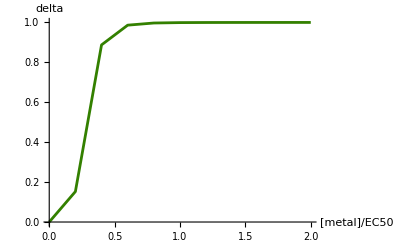

```mathematica
Clear[delta]
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

-2.40646

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

0.940436

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

10.5578

#### CoMn growth data: a = 1.93*** - Delta at EC50 is 0.39 from the model fit

```mathematica
ypad="YPAD";
single1="Co";
single2="Mn";
double="CoMn";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,0.344675},{0,0,0.342987},{0,0,0.346982},{0,0,0.341592},{0,0,0.327645},{0,0,0.299649},{0,0,0.3333},{0,0,0.30274},{0,0,0.286864},{0,0,0.347208}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.7,0,0.280117},{0.7,0,0.28456},{0.86,0,0.241364},{0.86,0,0.255618},{1.,0,0.10552},{1.,0,0.130922},{1.32,0,0.102152},{1.32,0,0.0936645},{2.05,0,0.0312513},{2.05,0,0.0169948},{0.5,0,0.268174},{0.5,0,0.26661},{0.85,0,0.20741},{0.85,0,0.20144},{0.9,0,0.135898},{0.9,0,0.127819},{0.95,0,0.102088},{0.95,0,0.0936526},{1.3,0,0.0237777},{1.3,0,0.0523439}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0.86,0.298582},{0,0.86,0.291635},{0,1.14,0.204455},{0,1.14,0.185045},{0,1.31,0.131089},{0,1.31,0.132071},{0,1.66,0.07621},{0,1.66,0.101139},{0,2.23,0.0603872},{0,2.23,0.0464464},{0,0.85,0.29107},{0,0.85,0.248948},{0,1.,0.193578},{0,1.,0.195635},{0,1.14,0.151442},{0,1.14,0.108769},{0,1.25,0.098664},{0,1.25,0.0744238},{0,1.6,0.045561},{0,1.6,0.057657}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.7,0.86,0.228645},{0.7,0.86,0.21859},{0.86,1.14,0.129718},{0.86,1.14,0.126943},{0.86,1.14,0.145908},{1.,1.31,0.071699},{1.,1.31,0.089585},{1.,1.31,0.0870329},{1.32,1.66,0.0994878},{1.32,1.66,0.0577942},{1.32,1.66,0.0610976},{2.05,2.23,0.0147883},{2.05,2.23,0.0206348},{2.05,2.23,0.0237081},{0.5,0.85,0.199825},{0.5,0.85,0.216688},{0.5,0.85,0.235061},{0.85,1.,0.100977},{0.85,1.,0.118746},{0.85,1.,0.120041},{0.9,1.14,0.0711611},{0.9,1.14,0.0794392},{0.9,1.14,0.0987449},{0.95,1.25,0.035346},{0.95,1.25,0.0392256},{0.95,1.25,0.0366791},{1.3,1.6,0.0263875},{1.3,1.6,0.0204284},{1.3,1.6,0.022205}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.86 | 0.86 | 1. | 1. | 1.32 | 1.32 | 2.05 | 2.05 | 0.5 | 0.5 | 0.85 | 0.85 | 0.9 | 0.9 | 0.95 | 0.95 | 1.3 | 1.3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.86 | 0.86 | 0.86 | 1. | 1. | 1. | 1.32 | 1.32 | 1.32 | 2.05 | 2.05 | 2.05 | 0.5 | 0.5 | 0.5 | 0.85 | 0.85 | 0.85 | 0.9 | 0.9 | 0.9 | 0.95 | 0.95 | 0.95 | 1.3 | 1.3 | 1.3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86 | 0.86 | 1.14 | 1.14 | 1.31 | 1.31 | 1.66 | 1.66 | 2.23 | 2.23 | 0.85 | 0.85 | 1. | 1. | 1.14 | 1.14 | 1.25 | 1.25 | 1.6 | 1.6 | 0.86 | 0.86 | 1.14 | 1.14 | 1.14 | 1.31 | 1.31 | 1.31 | 1.66 | 1.66 | 1.66 | 2.23 | 2.23 | 2.23 | 0.85 | 0.85 | 0.85 | 1. | 1. | 1. | 1.14 | 1.14 | 1.14 | 1.25 | 1.25 | 1.25 | 1.6 | 1.6 | 1.6
0.344675 | 0.342987 | 0.346982 | 0.341592 | 0.327645 | 0.299649 | 0.3333 | 0.30274 | 0.286864 | 0.347208 | 0.280117 | 0.28456 | 0.241364 | 0.255618 | 0.10552 | 0.130922 | 0.102152 | 0.0936645 | 0.0312513 | 0.0169948 | 0.268174 | 0.26661 | 0.20741 | 0.20144 | 0.135898 | 0.127819 | 0.102088 | 0.0936526 | 0.0237777 | 0.0523439 | 0.298582 | 0.291635 | 0.204455 | 0.185045 | 0.131089 | 0.132071 | 0.07621 | 0.101139 | 0.0603872 | 0.0464464 | 0.29107 | 0.248948 | 0.193578 | 0.195635 | 0.151442 | 0.108769 | 0.098664 | 0.0744238 | 0.045561 | 0.057657 | 0.228645 | 0.21859 | 0.129718 | 0.126943 | 0.145908 | 0.071699 | 0.089585 | 0.0870329 | 0.0994878 | 0.0577942 | 0.0610976 | 0.0147883 | 0.0206348 | 0.0237081 | 0.199825 | 0.216688 | 0.235061 | 0.100977 | 0.118746 | 0.120041 | 0.0711611 | 0.0794392 | 0.0987449 | 0.035346 | 0.0392256 | 0.0366791 | 0.0263875 | 0.0204284 | 0.022205)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{0.7,0.280117},{0.7,0.28456},{0.86,0.241364},{0.86,0.255618},{1.,0.10552},{1.,0.130922},{1.32,0.102152},{1.32,0.0936645},{2.05,0.0312513},{2.05,0.0169948},{0.5,0.268174},{0.5,0.26661},{0.85,0.20741},{0.85,0.20144},{0.9,0.135898},{0.9,0.127819},{0.95,0.102088},{0.95,0.0936526},{1.3,0.0237777},{1.3,0.0523439}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→0.324288,EC501→0.919324,β1→4.68106}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{0.86,0.298582},{0.86,0.291635},{1.14,0.204455},{1.14,0.185045},{1.31,0.131089},{1.31,0.132071},{1.66,0.07621},{1.66,0.101139},{2.23,0.0603872},{2.23,0.0464464},{0.85,0.29107},{0.85,0.248948},{1.,0.193578},{1.,0.195635},{1.14,0.151442},{1.14,0.108769},{1.25,0.098664},{1.25,0.0744238},{1.6,0.045561},{1.6,0.057657}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→0.330552,EC502→1.14189,β2→4.37898}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{0.32742,0.919324,4.68106,1.14189,4.37898}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

0.295999

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{0.174271,{max→0.332378,EC501→0.984357,β1→2.10453,EC502→1.24912,β2→2.12612}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{129.509,{max→0.332377,EC501→0.984358,β1→2.10453,EC502→1.24912,β2→2.12612,σ→0.0469677}}

Here the fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{0.0000851978,-0.0000783504,-0.000110234,-0.0000828975,0.0000627505}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{0.0773873,{max→0.32833,EC501→0.914808,β1→4.24463,EC502→1.14512,β2→4.17456,a→1.93224}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{161.575,{max→0.32833,EC501→0.914807,β1→4.24462,EC502→1.14512,β2→4.17456,a→1.93224,σ→0.0312984}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-0.0000549951,0.0000298733,0.000117639,0.0000287466,0.0000548988,9.2229×10^-6}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841, which it is:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

1.11022×10^-15

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.01,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.01,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction, the fit is much better:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.01,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.01,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.00161879,0.0285731,0.129122,0.285449,0.415435,0.492566,0.533543,0.555304,0.567312,0.574259}

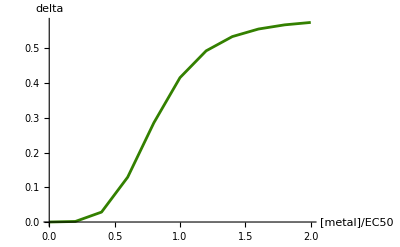

```mathematica
Clear[delta]
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

Except for very low metal concentrations, the deltas are near one (maximum synergistic toxicity)

```mathematica
a[double]=a/.maxlla[[2]]
```

1.93224

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

0.914807

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

1.14512

#### CoNi growth data: a = 0.82*** - Delta at EC50 is 0.81 from the model fit

```mathematica
ypad="YPAD";
single1="Co";
single2="Ni";
double="CoNi";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,0.344675},{0,0,0.342987},{0,0,0.346982},{0,0,0.341592},{0,0,0.327645},{0,0,0.299649},{0,0,0.3333},{0,0,0.30274},{0,0,0.286864},{0,0,0.347208}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.7,0,0.280117},{0.7,0,0.28456},{0.86,0,0.241364},{0.86,0,0.255618},{1.,0,0.10552},{1.,0,0.130922},{1.32,0,0.102152},{1.32,0,0.0936645},{2.05,0,0.0312513},{2.05,0,0.0169948},{0.5,0,0.268174},{0.5,0,0.26661},{0.85,0,0.20741},{0.85,0,0.20144},{0.9,0,0.135898},{0.9,0,0.127819},{0.95,0,0.102088},{0.95,0,0.0936526},{1.3,0,0.0237777},{1.3,0,0.0523439}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,1.88,0.327391},{0,1.88,0.345335},{0,2.4,0.277617},{0,2.4,0.301498},{0,3.,0.161179},{0,3.,0.172964},{0,3.6,0.0728783},{0,3.6,0.0833834},{0,5.1,0.0532982},{0,5.1,0.0435607},{0,2.3,0.325228},{0,2.3,0.331102},{0,2.6,0.291454},{0,2.6,0.301508},{0,2.75,0.137243},{0,2.75,0.0999753},{0,3.,0.100496},{0,3.,0.0797609},{0,3.2,0.036418},{0,3.2,0.0401879}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.7,1.88,0.0999252},{0.7,1.88,0.0995137},{0.7,1.88,0.0874932},{0.86,2.4,0.0657145},{0.86,2.4,0.0559505},{0.86,2.4,0.0573857},{1.,3.,0.0482917},{1.,3.,0.0471212},{1.,3.,0.0549247},{1.32,3.6,0.073827},{1.32,3.6,0.0711625},{1.32,3.6,0.0685457},{2.05,5.1,0.0792517},{2.05,5.1,0.0256799},{2.05,5.1,0.0251502},{0.5,2.3,0.086627},{0.5,2.3,0.0839205},{0.5,2.3,0.0707517},{0.85,2.6,0.0761161},{0.85,2.6,0.0628929},{0.85,2.6,0.0863813},{0.9,2.75,0.0573912},{0.9,2.75,0.0532691},{0.9,2.75,0.054317},{0.95,3.,0.0295707},{0.95,3.,0.0338615},{0.95,3.,0.0353769},{1.3,3.2,0.0300964},{1.3,3.2,0.0191413},{1.3,3.2,0.0191526}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.86 | 0.86 | 1. | 1. | 1.32 | 1.32 | 2.05 | 2.05 | 0.5 | 0.5 | 0.85 | 0.85 | 0.9 | 0.9 | 0.95 | 0.95 | 1.3 | 1.3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.7 | 0.86 | 0.86 | 0.86 | 1. | 1. | 1. | 1.32 | 1.32 | 1.32 | 2.05 | 2.05 | 2.05 | 0.5 | 0.5 | 0.5 | 0.85 | 0.85 | 0.85 | 0.9 | 0.9 | 0.9 | 0.95 | 0.95 | 0.95 | 1.3 | 1.3 | 1.3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.88 | 1.88 | 2.4 | 2.4 | 3. | 3. | 3.6 | 3.6 | 5.1 | 5.1 | 2.3 | 2.3 | 2.6 | 2.6 | 2.75 | 2.75 | 3. | 3. | 3.2 | 3.2 | 1.88 | 1.88 | 1.88 | 2.4 | 2.4 | 2.4 | 3. | 3. | 3. | 3.6 | 3.6 | 3.6 | 5.1 | 5.1 | 5.1 | 2.3 | 2.3 | 2.3 | 2.6 | 2.6 | 2.6 | 2.75 | 2.75 | 2.75 | 3. | 3. | 3. | 3.2 | 3.2 | 3.2
0.344675 | 0.342987 | 0.346982 | 0.341592 | 0.327645 | 0.299649 | 0.3333 | 0.30274 | 0.286864 | 0.347208 | 0.280117 | 0.28456 | 0.241364 | 0.255618 | 0.10552 | 0.130922 | 0.102152 | 0.0936645 | 0.0312513 | 0.0169948 | 0.268174 | 0.26661 | 0.20741 | 0.20144 | 0.135898 | 0.127819 | 0.102088 | 0.0936526 | 0.0237777 | 0.0523439 | 0.327391 | 0.345335 | 0.277617 | 0.301498 | 0.161179 | 0.172964 | 0.0728783 | 0.0833834 | 0.0532982 | 0.0435607 | 0.325228 | 0.331102 | 0.291454 | 0.301508 | 0.137243 | 0.0999753 | 0.100496 | 0.0797609 | 0.036418 | 0.0401879 | 0.0999252 | 0.0995137 | 0.0874932 | 0.0657145 | 0.0559505 | 0.0573857 | 0.0482917 | 0.0471212 | 0.0549247 | 0.073827 | 0.0711625 | 0.0685457 | 0.0792517 | 0.0256799 | 0.0251502 | 0.086627 | 0.0839205 | 0.0707517 | 0.0761161 | 0.0628929 | 0.0863813 | 0.0573912 | 0.0532691 | 0.054317 | 0.0295707 | 0.0338615 | 0.0353769 | 0.0300964 | 0.0191413 | 0.0191526)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{0.7,0.280117},{0.7,0.28456},{0.86,0.241364},{0.86,0.255618},{1.,0.10552},{1.,0.130922},{1.32,0.102152},{1.32,0.0936645},{2.05,0.0312513},{2.05,0.0169948},{0.5,0.268174},{0.5,0.26661},{0.85,0.20741},{0.85,0.20144},{0.9,0.135898},{0.9,0.127819},{0.95,0.102088},{0.95,0.0936526},{1.3,0.0237777},{1.3,0.0523439}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→0.324288,EC501→0.919324,β1→4.68106}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{1.88,0.327391},{1.88,0.345335},{2.4,0.277617},{2.4,0.301498},{3.,0.161179},{3.,0.172964},{3.6,0.0728783},{3.6,0.0833834},{5.1,0.0532982},{5.1,0.0435607},{2.3,0.325228},{2.3,0.331102},{2.6,0.291454},{2.6,0.301508},{2.75,0.137243},{2.75,0.0999753},{3.,0.100496},{3.,0.0797609},{3.2,0.036418},{3.2,0.0401879}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→0.333202,EC502→2.83132,β2→11.6297}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{0.328745,0.919324,4.68106,2.83132,11.6297}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

0.161449

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{0.13301,{max→0.339633,EC501→0.90622,β1→2.10772,EC502→2.85537,β2→8.19545}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{142.459,{max→0.339633,EC501→0.90622,β1→2.10772,EC502→2.85537,β2→8.19546,σ→0.0407753}}

Here the fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.0000139629,0.0000178034,0.000120809,9.2363×10^-6,-0.000176864}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{0.115103,{max→0.336863,EC501→0.892276,β1→2.91213,EC502→2.82877,β2→9.82895,a→0.823525}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{148.243,{max→0.336857,EC501→0.892285,β1→2.91205,EC502→2.82877,β2→9.83337,a→0.82361,σ→0.0379313}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{0.0018427,-0.000952842,0.0025783,0.0000671987,-0.0449806,-0.0103111}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841, which it is:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

0.000671022

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.00726775,0.110523,0.418105,0.710918,0.829251,0.87062,0.911089,0.943444,0.964317,0.977168}

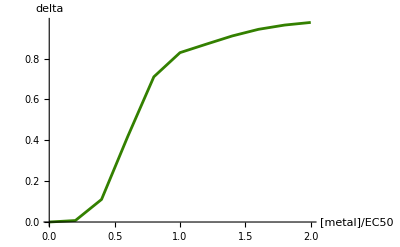

```mathematica
Clear[delta]
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

0.82361

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

0.892285

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

2.82877

#### CoZn growth data: a = –0.02 NS - Delta at EC50 is 0.85 from the model fit

```mathematica
ypad="YPAD";
single1="Co";
single2="Zn";
double="CoZn";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,0.344675},{0,0,0.342987},{0,0,0.346982},{0,0,0.341592},{0,0,0.327645},{0,0,0.299649},{0,0,0.3333},{0,0,0.30274},{0,0,0.286864},{0,0,0.347208}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.7,0,0.280117},{0.7,0,0.28456},{0.86,0,0.241364},{0.86,0,0.255618},{1.,0,0.10552},{1.,0,0.130922},{1.32,0,0.102152},{1.32,0,0.0936645},{2.05,0,0.0312513},{2.05,0,0.0169948},{0.5,0,0.268174},{0.5,0,0.26661},{0.85,0,0.20741},{0.85,0,0.20144},{0.9,0,0.135898},{0.9,0,0.127819},{0.95,0,0.102088},{0.95,0,0.0936526},{1.3,0,0.0237777},{1.3,0,0.0523439}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,4.,0.251828},{0,4.,0.24125},{0,4.75,0.21202},{0,4.75,0.224034},{0,5.4,0.161238},{0,5.4,0.17015},{0,6.,0.0966768},{0,6.,0.104308},{0,6.6,0.0368801},{0,6.6,0.0420288},{0,3.33,0.235142},{0,3.33,0.242968},{0,4.,0.206083},{0,4.,0.210944},{0,4.8,0.144694},{0,4.8,0.171222},{0,5.4,0.106978},{0,5.4,0.100649},{0,6.,0.0567384},{0,6.,0.0524779}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.7,4.,0.0269059},{0.7,4.,0.0791108},{0.7,4.,0.0379193},{0.86,4.75,0.055201},{0.86,4.75,0.0481858},{0.86,4.75,0.0543454},{1.,5.4,0.0432133},{1.,5.4,0.0525031},{1.,5.4,0.0638174},{1.32,6.,0.0159387},{1.32,6.,0.0462395},{1.32,6.,0.0530648},{2.05,6.6,0.042505},{2.05,6.6,0.0147767},{2.05,6.6,0.0123949},{0.5,3.33,0.076839},{0.5,3.33,0.047265},{0.5,3.33,0.0640261},{0.85,4.,0.0454604},{0.85,4.,0.0638613},{0.85,4.,0.0613338},{0.9,4.8,0.0271923},{0.9,4.8,0.0400588},{0.9,4.8,0.0289278},{0.95,5.4,0.0277826},{0.95,5.4,0.0281043},{0.95,5.4,0.0283064},{1.3,6.,0.0199192},{1.3,6.,0.0188146},{1.3,6.,0.0196272}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.86 | 0.86 | 1. | 1. | 1.32 | 1.32 | 2.05 | 2.05 | 0.5 | 0.5 | 0.85 | 0.85 | 0.9 | 0.9 | 0.95 | 0.95 | 1.3 | 1.3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.7 | 0.86 | 0.86 | 0.86 | 1. | 1. | 1. | 1.32 | 1.32 | 1.32 | 2.05 | 2.05 | 2.05 | 0.5 | 0.5 | 0.5 | 0.85 | 0.85 | 0.85 | 0.9 | 0.9 | 0.9 | 0.95 | 0.95 | 0.95 | 1.3 | 1.3 | 1.3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4. | 4. | 4.75 | 4.75 | 5.4 | 5.4 | 6. | 6. | 6.6 | 6.6 | 3.33 | 3.33 | 4. | 4. | 4.8 | 4.8 | 5.4 | 5.4 | 6. | 6. | 4. | 4. | 4. | 4.75 | 4.75 | 4.75 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6. | 6.6 | 6.6 | 6.6 | 3.33 | 3.33 | 3.33 | 4. | 4. | 4. | 4.8 | 4.8 | 4.8 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6.
0.344675 | 0.342987 | 0.346982 | 0.341592 | 0.327645 | 0.299649 | 0.3333 | 0.30274 | 0.286864 | 0.347208 | 0.280117 | 0.28456 | 0.241364 | 0.255618 | 0.10552 | 0.130922 | 0.102152 | 0.0936645 | 0.0312513 | 0.0169948 | 0.268174 | 0.26661 | 0.20741 | 0.20144 | 0.135898 | 0.127819 | 0.102088 | 0.0936526 | 0.0237777 | 0.0523439 | 0.251828 | 0.24125 | 0.21202 | 0.224034 | 0.161238 | 0.17015 | 0.0966768 | 0.104308 | 0.0368801 | 0.0420288 | 0.235142 | 0.242968 | 0.206083 | 0.210944 | 0.144694 | 0.171222 | 0.106978 | 0.100649 | 0.0567384 | 0.0524779 | 0.0269059 | 0.0791108 | 0.0379193 | 0.055201 | 0.0481858 | 0.0543454 | 0.0432133 | 0.0525031 | 0.0638174 | 0.0159387 | 0.0462395 | 0.0530648 | 0.042505 | 0.0147767 | 0.0123949 | 0.076839 | 0.047265 | 0.0640261 | 0.0454604 | 0.0638613 | 0.0613338 | 0.0271923 | 0.0400588 | 0.0289278 | 0.0277826 | 0.0281043 | 0.0283064 | 0.0199192 | 0.0188146 | 0.0196272)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{0.7,0.280117},{0.7,0.28456},{0.86,0.241364},{0.86,0.255618},{1.,0.10552},{1.,0.130922},{1.32,0.102152},{1.32,0.0936645},{2.05,0.0312513},{2.05,0.0169948},{0.5,0.268174},{0.5,0.26661},{0.85,0.20741},{0.85,0.20144},{0.9,0.135898},{0.9,0.127819},{0.95,0.102088},{0.95,0.0936526},{1.3,0.0237777},{1.3,0.0523439}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→0.324288,EC501→0.919324,β1→4.68106}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{4.,0.251828},{4.,0.24125},{4.75,0.21202},{4.75,0.224034},{5.4,0.161238},{5.4,0.17015},{6.,0.0966768},{6.,0.104308},{6.6,0.0368801},{6.6,0.0420288},{3.33,0.235142},{3.33,0.242968},{4.,0.206083},{4.,0.210944},{4.8,0.144694},{4.8,0.171222},{5.4,0.106978},{5.4,0.100649},{6.,0.0567384},{6.,0.0524779}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→0.323794,EC502→4.86697,β2→4.57919}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{0.324041,0.919324,4.68106,4.86697,4.57919}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

0.0784596

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{0.074096,{max→0.327543,EC501→0.914441,β1→3.53674,EC502→4.79745,β2→3.88177}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{165.862,{max→0.327543,EC501→0.91444,β1→3.53674,EC502→4.79745,β2→3.88177,σ→0.0304335}}

Here the fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.0000498022,0.0000337103,0.0000968264,0.0000274219,0.000073258}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{0.0740912,{max→0.327593,EC501→0.914673,β1→3.52301,EC502→4.79837,β2→3.87143,a→-0.0179014}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{165.864,{max→0.327594,EC501→0.914673,β1→3.523,EC502→4.79837,β2→3.87143,a→-0.0179023,σ→0.0304326}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-0.0000608577,0.0000395515,0.000137438,0.0000321883,0.000102788,-0.00522835}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841. This is not significant:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

0.942656

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.0309433,0.285006,0.615092,0.787287,0.85854,0.889366,0.90409,0.911833,0.916262,0.918987}

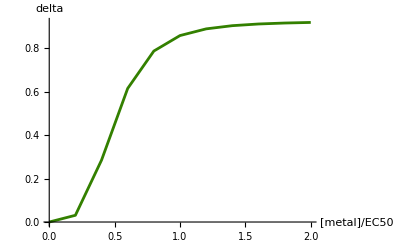

```mathematica
Clear[delta]
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

-0.0179023

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

0.914673

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

4.79837

#### CuMn growth data: a = 3.25*** [SLOW FOR a=0] - Delta at EC50 is –0.27 from the model fit

```mathematica
ypad="YPAD";
single1="Cu";
single2="Mn";
double="CuMn";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,0.344675},{0,0,0.342987},{0,0,0.346982},{0,0,0.341592},{0,0,0.327645},{0,0,0.299649},{0,0,0.3333},{0,0,0.30274},{0,0,0.286864},{0,0,0.347208}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{8.83,0,0.259677},{8.83,0,0.238123},{10.17,0,0.217344},{10.17,0,0.180045},{10.83,0,0.160271},{10.83,0,0.171678},{12.,0,0.166475},{12.,0,0.204235},{13.5,0,0.00481236},{13.5,0,0.0423212},{4.,0,0.18923},{4.,0,0.250912},{8.83,0,0.185402},{8.83,0,0.203011},{10.17,0,0.114962},{10.17,0,0.115593},{10.85,0,0.163957},{10.85,0,0.134471},{12.9,0,0.00979951},{12.9,0,0.0099776}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0.86,0.298582},{0,0.86,0.291635},{0,1.14,0.204455},{0,1.14,0.185045},{0,1.31,0.131089},{0,1.31,0.132071},{0,1.66,0.07621},{0,1.66,0.101139},{0,2.23,0.0603872},{0,2.23,0.0464464},{0,0.85,0.29107},{0,0.85,0.248948},{0,1.,0.193578},{0,1.,0.195635},{0,1.14,0.151442},{0,1.14,0.108769},{0,1.25,0.098664},{0,1.25,0.0744238},{0,1.6,0.045561},{0,1.6,0.057657}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{8.83,0.86,0.251349},{8.83,0.86,0.250411},{8.83,0.86,0.257015},{10.17,1.14,0.221852},{10.17,1.14,0.243214},{10.17,1.14,0.227455},{10.83,1.31,0.210464},{10.83,1.31,0.206818},{10.83,1.31,0.211348},{12.,1.66,0.1412},{12.,1.66,0.154971},{12.,1.66,0.159278},{13.5,2.23,0.0831317},{13.5,2.23,0.0742732},{13.5,2.23,0.0921542},{4.,0.85,0.213485},{4.,0.85,0.241575},{4.,0.85,0.26004},{8.83,1.,0.231269},{8.83,1.,0.214226},{8.83,1.,0.218247},{10.17,1.14,0.202979},{10.17,1.14,0.192541},{10.17,1.14,0.204047},{10.85,1.25,0.157589},{10.85,1.25,0.1368},{10.85,1.25,0.15326},{12.9,1.6,0.0570409},{12.9,1.6,0.0419474},{12.9,1.6,0.0774471}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.83 | 8.83 | 10.17 | 10.17 | 10.83 | 10.83 | 12. | 12. | 13.5 | 13.5 | 4. | 4. | 8.83 | 8.83 | 10.17 | 10.17 | 10.85 | 10.85 | 12.9 | 12.9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.83 | 10.83 | 10.83 | 12. | 12. | 12. | 13.5 | 13.5 | 13.5 | 4. | 4. | 4. | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.85 | 10.85 | 10.85 | 12.9 | 12.9 | 12.9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86 | 0.86 | 1.14 | 1.14 | 1.31 | 1.31 | 1.66 | 1.66 | 2.23 | 2.23 | 0.85 | 0.85 | 1. | 1. | 1.14 | 1.14 | 1.25 | 1.25 | 1.6 | 1.6 | 0.86 | 0.86 | 0.86 | 1.14 | 1.14 | 1.14 | 1.31 | 1.31 | 1.31 | 1.66 | 1.66 | 1.66 | 2.23 | 2.23 | 2.23 | 0.85 | 0.85 | 0.85 | 1. | 1. | 1. | 1.14 | 1.14 | 1.14 | 1.25 | 1.25 | 1.25 | 1.6 | 1.6 | 1.6
0.344675 | 0.342987 | 0.346982 | 0.341592 | 0.327645 | 0.299649 | 0.3333 | 0.30274 | 0.286864 | 0.347208 | 0.259677 | 0.238123 | 0.217344 | 0.180045 | 0.160271 | 0.171678 | 0.166475 | 0.204235 | 0.00481236 | 0.0423212 | 0.18923 | 0.250912 | 0.185402 | 0.203011 | 0.114962 | 0.115593 | 0.163957 | 0.134471 | 0.00979951 | 0.0099776 | 0.298582 | 0.291635 | 0.204455 | 0.185045 | 0.131089 | 0.132071 | 0.07621 | 0.101139 | 0.0603872 | 0.0464464 | 0.29107 | 0.248948 | 0.193578 | 0.195635 | 0.151442 | 0.108769 | 0.098664 | 0.0744238 | 0.045561 | 0.057657 | 0.251349 | 0.250411 | 0.257015 | 0.221852 | 0.243214 | 0.227455 | 0.210464 | 0.206818 | 0.211348 | 0.1412 | 0.154971 | 0.159278 | 0.0831317 | 0.0742732 | 0.0921542 | 0.213485 | 0.241575 | 0.26004 | 0.231269 | 0.214226 | 0.218247 | 0.202979 | 0.192541 | 0.204047 | 0.157589 | 0.1368 | 0.15326 | 0.0570409 | 0.0419474 | 0.0774471)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{8.83,0.259677},{8.83,0.238123},{10.17,0.217344},{10.17,0.180045},{10.83,0.160271},{10.83,0.171678},{12.,0.166475},{12.,0.204235},{13.5,0.00481236},{13.5,0.0423212},{4.,0.18923},{4.,0.250912},{8.83,0.185402},{8.83,0.203011},{10.17,0.114962},{10.17,0.115593},{10.85,0.163957},{10.85,0.134471},{12.9,0.00979951},{12.9,0.0099776}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→0.308914,EC501→10.5473,β1→5.84653}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{0.86,0.298582},{0.86,0.291635},{1.14,0.204455},{1.14,0.185045},{1.31,0.131089},{1.31,0.132071},{1.66,0.07621},{1.66,0.101139},{2.23,0.0603872},{2.23,0.0464464},{0.85,0.29107},{0.85,0.248948},{1.,0.193578},{1.,0.195635},{1.14,0.151442},{1.14,0.108769},{1.25,0.098664},{1.25,0.0744238},{1.6,0.045561},{1.6,0.057657}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→0.330552,EC502→1.14189,β2→4.37898}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{0.319733,10.5473,5.84653,1.14189,4.37898}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

0.945015

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

FindMinimum::nrnum: The function value 3373.1-207.676 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {0.309678,11.1179,2.93461,1.43024,0.0294082}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::sdir: Search direction has become too small.

{0.272986,{max→0.331708,EC501→11.0035,β1→9.59432,EC502→2.22999,β2→0.0366814}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

FindMaximum::nrnum: The function value 7849.39-17475.9 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {0.326351,12.8008,0.026153,1.13732,2.51359,0.0648985}.

FindMaximum::nrnum: The function value 6.42337-181.681 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {0.326939,12.7976,0.238408,1.34887,2.50734,0.0681078}.

FindMaximum::nrnum: The function value 6.41782-181.673 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {0.326933,12.7976,0.238408,1.34887,2.50734,0.0681078}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{104.826,{max→0.344447,EC501→10.3408,β1→4.68392,EC502→1.17681,β2→0.000118637,σ→0.065274}}

Here the fits aren’t compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-3.69825,6.40879,104.835,89.4941,30819.1}

The sum of squares fit is the one that is better:

```mathematica
sumofsquares[max/.maxll[[2]],EC501/.maxll[[2]],β1/.maxll[[2]],EC502/.maxll[[2]],β2/.maxll[[2]],dataset]
```

0.34079

```mathematica
lnlikelihood[max/.ssq[[2]],EC501/.ssq[[2]],β1/.ssq[[2]],EC502/.ssq[[2]],β2/.ssq[[2]],0.08,dataset]
```

107.216

Restarting the ML fit from the sum of squares fit leads to a better fit:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,max/.ssq[[2]]},{EC501,EC501/.ssq[[2]]},{β1,β1/.ssq[[2]]},{EC502,EC502/.ssq[[2]]},{β2,β2/.ssq[[2]]},{σ,0.04,0,1}}]
```

FindMaximum::nrnum: The function value -115155.+302408. ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {0.33453,11.0035,9.59432,2.20771,0.0612795,0.0203466}.

FindMaximum::nrnum: The function value -6581.79-48084.9 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {0.331797,11.0035,9.59432,2.20769,0.0379711,0.0390438}.

FindMaximum::nrnum: The function value -6189.86-119.518 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {0.332562,11.0035,9.59432,2.20767,0.0352987,0.040371}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{111.821,{max→0.330423,EC501→11.0031,β1→9.59359,EC502→2.20166,β2→0.0338372,σ→0.05994}}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{0.126539,{max→0.304501,EC501→10.5774,β1→5.3915,EC502→1.20109,β2→3.76779,a→3.25269}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

FindMaximum::nrnum: The function value 12410.7-251.327 ⅈ is not a real number at {max,EC501,β1,EC502,β2,a,σ} = {0.331132,10.5949,5.47755,0.0153112,4.63671,3.87594,-0.00829315}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

{144.454,{max→0.304501,EC501→10.5774,β1→5.3915,EC502→1.20109,β2→3.76779,a→3.25269,σ→0.039771}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-0.0000126385,1.2699×10^-6,-8.08393×10^-6,6.40718×10^-6,0.0000520116,2.94126×10^-6}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841. This is significant:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

6.66134×10^-16

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/200}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,-0.000679819,-0.00833557,-0.0382754,-0.116941,-0.259616,-0.421015,-0.535356,-0.584882,-0.585725,-0.557736}

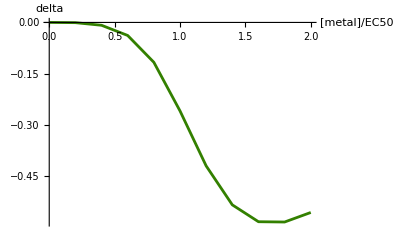

```mathematica
Clear[delta]
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

3.25269

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

10.5774

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

1.20109

#### CuNi growth data: a = –0.98* - Delta at EC50 is 0.998 from the model fit

```mathematica
ypad="YPAD";
single1="Cu";
single2="Ni";
double="CuNi";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,0.344675},{0,0,0.342987},{0,0,0.346982},{0,0,0.341592},{0,0,0.327645},{0,0,0.299649},{0,0,0.3333},{0,0,0.30274},{0,0,0.286864},{0,0,0.347208}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{8.83,0,0.259677},{8.83,0,0.238123},{10.17,0,0.217344},{10.17,0,0.180045},{10.83,0,0.160271},{10.83,0,0.171678},{12.,0,0.166475},{12.,0,0.204235},{13.5,0,0.00481236},{13.5,0,0.0423212},{4.,0,0.18923},{4.,0,0.250912},{8.83,0,0.185402},{8.83,0,0.203011},{10.17,0,0.114962},{10.17,0,0.115593},{10.85,0,0.163957},{10.85,0,0.134471},{12.9,0,0.00979951},{12.9,0,0.0099776}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,1.88,0.327391},{0,1.88,0.345335},{0,2.4,0.277617},{0,2.4,0.301498},{0,3.,0.161179},{0,3.,0.172964},{0,3.6,0.0728783},{0,3.6,0.0833834},{0,5.1,0.0532982},{0,5.1,0.0435607},{0,2.3,0.325228},{0,2.3,0.331102},{0,2.6,0.291454},{0,2.6,0.301508},{0,2.75,0.137243},{0,2.75,0.0999753},{0,3.,0.100496},{0,3.,0.0797609},{0,3.2,0.036418},{0,3.2,0.0401879}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{8.83,1.88,0.00634008},{8.83,1.88,0.00686024},{8.83,1.88,0.022887},{10.17,2.4,0.00717996},{10.17,2.4,0.0310211},{10.17,2.4,0.0450001},{10.83,3.,0.0402603},{10.83,3.,0.0279148},{10.83,3.,0.00474032},{12.,3.6,0.00953732},{12.,3.6,0.00535853},{12.,3.6,0.0240011},{13.5,5.1,0.0224755},{13.5,5.1,0.0192538},{13.5,5.1,0.0263258},{4.,2.3,0.00712952},{4.,2.3,0.0108796},{4.,2.3,0.00727112},{8.83,2.6,0.00864003},{8.83,2.6,0.00774587},{8.83,2.6,0.0060278},{10.17,2.75,0.0096729},{10.17,2.75,0.00461976},{10.17,2.75,0.0123008},{10.85,3.,0.00755111},{10.85,3.,0.00649955},{10.85,3.,0.01469},{12.9,3.2,0.0109546},{12.9,3.2,0.00892617},{12.9,3.2,0.0128823}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.83 | 8.83 | 10.17 | 10.17 | 10.83 | 10.83 | 12. | 12. | 13.5 | 13.5 | 4. | 4. | 8.83 | 8.83 | 10.17 | 10.17 | 10.85 | 10.85 | 12.9 | 12.9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.83 | 10.83 | 10.83 | 12. | 12. | 12. | 13.5 | 13.5 | 13.5 | 4. | 4. | 4. | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.85 | 10.85 | 10.85 | 12.9 | 12.9 | 12.9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.88 | 1.88 | 2.4 | 2.4 | 3. | 3. | 3.6 | 3.6 | 5.1 | 5.1 | 2.3 | 2.3 | 2.6 | 2.6 | 2.75 | 2.75 | 3. | 3. | 3.2 | 3.2 | 1.88 | 1.88 | 1.88 | 2.4 | 2.4 | 2.4 | 3. | 3. | 3. | 3.6 | 3.6 | 3.6 | 5.1 | 5.1 | 5.1 | 2.3 | 2.3 | 2.3 | 2.6 | 2.6 | 2.6 | 2.75 | 2.75 | 2.75 | 3. | 3. | 3. | 3.2 | 3.2 | 3.2
0.344675 | 0.342987 | 0.346982 | 0.341592 | 0.327645 | 0.299649 | 0.3333 | 0.30274 | 0.286864 | 0.347208 | 0.259677 | 0.238123 | 0.217344 | 0.180045 | 0.160271 | 0.171678 | 0.166475 | 0.204235 | 0.00481236 | 0.0423212 | 0.18923 | 0.250912 | 0.185402 | 0.203011 | 0.114962 | 0.115593 | 0.163957 | 0.134471 | 0.00979951 | 0.0099776 | 0.327391 | 0.345335 | 0.277617 | 0.301498 | 0.161179 | 0.172964 | 0.0728783 | 0.0833834 | 0.0532982 | 0.0435607 | 0.325228 | 0.331102 | 0.291454 | 0.301508 | 0.137243 | 0.0999753 | 0.100496 | 0.0797609 | 0.036418 | 0.0401879 | 0.00634008 | 0.00686024 | 0.022887 | 0.00717996 | 0.0310211 | 0.0450001 | 0.0402603 | 0.0279148 | 0.00474032 | 0.00953732 | 0.00535853 | 0.0240011 | 0.0224755 | 0.0192538 | 0.0263258 | 0.00712952 | 0.0108796 | 0.00727112 | 0.00864003 | 0.00774587 | 0.0060278 | 0.0096729 | 0.00461976 | 0.0123008 | 0.00755111 | 0.00649955 | 0.01469 | 0.0109546 | 0.00892617 | 0.0128823)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{8.83,0.259677},{8.83,0.238123},{10.17,0.217344},{10.17,0.180045},{10.83,0.160271},{10.83,0.171678},{12.,0.166475},{12.,0.204235},{13.5,0.00481236},{13.5,0.0423212},{4.,0.18923},{4.,0.250912},{8.83,0.185402},{8.83,0.203011},{10.17,0.114962},{10.17,0.115593},{10.85,0.163957},{10.85,0.134471},{12.9,0.00979951},{12.9,0.0099776}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→0.308914,EC501→10.5473,β1→5.84653}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{1.88,0.327391},{1.88,0.345335},{2.4,0.277617},{2.4,0.301498},{3.,0.161179},{3.,0.172964},{3.6,0.0728783},{3.6,0.0833834},{5.1,0.0532982},{5.1,0.0435607},{2.3,0.325228},{2.3,0.331102},{2.6,0.291454},{2.6,0.301508},{2.75,0.137243},{2.75,0.0999753},{3.,0.100496},{3.,0.0797609},{3.2,0.036418},{3.2,0.0401879}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→0.333202,EC502→2.83132,β2→11.6297}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{0.321058,10.5473,5.84653,2.83132,11.6297}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

0.125409

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{0.127761,{max→0.3216,EC501→10.3317,β1→5.91344,EC502→2.84166,β2→9.99997}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{144.07,{max→0.3216,EC501→10.3317,β1→5.91345,EC502→2.84166,β2→9.99999,σ→0.0399627}}

Here the fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-9.33298×10^-6,-9.56854×10^-7,-0.0000193871,3.47806×10^-6,-0.000186268}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{0.120325,{max→0.321147,EC501→10.3706,β1→5.43853,EC502→2.86198,β2→9.99993,a→-0.978808}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{146.468,{max→0.321147,EC501→10.3706,β1→5.43853,EC502→2.86198,β2→10.,a→-0.978808,σ→0.0387823}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{8.74542×10^-7,-5.85537×10^-6,-0.0000445273,0.0000119622,-0.000694233,-0.0000170595}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841. This is marginally SIGNIFICANT:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

0.0285036

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.00986121,0.536333,0.954012,0.993456,0.997983,0.998801,0.99915,0.99938,0.999539,0.999651}

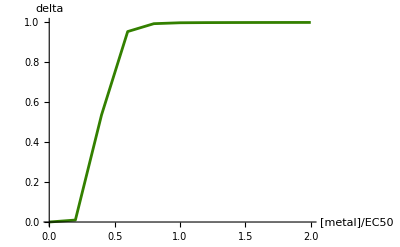

```mathematica
Clear[delta]
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

-0.978808

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

10.3706

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

2.86198

#### CuZn growth data: a = –1.76*** - Delta at EC50 is 0.996 from the model fit

```mathematica
ypad="YPAD";
single1="Cu";
single2="Zn";
double="CuZn";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,0.344675},{0,0,0.342987},{0,0,0.346982},{0,0,0.341592},{0,0,0.327645},{0,0,0.299649},{0,0,0.3333},{0,0,0.30274},{0,0,0.286864},{0,0,0.347208}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{8.83,0,0.259677},{8.83,0,0.238123},{10.17,0,0.217344},{10.17,0,0.180045},{10.83,0,0.160271},{10.83,0,0.171678},{12.,0,0.166475},{12.,0,0.204235},{13.5,0,0.00481236},{13.5,0,0.0423212},{4.,0,0.18923},{4.,0,0.250912},{8.83,0,0.185402},{8.83,0,0.203011},{10.17,0,0.114962},{10.17,0,0.115593},{10.85,0,0.163957},{10.85,0,0.134471},{12.9,0,0.00979951},{12.9,0,0.0099776}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,4.,0.251828},{0,4.,0.24125},{0,4.75,0.21202},{0,4.75,0.224034},{0,5.4,0.161238},{0,5.4,0.17015},{0,6.,0.0966768},{0,6.,0.104308},{0,6.6,0.0368801},{0,6.6,0.0420288},{0,3.33,0.235142},{0,3.33,0.242968},{0,4.,0.206083},{0,4.,0.210944},{0,4.8,0.144694},{0,4.8,0.171222},{0,5.4,0.106978},{0,5.4,0.100649},{0,6.,0.0567384},{0,6.,0.0524779}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{8.83,4.,0.0170233},{8.83,4.,0.0120931},{8.83,4.,0.0252378},{10.17,4.75,0.0260138},{10.17,4.75,0.0367819},{10.17,4.75,0.0276578},{10.83,5.4,0.0243504},{10.83,5.4,0.0106856},{10.83,5.4,0.0253572},{12.,6.,0.0287813},{12.,6.,0.030129},{12.,6.,0.0107954},{13.5,6.6,0.0217127},{13.5,6.6,0.031668},{13.5,6.6,0.0192816},{4.,3.33,0.0210641},{4.,3.33,0.0200784},{4.,3.33,0.0184946},{8.83,4.,0.0245018},{8.83,4.,0.0156439},{8.83,4.,0.0177379},{10.17,4.8,0.0154039},{10.17,4.8,0.013761},{10.17,4.8,0.00868284},{10.85,5.4,0.0164645},{10.85,5.4,0.0181277},{10.85,5.4,0.0151992},{12.9,6.,0.0166835},{12.9,6.,0.015556},{12.9,6.,0.0241739}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.83 | 8.83 | 10.17 | 10.17 | 10.83 | 10.83 | 12. | 12. | 13.5 | 13.5 | 4. | 4. | 8.83 | 8.83 | 10.17 | 10.17 | 10.85 | 10.85 | 12.9 | 12.9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.83 | 10.83 | 10.83 | 12. | 12. | 12. | 13.5 | 13.5 | 13.5 | 4. | 4. | 4. | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.85 | 10.85 | 10.85 | 12.9 | 12.9 | 12.9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4. | 4. | 4.75 | 4.75 | 5.4 | 5.4 | 6. | 6. | 6.6 | 6.6 | 3.33 | 3.33 | 4. | 4. | 4.8 | 4.8 | 5.4 | 5.4 | 6. | 6. | 4. | 4. | 4. | 4.75 | 4.75 | 4.75 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6. | 6.6 | 6.6 | 6.6 | 3.33 | 3.33 | 3.33 | 4. | 4. | 4. | 4.8 | 4.8 | 4.8 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6.
0.344675 | 0.342987 | 0.346982 | 0.341592 | 0.327645 | 0.299649 | 0.3333 | 0.30274 | 0.286864 | 0.347208 | 0.259677 | 0.238123 | 0.217344 | 0.180045 | 0.160271 | 0.171678 | 0.166475 | 0.204235 | 0.00481236 | 0.0423212 | 0.18923 | 0.250912 | 0.185402 | 0.203011 | 0.114962 | 0.115593 | 0.163957 | 0.134471 | 0.00979951 | 0.0099776 | 0.251828 | 0.24125 | 0.21202 | 0.224034 | 0.161238 | 0.17015 | 0.0966768 | 0.104308 | 0.0368801 | 0.0420288 | 0.235142 | 0.242968 | 0.206083 | 0.210944 | 0.144694 | 0.171222 | 0.106978 | 0.100649 | 0.0567384 | 0.0524779 | 0.0170233 | 0.0120931 | 0.0252378 | 0.0260138 | 0.0367819 | 0.0276578 | 0.0243504 | 0.0106856 | 0.0253572 | 0.0287813 | 0.030129 | 0.0107954 | 0.0217127 | 0.031668 | 0.0192816 | 0.0210641 | 0.0200784 | 0.0184946 | 0.0245018 | 0.0156439 | 0.0177379 | 0.0154039 | 0.013761 | 0.00868284 | 0.0164645 | 0.0181277 | 0.0151992 | 0.0166835 | 0.015556 | 0.0241739)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{8.83,0.259677},{8.83,0.238123},{10.17,0.217344},{10.17,0.180045},{10.83,0.160271},{10.83,0.171678},{12.,0.166475},{12.,0.204235},{13.5,0.00481236},{13.5,0.0423212},{4.,0.18923},{4.,0.250912},{8.83,0.185402},{8.83,0.203011},{10.17,0.114962},{10.17,0.115593},{10.85,0.163957},{10.85,0.134471},{12.9,0.00979951},{12.9,0.0099776}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→0.308914,EC501→10.5473,β1→5.84653}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{4.,0.251828},{4.,0.24125},{4.75,0.21202},{4.75,0.224034},{5.4,0.161238},{5.4,0.17015},{6.,0.0966768},{6.,0.104308},{6.6,0.0368801},{6.6,0.0420288},{3.33,0.235142},{3.33,0.242968},{4.,0.206083},{4.,0.210944},{4.8,0.144694},{4.8,0.171222},{5.4,0.106978},{5.4,0.100649},{6.,0.0567384},{6.,0.0524779}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→0.323794,EC502→4.86697,β2→4.57919}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{0.316354,10.5473,5.84653,4.86697,4.57919}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

0.129552

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{0.125501,{max→0.309034,EC501→10.3803,β1→5.65405,EC502→4.80464,β2→4.90926}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{144.784,{max→0.309034,EC501→10.3803,β1→5.65405,EC502→4.80464,β2→4.90926,σ→0.0396076}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.0000134783,1.62564×10^-6,-0.0000130345,4.61762×10^-6,0.0000179202}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{0.0939046,{max→0.305881,EC501→10.5857,β1→5.8171,EC502→5.0159,β2→5.05145,a→-1.7573}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{156.385,{max→0.305881,EC501→10.5857,β1→5.8171,EC502→5.0159,β2→5.05145,a→-1.75731,σ→0.0342609}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-0.0000134015,-1.33241×10^-7,-0.0000318273,1.76095×10^-6,0.0000217106,-0.0000569757}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841, which it is:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

1.45805×10^-6

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.01,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.01,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction, the fit is much better:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.01,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.01,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.0705192,0.761342,0.964533,0.99067,0.995703,0.997056,0.997522,0.99772,0.997823,0.997887}

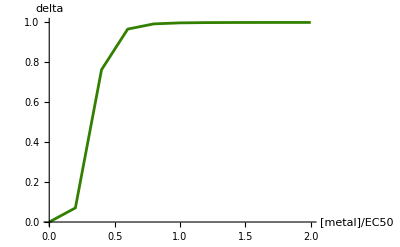

```mathematica
Clear[delta]
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

Except for very low metal concentrations, the deltas are near one (maximum synergistic toxicity)

```mathematica
a[double]=a/.maxlla[[2]]
```

-1.75731

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

10.5857

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

5.0159

#### MnNi growth data: a = 2.24*** - Delta at EC50 is 0.38 from the model fit

```mathematica
ypad="YPAD";
single1="Mn";
single2="Ni";
double="MnNi";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,0.344675},{0,0,0.342987},{0,0,0.346982},{0,0,0.341592},{0,0,0.327645},{0,0,0.299649},{0,0,0.3333},{0,0,0.30274},{0,0,0.286864},{0,0,0.347208}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.86,0,0.298582},{0.86,0,0.291635},{1.14,0,0.204455},{1.14,0,0.185045},{1.31,0,0.131089},{1.31,0,0.132071},{1.66,0,0.07621},{1.66,0,0.101139},{2.23,0,0.0603872},{2.23,0,0.0464464},{0.85,0,0.29107},{0.85,0,0.248948},{1.,0,0.193578},{1.,0,0.195635},{1.14,0,0.151442},{1.14,0,0.108769},{1.25,0,0.098664},{1.25,0,0.0744238},{1.6,0,0.045561},{1.6,0,0.057657}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,1.88,0.327391},{0,1.88,0.345335},{0,2.4,0.277617},{0,2.4,0.301498},{0,3.,0.161179},{0,3.,0.172964},{0,3.6,0.0728783},{0,3.6,0.0833834},{0,5.1,0.0532982},{0,5.1,0.0435607},{0,2.3,0.325228},{0,2.3,0.331102},{0,2.6,0.291454},{0,2.6,0.301508},{0,2.75,0.137243},{0,2.75,0.0999753},{0,3.,0.100496},{0,3.,0.0797609},{0,3.2,0.036418},{0,3.2,0.0401879}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.86,1.88,0.249273},{0.86,1.88,0.267128},{0.86,1.88,0.284672},{1.14,2.4,0.153141},{1.14,2.4,0.16521},{1.14,2.4,0.180357},{1.31,3.,0.0881524},{1.31,3.,0.067525},{1.31,3.,0.0697505},{1.66,3.6,0.075097},{1.66,3.6,0.0285306},{1.66,3.6,0.0679557},{2.23,5.1,0.017496},{2.23,5.1,0.0356386},{2.23,5.1,0.0158965},{0.85,2.3,0.237758},{0.85,2.3,0.237225},{0.85,2.3,0.253505},{1.,2.6,0.141991},{1.,2.6,0.147557},{1.,2.6,0.145619},{1.14,2.75,0.0993275},{1.14,2.75,0.038066},{1.14,2.75,0.0620686},{1.25,3.,0.0269146},{1.25,3.,0.0431669},{1.25,3.,0.0613796},{1.6,3.2,0.0123823},{1.6,3.2,0.0207262},{1.6,3.2,0.0350612}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86 | 0.86 | 1.14 | 1.14 | 1.31 | 1.31 | 1.66 | 1.66 | 2.23 | 2.23 | 0.85 | 0.85 | 1. | 1. | 1.14 | 1.14 | 1.25 | 1.25 | 1.6 | 1.6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86 | 0.86 | 0.86 | 1.14 | 1.14 | 1.14 | 1.31 | 1.31 | 1.31 | 1.66 | 1.66 | 1.66 | 2.23 | 2.23 | 2.23 | 0.85 | 0.85 | 0.85 | 1. | 1. | 1. | 1.14 | 1.14 | 1.14 | 1.25 | 1.25 | 1.25 | 1.6 | 1.6 | 1.6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.88 | 1.88 | 2.4 | 2.4 | 3. | 3. | 3.6 | 3.6 | 5.1 | 5.1 | 2.3 | 2.3 | 2.6 | 2.6 | 2.75 | 2.75 | 3. | 3. | 3.2 | 3.2 | 1.88 | 1.88 | 1.88 | 2.4 | 2.4 | 2.4 | 3. | 3. | 3. | 3.6 | 3.6 | 3.6 | 5.1 | 5.1 | 5.1 | 2.3 | 2.3 | 2.3 | 2.6 | 2.6 | 2.6 | 2.75 | 2.75 | 2.75 | 3. | 3. | 3. | 3.2 | 3.2 | 3.2
0.344675 | 0.342987 | 0.346982 | 0.341592 | 0.327645 | 0.299649 | 0.3333 | 0.30274 | 0.286864 | 0.347208 | 0.298582 | 0.291635 | 0.204455 | 0.185045 | 0.131089 | 0.132071 | 0.07621 | 0.101139 | 0.0603872 | 0.0464464 | 0.29107 | 0.248948 | 0.193578 | 0.195635 | 0.151442 | 0.108769 | 0.098664 | 0.0744238 | 0.045561 | 0.057657 | 0.327391 | 0.345335 | 0.277617 | 0.301498 | 0.161179 | 0.172964 | 0.0728783 | 0.0833834 | 0.0532982 | 0.0435607 | 0.325228 | 0.331102 | 0.291454 | 0.301508 | 0.137243 | 0.0999753 | 0.100496 | 0.0797609 | 0.036418 | 0.0401879 | 0.249273 | 0.267128 | 0.284672 | 0.153141 | 0.16521 | 0.180357 | 0.0881524 | 0.067525 | 0.0697505 | 0.075097 | 0.0285306 | 0.0679557 | 0.017496 | 0.0356386 | 0.0158965 | 0.237758 | 0.237225 | 0.253505 | 0.141991 | 0.147557 | 0.145619 | 0.0993275 | 0.038066 | 0.0620686 | 0.0269146 | 0.0431669 | 0.0613796 | 0.0123823 | 0.0207262 | 0.0350612)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{0.86,0.298582},{0.86,0.291635},{1.14,0.204455},{1.14,0.185045},{1.31,0.131089},{1.31,0.132071},{1.66,0.07621},{1.66,0.101139},{2.23,0.0603872},{2.23,0.0464464},{0.85,0.29107},{0.85,0.248948},{1.,0.193578},{1.,0.195635},{1.14,0.151442},{1.14,0.108769},{1.25,0.098664},{1.25,0.0744238},{1.6,0.045561},{1.6,0.057657}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→0.330552,EC501→1.14189,β1→4.37898}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{1.88,0.327391},{1.88,0.345335},{2.4,0.277617},{2.4,0.301498},{3.,0.161179},{3.,0.172964},{3.6,0.0728783},{3.6,0.0833834},{5.1,0.0532982},{5.1,0.0435607},{2.3,0.325228},{2.3,0.331102},{2.6,0.291454},{2.6,0.301508},{2.75,0.137243},{2.75,0.0999753},{3.,0.100496},{3.,0.0797609},{3.2,0.036418},{3.2,0.0401879}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→0.333202,EC502→2.83132,β2→11.6297}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{0.331877,1.14189,4.37898,2.83132,11.6297}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

0.573593

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{0.273204,{max→0.33577,EC501→1.67721,β1→0.431054,EC502→2.83687,β2→9.99995}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{113.667,{max→0.33577,EC501→1.67721,β1→0.431055,EC502→2.83687,β2→9.99994,σ→0.0584385}}

Here the fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{1.21858×10^-6,0.0000179221,-0.0000331423,-1.74785×10^-6,0.0000339056}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{0.0890983,{max→0.338682,EC501→1.12999,β1→4.61258,EC502→2.82307,β2→9.99994,a→2.24443}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{158.487,{max→0.338682,EC501→1.12999,β1→4.61257,EC502→2.82307,β2→9.99999,a→2.24443,σ→0.0333726}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-0.0000428749,0.0000201315,0.000134471,0.0000160249,-0.000515305,-0.0000151807}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841. This is SIGNIFICANT:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

0.

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/100},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/100}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,-0.00010828,0.00164505,0.044187,0.220471,0.397437,0.472228,0.568938,0.667906,0.746266,0.804399}

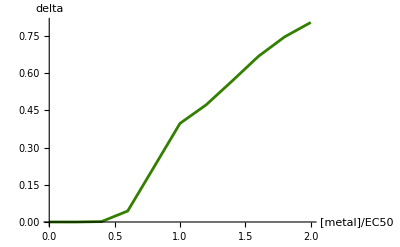

```mathematica
Clear[delta]
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

2.24443

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

1.12999

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

2.82307

#### MnZn growth data: a = 2.68*** [SLOW FOR a=0] - Delta at EC50 is 0.03 from the model fit

```mathematica
ypad="YPAD";
single1="Mn";
single2="Zn";
double="MnZn";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,0.344675},{0,0,0.342987},{0,0,0.346982},{0,0,0.341592},{0,0,0.327645},{0,0,0.299649},{0,0,0.3333},{0,0,0.30274},{0,0,0.286864},{0,0,0.347208}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.86,0,0.298582},{0.86,0,0.291635},{1.14,0,0.204455},{1.14,0,0.185045},{1.31,0,0.131089},{1.31,0,0.132071},{1.66,0,0.07621},{1.66,0,0.101139},{2.23,0,0.0603872},{2.23,0,0.0464464},{0.85,0,0.29107},{0.85,0,0.248948},{1.,0,0.193578},{1.,0,0.195635},{1.14,0,0.151442},{1.14,0,0.108769},{1.25,0,0.098664},{1.25,0,0.0744238},{1.6,0,0.045561},{1.6,0,0.057657}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,4.,0.251828},{0,4.,0.24125},{0,4.75,0.21202},{0,4.75,0.224034},{0,5.4,0.161238},{0,5.4,0.17015},{0,6.,0.0966768},{0,6.,0.104308},{0,6.6,0.0368801},{0,6.6,0.0420288},{0,3.33,0.235142},{0,3.33,0.242968},{0,4.,0.206083},{0,4.,0.210944},{0,4.8,0.144694},{0,4.8,0.171222},{0,5.4,0.106978},{0,5.4,0.100649},{0,6.,0.0567384},{0,6.,0.0524779}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.86,4.,0.231282},{0.86,4.,0.23967},{0.86,4.,0.248203},{1.14,4.75,0.19423},{1.14,4.75,0.192019},{1.14,4.75,0.20529},{1.31,5.4,0.170246},{1.31,5.4,0.141427},{1.31,5.4,0.156099},{1.66,6.,0.0999775},{1.66,6.,0.113476},{1.66,6.,0.0832259},{2.23,6.6,0.0653175},{2.23,6.6,0.0601639},{2.23,6.6,0.10127},{0.85,3.33,0.229049},{0.85,3.33,0.206395},{0.85,3.33,0.231676},{1.,4.,0.198229},{1.,4.,0.1894},{1.,4.,0.150793},{1.14,4.8,0.1571},{1.14,4.8,0.151207},{1.14,4.8,0.133677},{1.25,5.4,0.0932844},{1.25,5.4,0.0829948},{1.25,5.4,0.0893305},{1.6,6.,0.0437481},{1.6,6.,0.0532471},{1.6,6.,0.0399577}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86 | 0.86 | 1.14 | 1.14 | 1.31 | 1.31 | 1.66 | 1.66 | 2.23 | 2.23 | 0.85 | 0.85 | 1. | 1. | 1.14 | 1.14 | 1.25 | 1.25 | 1.6 | 1.6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86 | 0.86 | 0.86 | 1.14 | 1.14 | 1.14 | 1.31 | 1.31 | 1.31 | 1.66 | 1.66 | 1.66 | 2.23 | 2.23 | 2.23 | 0.85 | 0.85 | 0.85 | 1. | 1. | 1. | 1.14 | 1.14 | 1.14 | 1.25 | 1.25 | 1.25 | 1.6 | 1.6 | 1.6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4. | 4. | 4.75 | 4.75 | 5.4 | 5.4 | 6. | 6. | 6.6 | 6.6 | 3.33 | 3.33 | 4. | 4. | 4.8 | 4.8 | 5.4 | 5.4 | 6. | 6. | 4. | 4. | 4. | 4.75 | 4.75 | 4.75 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6. | 6.6 | 6.6 | 6.6 | 3.33 | 3.33 | 3.33 | 4. | 4. | 4. | 4.8 | 4.8 | 4.8 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6.
0.344675 | 0.342987 | 0.346982 | 0.341592 | 0.327645 | 0.299649 | 0.3333 | 0.30274 | 0.286864 | 0.347208 | 0.298582 | 0.291635 | 0.204455 | 0.185045 | 0.131089 | 0.132071 | 0.07621 | 0.101139 | 0.0603872 | 0.0464464 | 0.29107 | 0.248948 | 0.193578 | 0.195635 | 0.151442 | 0.108769 | 0.098664 | 0.0744238 | 0.045561 | 0.057657 | 0.251828 | 0.24125 | 0.21202 | 0.224034 | 0.161238 | 0.17015 | 0.0966768 | 0.104308 | 0.0368801 | 0.0420288 | 0.235142 | 0.242968 | 0.206083 | 0.210944 | 0.144694 | 0.171222 | 0.106978 | 0.100649 | 0.0567384 | 0.0524779 | 0.231282 | 0.23967 | 0.248203 | 0.19423 | 0.192019 | 0.20529 | 0.170246 | 0.141427 | 0.156099 | 0.0999775 | 0.113476 | 0.0832259 | 0.0653175 | 0.0601639 | 0.10127 | 0.229049 | 0.206395 | 0.231676 | 0.198229 | 0.1894 | 0.150793 | 0.1571 | 0.151207 | 0.133677 | 0.0932844 | 0.0829948 | 0.0893305 | 0.0437481 | 0.0532471 | 0.0399577)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{0.86,0.298582},{0.86,0.291635},{1.14,0.204455},{1.14,0.185045},{1.31,0.131089},{1.31,0.132071},{1.66,0.07621},{1.66,0.101139},{2.23,0.0603872},{2.23,0.0464464},{0.85,0.29107},{0.85,0.248948},{1.,0.193578},{1.,0.195635},{1.14,0.151442},{1.14,0.108769},{1.25,0.098664},{1.25,0.0744238},{1.6,0.045561},{1.6,0.057657}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→0.330552,EC501→1.14189,β1→4.37898}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{4.,0.251828},{4.,0.24125},{4.75,0.21202},{4.75,0.224034},{5.4,0.161238},{5.4,0.17015},{6.,0.0966768},{6.,0.104308},{6.6,0.0368801},{6.6,0.0420288},{3.33,0.235142},{3.33,0.242968},{4.,0.206083},{4.,0.210944},{4.8,0.144694},{4.8,0.171222},{5.4,0.106978},{5.4,0.100649},{6.,0.0567384},{6.,0.0524779}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→0.323794,EC502→4.86697,β2→4.57919}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{0.327173,1.14189,4.37898,4.86697,4.57919}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

0.608326

Minimizing the sum of squares fails to find a solution:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

FindMinimum::nrnum: The function value 249.943+6.97382 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {0.340047,1.12316,2.12317,5.6322,0.169771}.

FindMinimum::nrnum: The function value 1.51809×10^12+1.64519×10^6 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {0.340038,1.10807,2.16202,5.64288,0.127335}.

FindMinimum::nrnum: The function value -170.242-859.422 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {0.339177,1.13668,3.16637,6.281,0.035473}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::steperr: Error in step computation.

FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset⟦All,1⟧],0<β1<10,0<EC502<Max[dataset⟦All,2⟧],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

FindMaximum::nrnum: The function value 189701.-90987.3 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {0.339321,1.0987,2.58154,6.09075,0.0237849,0.0500778}.

FindMaximum::nrnum: The function value 1.24213×10^6-888914. ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {0.339303,1.10183,2.58072,6.09082,0.0356773,0.0501794}.

FindMaximum::nrnum: The function value 2.02754×10^6-2.92792×10^6 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {0.339293,1.10339,2.5803,6.09085,0.0416234,0.0502302}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{-67902.8,{max→0.329467,EC501→1.12985,β1→3.4663,EC502→6.56774,β2→0.0421949,σ→0.0416406}}

Restarting the sum of squares from the ML fit:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,max/.maxll[[2]]},{EC501,EC501/.maxll[[2]]},{β1,β1/.maxll[[2]]},{EC502,EC502/.maxll[[2]]},{β2,β2/.maxll[[2]]}}]
```

FindMinimum::nrnum: The function value 14976.2+7.80588×10^-8 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {0.329467,1.12985,3.4663,6.534,0.0420788}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{236.105,{max→0.329467,EC501→1.12985,β1→3.4663,EC502→6.534,β2→0.0421949}}

The fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-3.34615×10^-7,4.75692×10^-10,4.31367×10^-11,-0.513772,2.83148×10^-10}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{0.0775399,{max→0.327726,EC501→1.15076,β1→3.68617,EC502→4.80312,β2→3.95303,a→2.6789}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{164.044,{max→0.327726,EC501→1.15076,β1→3.68617,EC502→4.80312,β2→3.95302,a→2.6789,σ→0.0311328}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-0.0000497415,0.0000288,0.0000563664,0.0000264676,0.0000918869,4.66509×10^-6}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841, which ???

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

General::munfl: Exp[-68072.5] is too small to represent as a normalized machine number; precision may be lost.

0.

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/40},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction, the fit is much better:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.01,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.01,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.000181628,0.00272269,0.0116727,0.0274822,0.0446498,0.0582954,0.0676987,0.0740205,0.0784319,0.0817057}

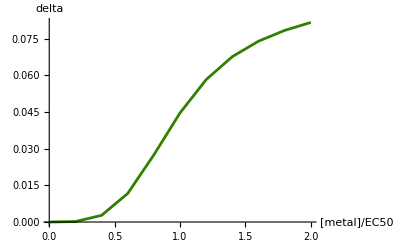

```mathematica
Clear[delta]
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

2.6789

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

1.15076

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

4.80312

#### NiZn growth data: a = 1.05***) - Delta at EC50 is 0.85 from the model fit

```mathematica
ypad="YPAD";
single1="Ni";
single2="Zn";
double="NiZn";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,0.344675},{0,0,0.342987},{0,0,0.346982},{0,0,0.341592},{0,0,0.327645},{0,0,0.299649},{0,0,0.3333},{0,0,0.30274},{0,0,0.286864},{0,0,0.347208}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{1.88,0,0.327391},{1.88,0,0.345335},{2.4,0,0.277617},{2.4,0,0.301498},{3.,0,0.161179},{3.,0,0.172964},{3.6,0,0.0728783},{3.6,0,0.0833834},{5.1,0,0.0532982},{5.1,0,0.0435607},{2.3,0,0.325228},{2.3,0,0.331102},{2.6,0,0.291454},{2.6,0,0.301508},{2.75,0,0.137243},{2.75,0,0.0999753},{3.,0,0.100496},{3.,0,0.0797609},{3.2,0,0.036418},{3.2,0,0.0401879}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,4.,0.251828},{0,4.,0.24125},{0,4.75,0.21202},{0,4.75,0.224034},{0,5.4,0.161238},{0,5.4,0.17015},{0,6.,0.0966768},{0,6.,0.104308},{0,6.6,0.0368801},{0,6.6,0.0420288},{0,3.33,0.235142},{0,3.33,0.242968},{0,4.,0.206083},{0,4.,0.210944},{0,4.8,0.144694},{0,4.8,0.171222},{0,5.4,0.106978},{0,5.4,0.100649},{0,6.,0.0567384},{0,6.,0.0524779}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{1.88,4.,0.0887735},{1.88,4.,0.104723},{1.88,4.,0.109658},{2.4,4.75,0.060949},{2.4,4.75,0.0782577},{2.4,4.75,0.0370452},{3.,5.4,0.0308787},{3.,5.4,0.0722687},{3.,5.4,0.0380227},{3.6,6.,0.041329},{3.6,6.,0.0193244},{3.6,6.,0.0106616},{5.1,6.6,0.0124091},{5.1,6.6,0.00655235},{5.1,6.6,0.0192873},{2.3,3.33,0.058755},{2.3,3.33,0.0962705},{2.3,3.33,0.0879127},{2.6,4.,0.0351495},{2.6,4.,0.0396626},{2.6,4.,0.0538145},{2.75,4.8,0.0171338},{2.75,4.8,0.0173267},{2.75,4.8,0.0320968},{3.,5.4,0.0163332},{3.,5.4,0.0186832},{3.,5.4,0.017687},{3.2,6.,0.0159238},{3.2,6.,0.0115529},{3.2,6.,0.0140392}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.88 | 1.88 | 2.4 | 2.4 | 3. | 3. | 3.6 | 3.6 | 5.1 | 5.1 | 2.3 | 2.3 | 2.6 | 2.6 | 2.75 | 2.75 | 3. | 3. | 3.2 | 3.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.88 | 1.88 | 1.88 | 2.4 | 2.4 | 2.4 | 3. | 3. | 3. | 3.6 | 3.6 | 3.6 | 5.1 | 5.1 | 5.1 | 2.3 | 2.3 | 2.3 | 2.6 | 2.6 | 2.6 | 2.75 | 2.75 | 2.75 | 3. | 3. | 3. | 3.2 | 3.2 | 3.2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4. | 4. | 4.75 | 4.75 | 5.4 | 5.4 | 6. | 6. | 6.6 | 6.6 | 3.33 | 3.33 | 4. | 4. | 4.8 | 4.8 | 5.4 | 5.4 | 6. | 6. | 4. | 4. | 4. | 4.75 | 4.75 | 4.75 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6. | 6.6 | 6.6 | 6.6 | 3.33 | 3.33 | 3.33 | 4. | 4. | 4. | 4.8 | 4.8 | 4.8 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6.
0.344675 | 0.342987 | 0.346982 | 0.341592 | 0.327645 | 0.299649 | 0.3333 | 0.30274 | 0.286864 | 0.347208 | 0.327391 | 0.345335 | 0.277617 | 0.301498 | 0.161179 | 0.172964 | 0.0728783 | 0.0833834 | 0.0532982 | 0.0435607 | 0.325228 | 0.331102 | 0.291454 | 0.301508 | 0.137243 | 0.0999753 | 0.100496 | 0.0797609 | 0.036418 | 0.0401879 | 0.251828 | 0.24125 | 0.21202 | 0.224034 | 0.161238 | 0.17015 | 0.0966768 | 0.104308 | 0.0368801 | 0.0420288 | 0.235142 | 0.242968 | 0.206083 | 0.210944 | 0.144694 | 0.171222 | 0.106978 | 0.100649 | 0.0567384 | 0.0524779 | 0.0887735 | 0.104723 | 0.109658 | 0.060949 | 0.0782577 | 0.0370452 | 0.0308787 | 0.0722687 | 0.0380227 | 0.041329 | 0.0193244 | 0.0106616 | 0.0124091 | 0.00655235 | 0.0192873 | 0.058755 | 0.0962705 | 0.0879127 | 0.0351495 | 0.0396626 | 0.0538145 | 0.0171338 | 0.0173267 | 0.0320968 | 0.0163332 | 0.0186832 | 0.017687 | 0.0159238 | 0.0115529 | 0.0140392)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{1.88,0.327391},{1.88,0.345335},{2.4,0.277617},{2.4,0.301498},{3.,0.161179},{3.,0.172964},{3.6,0.0728783},{3.6,0.0833834},{5.1,0.0532982},{5.1,0.0435607},{2.3,0.325228},{2.3,0.331102},{2.6,0.291454},{2.6,0.301508},{2.75,0.137243},{2.75,0.0999753},{3.,0.100496},{3.,0.0797609},{3.2,0.036418},{3.2,0.0401879}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→0.333202,EC501→2.83132,β1→11.6297}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,0.344675},{0,0.342987},{0,0.346982},{0,0.341592},{0,0.327645},{0,0.299649},{0,0.3333},{0,0.30274},{0,0.286864},{0,0.347208},{4.,0.251828},{4.,0.24125},{4.75,0.21202},{4.75,0.224034},{5.4,0.161238},{5.4,0.17015},{6.,0.0966768},{6.,0.104308},{6.6,0.0368801},{6.6,0.0420288},{3.33,0.235142},{3.33,0.242968},{4.,0.206083},{4.,0.210944},{4.8,0.144694},{4.8,0.171222},{5.4,0.106978},{5.4,0.100649},{6.,0.0567384},{6.,0.0524779}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→0.323794,EC502→4.86697,β2→4.57919}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{0.328498,2.83132,11.6297,4.86697,4.57919}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

0.120497

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{0.101815,{max→0.337693,EC501→2.85075,β1→9.09417,EC502→4.72274,β2→2.25939}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{153.15,{max→0.337693,EC501→2.85075,β1→9.09421,EC502→4.72274,β2→2.25938,σ→0.0356748}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.000035777,0.0000196126,-0.000450543,0.0000375725,0.000335663}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{0.0747449,{max→0.334378,EC501→2.83349,β1→9.99955,EC502→4.76208,β2→4.01883,a→1.04984}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<0.35,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{165.513,{max→0.334377,EC501→2.83349,β1→10.,EC502→4.76208,β2→4.01883,a→1.04985,σ→0.0305664}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{0.000137201,0.000017259,-0.00446052,-0.0000652223,0.0000878881,-0.0009705}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841, which it is:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

6.60662×10^-7

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.01,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.01,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction, the fit is much better:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.01,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.01,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.00130564,0.0529958,0.3489,0.71596,0.858318,0.899233,0.92815,0.950455,0.965612,0.975679}

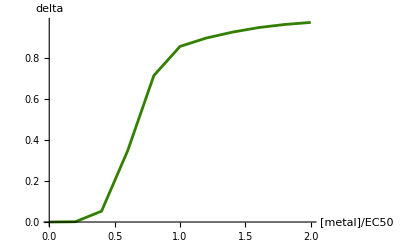

```mathematica
Clear[delta]
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

1.04985

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

2.83349

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

4.76208

## Overall plots of a’s and delta’s

#### Model parameters

```mathematica
doublelist={"CdCo","CdCu","CdMn","CdNi","CdZn","CoCu","CoMn","CoNi","CoZn","CuMn","CuNi","CuZn","MnNi","MnZn","NiZn"};
alist={-0.16207560765939727,-1.586796997134779,1.2528284963162748,0.8713577334340691,0.20364212368117826,-2.406461694324145,1.9322420937453406,0.8236100628124806,-0.017902299028275274,3.2526851042178415,-0.9788079808413033,-1.7573053558555443,2.244428525043177,2.678896184667141,1.049853881331315};
EClist1={0.018736276379950928,0.019265654573665053,0.01891041848385826,0.01831949500125162,0.01920348539973893,0.9404359841439289,0.9148074511405514,0.8922847617674775,0.9146726210541304,10.577397316047737,10.370598100119517,10.585657954261158,1.1299919898169093,1.150764365424742,2.833488837291872};
EClist2={0.9077114466097124,9.026499534318985,1.1478729416586386,2.834108341382413,4.8478594500814145,10.557811005528473,1.1451240250001888,2.8287674654657176,4.798365546154581,1.2010890103990082,2.8619788277266056,5.0158979931801815,2.8230700015995818,4.80311598621097,4.762079220938416};
```

```mathematica
Table[a[doublelist[[i]]]=alist[[i]],{i,1,Length[doublelist]}]
```

{-0.162076,-1.5868,1.25283,0.871358,0.203642,-2.40646,1.93224,0.82361,-0.0179023,3.25269,-0.978808,-1.75731,2.24443,2.6789,1.04985}

{-0.162076,-1.5868,1.25283,0.871358,0.203642,-2.40646,1.93224,0.82361,3.25269,3.25269,-0.978808,-1.75731,2.24443,2.6789,1.04985}

```mathematica
Table[EC501[doublelist[[i]]]=EClist1[[i]],{i,1,Length[doublelist]}]
```

{0.0187363,0.0192657,0.0189104,0.0183195,0.0192035,0.940436,0.914807,0.892285,0.914673,10.5774,10.3706,10.5857,1.12999,1.15076,2.83349}

{0.0187363,0.0192657,0.0189104,0.0183195,0.0192035,0.940436,0.914807,0.892285,0.914673,10.5774,10.3706,10.5857,1.12999,1.15076,2.83349}

```mathematica
Table[EC502[doublelist[[i]]]=EClist2[[i]],{i,1,Length[doublelist]}]
```

{0.907711,9.0265,1.14787,2.83411,4.84786,10.5578,1.14512,2.82877,4.79837,1.20109,2.86198,5.0159,2.82307,4.80312,4.76208}

{0.907711,9.0265,1.14787,2.83411,4.84786,10.5578,1.14512,2.82877,4.79837,1.20109,2.86198,5.0159,2.82307,4.80312,4.76208}

```mathematica
delta["CdCo"]={0,0.10827707499413308,0.3217732111905146,0.4927416439085882,0.5983426967535386,0.6610481049200359,0.700072390854461,0.7263151115990887,0.74542454956453,0.7603122534358895,0.7725237257826281};
```

```mathematica
delta["CdCu"]={0,0.25117099410040333,0.47940053274867167,0.6098803196803291,0.6836241935235392,0.7282170936724697,0.7574833398729066,0.7782403821627302,0.7939670143670947,0.8065230846515633,0.8169542267125915};
```

```mathematica
delta["CdMn"]={0,0.02212847450358635,0.1251215550465994,0.2782946419999601,0.4067513206473743,0.48730431387750983,0.5366913287078985,0.5728839364931779,0.6044273319230533,0.6338240491782485,0.6613633330850873};
```

```mathematica
delta["CdNi"]={0,0.029621224720458694,0.15969242322459543,0.38308126548557253,0.591812506318279,0.6788484340374352,0.7154099521319002,0.8031141730716084,0.8838257385608115,0.9351821774415908,0.9644537085312099};
```

```mathematica
delta["CdZn"]={0,0.05540061563564169,0.2656321427163345,0.49897837584199123,0.6478850044633985,0.7262933055816047,0.7690906581775361,0.7966975328246797,0.8177295670333136,0.8353098664376719,0.8505454593272073};
```

```mathematica
delta["CoCu"]={0,0.15237400902204612,0.886736621716457,0.9855346818797032,0.9963079398926724,0.9983184235728658,0.9988515096535601,0.9990331821767569,0.999109506831236,0.9991483444973389,0.9991719489831679};
```

```mathematica
delta["CoMn"]={0,0.0016187931864887206,0.028573093294404273,0.12912187971990385,0.2854489817007234,0.41543495150899923,0.4925660607758221,0.5335427188822239,0.5553041710342899,0.5673118993134165,0.5742593614501839};
```

```mathematica
delta["CoNi"]={0,0.007267745361119404,0.11052280851669438,0.4181045146221485,0.7109175324761807,0.8292509808597885,0.8706199645165653,0.9110885925369834,0.9434441982312719,0.9643171036054368,0.977168338807143};
```

```mathematica
delta["CoZn"]={0,0.030943279737301932,0.2850063614541659,0.6150923422334912,0.7872869481111242,0.8585402071058871,0.889366293154719,0.9040895002287193,0.911832599199302,0.9162621271992731,0.9189874849165732};
```

```mathematica
delta["CuMn"]={0,-0.0006798190100827384,-0.008335573525298345,-0.038275409963322016,-0.11694085080154082,-0.25961615145904426,-0.4210146369750347,-0.5353555077780714,-0.5848824073054559,-0.5857246471658262,-0.5577361395403164};
```

```mathematica
delta["CuNi"]={0,0.009861206480205609,0.5363327994079163,0.9540124065902795,0.9934562582473776,0.9979830630152132,0.998801037991336,0.9991503234226288,0.9993802375617546,0.9995392729695021,0.9996511445538176};
```

```mathematica
delta["CuZn"]={0,0.07051922552485146,0.7613420294704198,0.9645327150868112,0.9906702506729448,0.9957033460695143,0.9970557125455202,0.9975216885585169,0.9977202032385716,0.9978230700295012,0.9978868748285767};
```

```mathematica
delta["MnNi"]={0,-0.00010827982690098104,0.0016450454559894245,0.04418696264902555,0.22047093498476356,0.3974373294748854,0.47222759331255637,0.568937909569034,0.6679058311252735,0.7462657842149341,0.804398945304965};
```

```mathematica
delta["MnZn"]={0,0.00018162818630362842,0.0027226943111329227,0.011672702314355354,0.027482220409489222,0.04464981649825117,0.058295407428381685,0.0676987475402403,0.07402053814698872,0.07843194176541479,0.08170569765670088};
```

```mathematica
delta["NiZn"]={0,0.001305643477307994,0.052995844831336014,0.3488999767151746,0.7159596427177511,0.8583176834165439,0.8992330763499785,0.9281503822568314,0.9504554761696118,0.9656122276153626,0.9756787318012213};
```

```mathematica
Join[{Flatten[{"Conc/EC50",Table[TRYc//N,{TRYc,0,2,1/5}]}]},
Table[Flatten[{doublelist[[i]],delta[doublelist[[i]]]}],{i,1,15}]];
Export["DeltaTable.csv",%];
```

Metal combo, estimated “a”, delta value at EC50:

```mathematica
Table[{doublelist[[i]],a[doublelist[[i]]],delta[doublelist[[i]]][[6]],EC501[doublelist[[i]]],EC502[doublelist[[i]]]},{i,1,15}];
Join[{{"Combo","a","delta[EC50]","EC501","EC502"}},%]//MatrixForm
Export["ParameterTable.csv",Join[{{"Combo","a","delta[EC50]","EC501","EC502"}},%%]];
```

(Combo | a | delta[EC50] | EC501 | EC502
CdCo | -0.162076 | 0.661048 | 0.0187363 | 0.907711
CdCu | -1.5868 | 0.728217 | 0.0192657 | 9.0265
CdMn | 1.25283 | 0.487304 | 0.0189104 | 1.14787
CdNi | 0.871358 | 0.678848 | 0.0183195 | 2.83411
CdZn | 0.203642 | 0.726293 | 0.0192035 | 4.84786
CoCu | -2.40646 | 0.998318 | 0.940436 | 10.5578
CoMn | 1.93224 | 0.415435 | 0.914807 | 1.14512
CoNi | 0.82361 | 0.829251 | 0.892285 | 2.82877
CoZn | -0.0179023 | 0.85854 | 0.914673 | 4.79837
CuMn | 3.25269 | -0.259616 | 10.5774 | 1.20109
CuNi | -0.978808 | 0.997983 | 10.3706 | 2.86198
CuZn | -1.75731 | 0.995703 | 10.5857 | 5.0159
MnNi | 2.24443 | 0.397437 | 1.12999 | 2.82307
MnZn | 2.6789 | 0.0446498 | 1.15076 | 4.80312
NiZn | 1.04985 | 0.858318 | 2.83349 | 4.76208)

The above rounded:

```mathematica
Table[{doublelist[[i]],1/100.*Round[100a[doublelist[[i]]]],1/100.*Round[100delta[doublelist[[i]]][[6]]],1/100.*Round[100EC501[doublelist[[i]]]],1/100.*Round[100EC502[doublelist[[i]]]]},{i,1,15}];
Join[{{"Combo","a","delta[EC50]","EC501","EC502"}},%]//MatrixForm
```

(Combo | a | delta[EC50] | EC501 | EC502
CdCo | -0.16 | 0.66 | 0.02 | 0.91
CdCu | -1.59 | 0.73 | 0.02 | 9.03
CdMn | 1.25 | 0.49 | 0.02 | 1.15
CdNi | 0.87 | 0.68 | 0.02 | 2.83
CdZn | 0.2 | 0.73 | 0.02 | 4.85
CoCu | -2.41 | 1. | 0.94 | 10.56
CoMn | 1.93 | 0.42 | 0.91 | 1.15
CoNi | 0.82 | 0.83 | 0.89 | 2.83
CoZn | -0.02 | 0.86 | 0.91 | 4.8
CuMn | 3.25 | -0.26 | 10.58 | 1.2
CuNi | -0.98 | 1. | 10.37 | 2.86
CuZn | -1.76 | 1. | 10.59 | 5.02
MnNi | 2.24 | 0.4 | 1.13 | 2.82
MnZn | 2.68 | 0.04 | 1.15 | 4.8
NiZn | 1.05 | 0.86 | 2.83 | 4.76)

Relationship between delta and a (from the fitted functions) for each metal at their EC50:

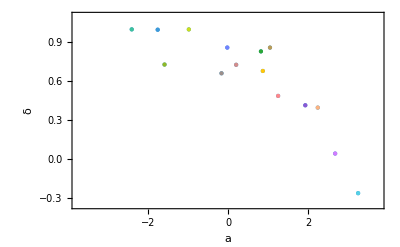

```mathematica
Show[
ListPlot[Table[Style[{a[doublelist[[i]]],delta[doublelist[[i]]][[6]]},color[doublelist[[i]]]],{i,1,15}],PlotRange->{{-3.75,3.75},{-0.35,1.1}},AxesLabel->{"a","δ"},PlotStyle->PointSize[Large]],
Frame->True]
```

Relationship between delta and a (from the fitted functions) for each metal at different fractions of their EC50 (numbers in the bottom left):

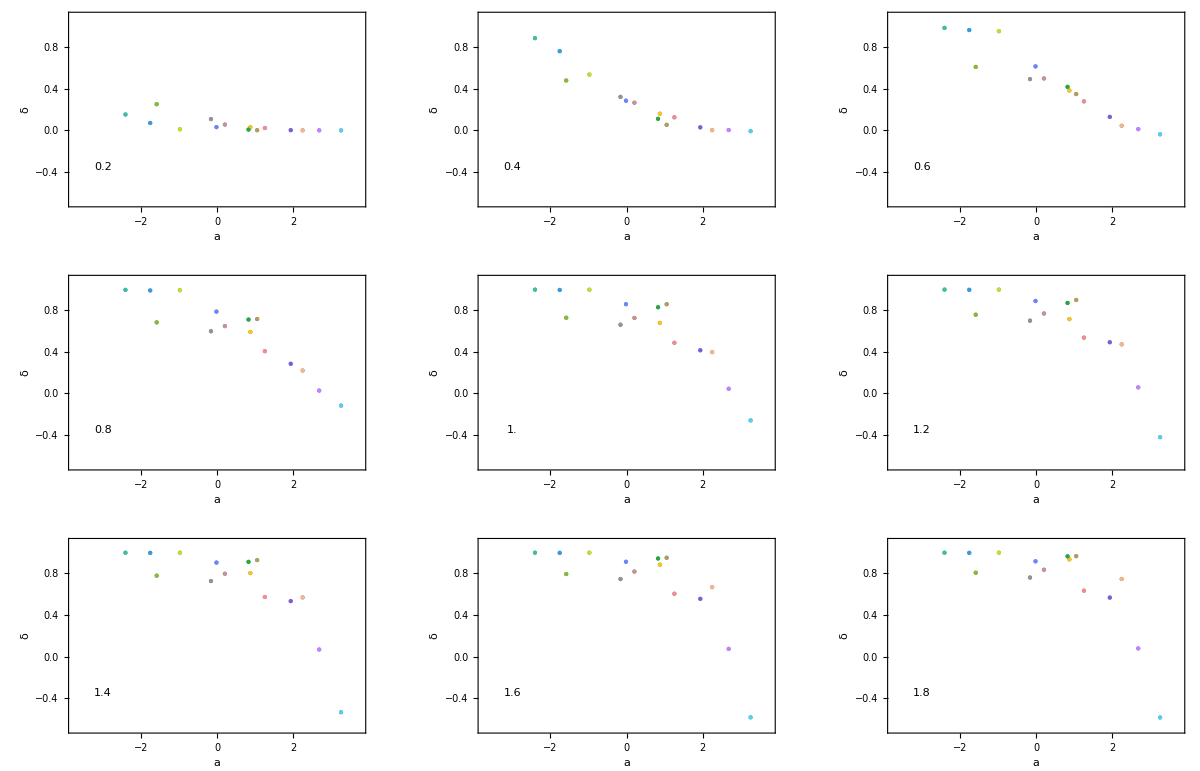

```mathematica
GraphicsGrid[Partition[Table[
Show[
ListPlot[Table[Style[{a[doublelist[[i]]],delta[doublelist[[i]]][[ii]]},color[doublelist[[i]]]],{i,1,15}],PlotRange->{{-3.75,3.75},{-0.7,1.1}},AxesLabel->{"a","δ"},PlotStyle->PointSize[Large]],
Graphics[Text[Round[10(ii-1)/5.]/10.,{-3,-0.35}]],
Frame->True],{ii,2,11}],3]]
```

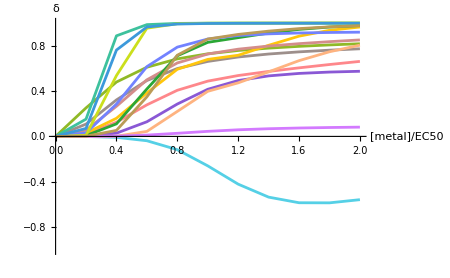

```mathematica
Show[
Table[ListPlot[Table[{(i-1)/5, delta[doublelist[[j]]][[i]]},{i,1,11}],Joined->True,PlotStyle->color[doublelist[[j]]]],{j,1,15}],PlotRange->{{0,2},{-1,1}},AxesLabel->{"[metal]/EC50","δ"},ImageSize->450
]
```

Legend ordered by delta

```mathematica
Sort[Table[{delta[doublelist[[i]]][[6]],Text[Style[doublelist[[i]],color[doublelist[[i]]]]]},{i,1,15}],#1[[1]]>#2[[1]]&][[All,2]]//MatrixForm
```

(CoCu
CuNi
CuZn
CoZn
NiZn
CoNi
CdCu
CdZn
CdNi
CdCo
CdMn
CoMn
MnNi
MnZn
CuMn)

```mathematica
Export["file.png",MatrixForm[%]];
```

Alphabetical order

```mathematica
Table[Text[Style[doublelist[[i]],color[doublelist[[i]]]]],{i,1,15}]//MatrixForm
```

(CdCo
CdCu
CdMn
CdNi
CdZn
CoCu
CoMn
CoNi
CoZn
CuMn
CuNi
CuZn
MnNi
MnZn
NiZn)

#### ML estimates

```mathematica
doublelist={"CdCo","CdCu","CdMn","CdNi","CdZn","CoCu","CoMn","CoNi","CoZn","CuMn","CuNi","CuZn","MnNi","MnZn","NiZn"};
alist={-0.16207560765939727,-1.586796997134779,1.2528284963162748,0.8713577334340691,0.20364212368117826,-2.406461694324145,1.9322420937453406,0.8236100628124806,-0.017902299028275274,3.2526851042178415,-0.9788079808413033,-1.7573053558555443,2.244428525043177,2.678896184667141,1.049853881331315};
EClist1={0.018736276379950928,0.019265654573665053,0.01891041848385826,0.01831949500125162,0.01920348539973893,0.9404359841439289,0.9148074511405514,0.8922847617674775,0.9146726210541304,10.577397316047737,10.370598100119517,10.585657954261158,1.1299919898169093,1.150764365424742,2.833488837291872};
EClist2={0.9077114466097124,9.026499534318985,1.1478729416586386,2.834108341382413,4.8478594500814145,10.557811005528473,1.1451240250001888,2.8287674654657176,4.798365546154581,1.2010890103990082,2.8619788277266056,5.0158979931801815,2.8230700015995818,4.80311598621097,4.762079220938416};
```

```mathematica
Clear[maxlla]
```

```mathematica
maxlla["CdCo"]={max->0.3280029496736121,EC501->0.018736276379950928,β1->1.7270640310822016,EC502->0.9077114466097124,β2->2.757004098587299,a->-0.16207560765939727,σ->0.034847446674785815};
```

```mathematica
maxlla["CdCu"]={max->0.32225212888054117,EC501->0.019265654573665053,β1->2.223374017721801,EC502->9.026499534318985,β2->1.286229926427697,a->-1.586796997134779,σ->0.040551244587866825}
```

{max→0.322252,EC501→0.0192657,β1→2.22337,EC502→9.0265,β2→1.28623,a→-1.5868,σ→0.0405512}

```mathematica
maxlla["CdMn"]={max->0.3268219624073715,EC501->0.01891041848385826,β1->2.0839255907627585,EC502->1.1478729416586386,β2->4.033830907463281,a->1.2528284963162748,σ->0.026845755164951583};
```

```mathematica
maxlla["CdNi"]={max->0.33346572586486095,EC501->0.01831949500125162,β1->1.784631950670648,EC502->2.834108341382413,β2->9.999993559833296,a->0.8713577334340691,σ->0.031974769004220874};
```

```mathematica
maxlla["CdZn"]={max->0.3219738663250109,EC501->0.01920348539973893,β1->2.103408589128545,EC502->4.8478594500814145,β2->4.063881317634939,a->0.20364212368117826,σ->0.02681824434389635};
```

```mathematica
maxlla["CoCu"]={max->0.3080525838486166,EC501->0.9404359841439289,β1->5.121604890256692,EC502->10.557811005528473,β2->5.831493700986609,a->-2.406461694324145,σ->0.03517494659686725};
```

```mathematica
maxlla["CoMn"]={max->0.3283301093144441,EC501->0.9148074511405514,β1->4.244623757023804,EC502->1.1451240250001888,β2->4.174558250222148,a->1.9322420937453406,σ->0.03129835076090487};
```

```mathematica
maxlla["CoNi"]={max->0.33685660130376877,EC501->0.8922847617674775,β1->2.9120536691995955,EC502->2.8287674654657176,β2->9.833370868900108,a->0.8236100628124806,σ->0.03793130909874147};
```

```mathematica
maxlla["CoZn"]={max->0.3275935484393056,EC501->0.9146726210541304,β1->3.5230048852838123,EC502->4.798365546154581,β2->3.87142677394647,a->-0.017902299028275274,σ->0.030432554021979117};
```

```mathematica
maxlla["CuMn"]={max->0.30450061704182574,EC501->10.577397316047737,β1->5.391497402271354,EC502->1.2010890103990082,β2->3.767791810053966,a->3.2526851042178415,σ->0.039770998898467656};
```

```mathematica
maxlla["CuNi"]={max->0.3211471603238742,EC501->10.370598100119517,β1->5.438531298804046,EC502->2.8619788277266056,β2->9.999999955952667,a->-0.9788079808413033,σ->0.03878225008246167};
```

```mathematica
maxlla["CuZn"]={max->0.3058810194682505,EC501->10.585657954261158,β1->5.81709789624673,EC502->5.0158979931801815,β2->5.051447480764886,a->-1.7573053558555443,σ->0.034260881677777126};
```

```mathematica
maxlla["MnNi"]={max->0.3386819329526596,EC501->1.1299919898169093,β1->4.612569674444448,EC502->2.8230700015995818,β2->9.999990899681633,a->2.244428525043177,σ->0.03337256375295551};
```

```mathematica
maxlla["MnZn"]={max->0.32772587373908835,EC501->1.150764365424742,β1->3.6861710274085597,EC502->4.80311598621097,β2->3.9530236302286066,a->2.678896184667141,σ->0.031132759095034043};
```

```mathematica
maxlla["NiZn"]={max->0.3343774581540495,EC501->2.833488837291872,β1->9.999999891760398,EC502->4.762079220938416,β2->4.018827706589222,a->1.049853881331315,σ->0.030566425241679608};
```

```mathematica
comboexperimentmet1_concmet2_concwells_grewCdCo10.00821.1480CdCu10.008211.324CdMn10.0152.9580CdNi10.015320CdZn10.00824.280CoCu10.6100CoMn11.52.9530CoNi11.14280CoZn11.144.20CuMn1122.9517CuNi1101.40CuZn1102.250MnNi12.95328MnZn13.85100NiZn124.27CdCo20.0151.1480CdMn20.0223.411CdZn20.0155.151CoCu20.518.517CoNi21.530CoZn20.963.571CuNi28.51.190CuZn28.51.910MnZn23.278.50
```

{{combo,experiment,met1_conc,met2_conc,wells_grew},{CdCo,1,0.0082,1.14,80},{CdCu,1,0.0082,11.3,24},{CdMn,1,0.015,2.95,80},{CdNi,1,0.015,3,20},{CdZn,1,0.0082,4.2,80},{CoCu,1,0.6,10,0},{CoMn,1,1.5,2.95,30},{CoNi,1,1.14,2,80},{CoZn,1,1.14,4.2,0},{CuMn,1,12,2.95,17},{CuNi,1,10,1.4,0},{CuZn,1,10,2.25,0},{MnNi,1,2.95,3,28},{MnZn,1,3.85,10,0},{NiZn,1,2,4.2,7},{CdCo,2,0.015,1.14,80},{CdMn,2,0.022,3.4,11},{CdZn,2,0.015,5.15,1},{CoCu,2,0.51,8.5,17},{CoNi,2,1.5,3,0},{CoZn,2,0.96,3.57,1},{CuNi,2,8.5,1.19,0},{CuZn,2,8.5,1.91,0},{MnZn,2,3.27,8.5,0}}

```mathematica
conc={{"CdCo","1","0.0082","1.14","80"},{"CdCu","1","0.0082","11.3","24"},{"CdMn","1","0.015","2.95","80"},{"CdNi","1","0.015","3","20"},{"CdZn","1","0.0082","4.2","80"},{"CoCu","1","0.6","10","0"},{"CoMn","1","1.5","2.95","30"},{"CoNi","1","1.14","2","80"},{"CoZn","1","1.14","4.2","0"},{"CuMn","1","12","2.95","17"},{"CuNi","1","10","1.4","0"},{"CuZn","1","10","2.25","0"},{"MnNi","1","2.95","3","28"},{"MnZn","1","3.85","10","0"},{"NiZn","1","2","4.2","7"},{"CdCo","2","0.015","1.14","80"},{"CdMn","2","0.022","3.4","11"},{"CdZn","2","0.015","5.15","1"},{"CoCu","2","0.51","8.5","17"},{"CoNi","2","1.5","3","0"},{"CoZn","2","0.96","3.57","1"},{"CuNi","2","8.5","1.19","0"},{"CuZn","2","8.5","1.91","0"},{"MnZn","2","3.27","8.5","0"}};
```

```mathematica
tabpred=Join[{{"combo","experiment","wells_grew","met1_conc","met2_conc","met1_conc/EC501","met2_conc/EC501","pred r1","pred r2","pred rcombo"}},Table[{conc[[ii,1]],conc[[ii,2]],ToExpression[conc[[ii,5]]],ToExpression[conc[[ii,3]]],ToExpression[conc[[ii,4]]],ToExpression[conc[[ii,3]]]/(EC501/.maxlla[conc[[ii,1]]]),ToExpression[conc[[ii,4]]]/(EC502/.maxlla[conc[[ii,1]]]),Chop[findY[{ToExpression[conc[[ii,3]]],0},{max,EC501,β1,EC502,β2}/.maxlla[conc[[ii,1]]],a/.maxlla[conc[[ii,1]]]]],
Chop[findY[{0,ToExpression[conc[[ii,4]]]},{max,EC501,β1,EC502,β2}/.maxlla[conc[[ii,1]]],a/.maxlla[conc[[ii,1]]]]],
Chop[findY[{ToExpression[conc[[ii,3]]],ToExpression[conc[[ii,4]]]},{max,EC501,β1,EC502,β2}/.maxlla[conc[[ii,1]]],a/.maxlla[conc[[ii,1]]]]]},{ii,1,Length[conc]}]];
```

```mathematica
Export["table.csv",tabpred];
```

```mathematica
TableForm[tabpred]
```

combo | experiment | wells_grew | met1_conc | met2_conc | met1_conc/EC501 | met2_conc/EC501 | pred r1 | pred r2 | pred rcombo
CdCo | 1 | 80 | 0.0082 | 1.14 | 0.437654 | 1.25591 | 0.264519 | 0.114118 | 0.067454
CdCu | 1 | 24 | 0.0082 | 11.3 | 0.425628 | 1.25187 | 0.280295 | 0.138009 | 0.0745822
CdMn | 1 | 80 | 0.015 | 2.95 | 0.793214 | 2.56997 | 0.202107 | 0.00709893 | 0.0103176
CdNi | 1 | 20 | 0.015 | 3 | 0.8188 | 1.05853 | 0.196164 | 0.120549 | 0.0565046
CdZn | 1 | 80 | 0.0082 | 4.2 | 0.427006 | 0.866362 | 0.275905 | 0.206627 | 0.109176
CoCu | 1 | 0 | 0.6 | 10 | 0.638002 | 0.947166 | 0.280026 | 0.178202 | 0.000974045
CoMn | 1 | 30 | 1.5 | 2.95 | 1.63969 | 2.57614 | 0.0358518 | 0.00620033 | 0.0052688
CoNi | 1 | 80 | 1.14 | 2 | 1.27762 | 0.707022 | 0.110771 | 0.326074 | 0.0386657
CoZn | 1 | 0 | 1.14 | 4.2 | 1.24635 | 0.875298 | 0.103264 | 0.205115 | 0.0193124
CuMn | 1 | 17 | 12 | 2.95 | 1.13449 | 2.4561 | 0.102369 | 0.00997148 | 0.0250319
CuNi | 1 | 0 | 10 | 1.4 | 0.964265 | 0.489172 | 0.176411 | 0.320895 | 0.00646418
CuZn | 1 | 0 | 10 | 2.25 | 0.944674 | 0.448574 | 0.17803 | 0.300641 | 0.00564631
MnNi | 1 | 28 | 2.95 | 3 | 2.61064 | 1.06267 | 0.00400273 | 0.1194 | 0.00283407
MnZn | 1 | 0 | 3.85 | 10 | 3.3456 | 2.08198 | 0.00377724 | 0.017111 | 0.005858
NiZn | 1 | 7 | 2 | 4.2 | 0.705844 | 0.881968 | 0.324419 | 0.208511 | 0.0815663
CdCo | 2 | 80 | 0.015 | 1.14 | 0.800586 | 1.25591 | 0.195118 | 0.114118 | 0.0491515
CdMn | 2 | 11 | 0.022 | 3.4 | 1.16338 | 2.962 | 0.137856 | 0.00404214 | 0.00619775
CdZn | 2 | 1 | 0.015 | 5.15 | 0.781108 | 1.06232 | 0.201897 | 0.141309 | 0.0501965
CoCu | 2 | 17 | 0.51 | 8.5 | 0.542302 | 0.805091 | 0.2952 | 0.240207 | 0.00238757
CoNi | 2 | 0 | 1.5 | 3 | 1.68108 | 1.06053 | 0.0608196 | 0.12107 | 0.00867565
CoZn | 2 | 1 | 0.96 | 3.57 | 1.04956 | 0.744003 | 0.149875 | 0.2485 | 0.0340188
CuNi | 2 | 0 | 8.5 | 1.19 | 0.819625 | 0.415796 | 0.239842 | 0.321098 | 0.0183558
CuZn | 2 | 0 | 8.5 | 1.91 | 0.802973 | 0.380789 | 0.239152 | 0.303568 | 0.0136165
MnZn | 2 | 0 | 3.27 | 8.5 | 2.84159 | 1.76968 | 0.0068306 | 0.0310683 | 0.0107027

```mathematica
lm=LinearModelFit[Transpose[{tabpred[[2;;All,10]],tabpred[[2;;All,3]]}],{x},x]
```

FittedModel[…]

```mathematica
lm["ParameterEstimates"]
```

```mathematica
Normal[lm]
```

9.08072+480.914 x

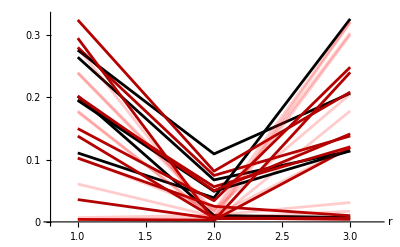

```mathematica
Show[Table[ListPlot[{tabpred[[i,8]],tabpred[[i,10]],tabpred[[i,9]]},Joined->True,AxesLabel->{"r",""},Ticks->{"metal1","combo","metal2"},PlotStyle->(If[tabpred[[i,3]]==0,RGBColor[1,0,0,0.2],If[tabpred[[i,3]]==80,RGBColor[0,0,0],RGBColor[0.7,0,0]]]),PlotRange->{{0.8,3.2},{0.,0.33}}],{i,2,Length[tabpred]}]]
```

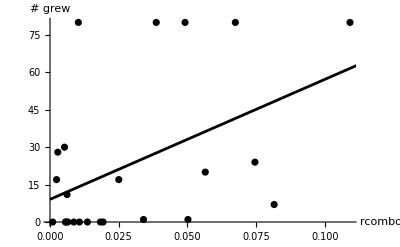

```mathematica
Show[
ListPlot[Transpose[{tabpred[[2;;All,10]],tabpred[[2;;All,3]]}],AxesLabel->{"rcombo","# grew"},PlotStyle->Black],
Plot[Normal[lm],{x,0,0.12},PlotStyle->Black]
]
```

Randomly permuting the y values and computing the slope:

```mathematica
SeedRandom[13453];
tabrandom=Table[temp=LinearModelFit[Transpose[{tabpred[[2;;All,10]],RandomSample[tabpred[[2;;All,3]]]}],{x},x];
temp["ParameterEstimates"][2, "BestFitParameter"]//Normal,{i,1,1000}];
```

```mathematica
{Quantile[tabrandom,0.025],Quantile[tabrandom,0.975]}
```

{-380.355,442.418}

p-value by randomization:

```mathematica
Select[tabrandom,#>(lm["ParameterEstimates"][2, "BestFitParameter"]//Normal)&];
Length[%]/1000.//PercentForm
```

1.5%

#### Observed and estimated delta for the 5 target concentrations

In Chapter 3, Penny aimed for single metal concentrations in increasing strenghts, corresponding to growth rates of {0.25, 0.2, 0.15, 0.1, 0.05}:

```mathematica
targetconc={1,2,3,4,5};
```

The following uses
	datafile=Import["vgraph_growthrates_unavg_mM_19Feb25.csv"];
from which each single metal is obtained from the first two then second two letters in the double metal list.  The concentrations used and average growth rates measured for the five concentrations are obtained using all technical replicates within a trial, along with the observed and predicted delta, using the ML estimates of the full model (including a). The two separate trials are treated separately.

Estimating delta for this function the x-axis measures concentrations in units of EC50:

```mathematica
Clear[targetdelta,conc1,conc2]
For[TRYtrial=1,TRYtrial≤2,TRYtrial=TRYtrial+1,
trial=If[TRYtrial==1,"one","two"];
For[TRYmetal=1,TRYmetal≤Length[doublelist],TRYmetal=TRYmetal+1,
For[TRYconc=1,TRYconc≤5,TRYconc=TRYconc+1,
(*Properties of first metal:*)
temp1=Select[datafile,(#[[1]]==StringTake[doublelist[[TRYmetal]],2])&&(#[[2]]==TRYconc)&&(#[[3]]==trial)&];
conc1[TRYmetal,TRYconc,TRYtrial]=Mean[temp1[[All,4]]];
r1[TRYmetal,TRYconc,TRYtrial]=Mean[temp1[[All,9]]];
(*Properties of second metal:*)
expr1[TRYmetal,TRYconc,TRYtrial]=Chop[findY[{conc1[TRYmetal,TRYconc,TRYtrial],0},{max,EC501,β1,EC502,β2}/.maxlla[doublelist[[TRYmetal]]],a/.maxlla[doublelist[[TRYmetal]]]]];
temp2=Select[datafile,(#[[1]]==StringTake[doublelist[[TRYmetal]],-2])&&(#[[2]]==TRYconc)&&(#[[3]]==trial)&];
conc2[TRYmetal,TRYconc,TRYtrial]=Mean[temp2[[All,4]]];
r2[TRYmetal,TRYconc,TRYtrial]=Mean[temp2[[All,9]]];
expr2[TRYmetal,TRYconc,TRYtrial]=Chop[findY[{0,conc2[TRYmetal,TRYconc,TRYtrial]},{max,EC501,β1,EC502,β2}/.maxlla[doublelist[[TRYmetal]]],a/.maxlla[doublelist[[TRYmetal]]]]];
(*Properties of combo:*)
temp12=Select[datafile,(#[[1]]==doublelist[[TRYmetal]])&&(#[[2]]==TRYconc)&&(#[[3]]==trial)&];
r12[TRYmetal,TRYconc,TRYtrial]=Mean[temp12[[All,9]]];
expr12[TRYmetal,TRYconc,TRYtrial]=Chop[findY[{conc1[TRYmetal,TRYconc,TRYtrial],conc2[TRYmetal,TRYconc,TRYtrial]},{max,EC501,β1,EC502,β2}/.maxlla[doublelist[[TRYmetal]]],a/.maxlla[doublelist[[TRYmetal]]]]];
observeddelta[TRYmetal,TRYconc,TRYtrial]=1-2 r12[TRYmetal,TRYconc,TRYtrial]/(r1[TRYmetal,TRYconc,TRYtrial]+r2[TRYmetal,TRYconc,TRYtrial]);
targetdelta[TRYmetal,TRYconc,TRYtrial]=Chop[1-2 expr12[TRYmetal,TRYconc,TRYtrial]/(expr1[TRYmetal,TRYconc,TRYtrial]+expr2[TRYmetal,TRYconc,TRYtrial])]
]
]
];
```

```mathematica
Join[{{"metal","conc","trial","met1_mM","met2_mM","obs_r1","obs_r2","obs_r12","obs_delta","exp_r1","exp_r2","exp_r12","exp_delta"}},Flatten[Table[{doublelist[[TRYmetal]],TRYconc,If[TRYtrial==1,"one","two"],conc1[TRYmetal,TRYconc,TRYtrial],conc2[TRYmetal,TRYconc,TRYtrial],r1[TRYmetal,TRYconc,TRYtrial],r2[TRYmetal,TRYconc,TRYtrial],r12[TRYmetal,TRYconc,TRYtrial],observeddelta[TRYmetal,TRYconc,1],expr1[TRYmetal,TRYconc,TRYtrial],expr2[TRYmetal,TRYconc,TRYtrial],expr12[TRYmetal,TRYconc,TRYtrial],targetdelta[TRYmetal,TRYconc,TRYtrial]},{TRYtrial,1,2},{TRYmetal,1,Length[doublelist]},{TRYconc,1,5}],2]];
```

```mathematica
Export["vgraph_growthrates_predictions_mM_20Apr25.csv",%];
```

Observed delta* (averaged over two trials) vs mean r in those two single environments:

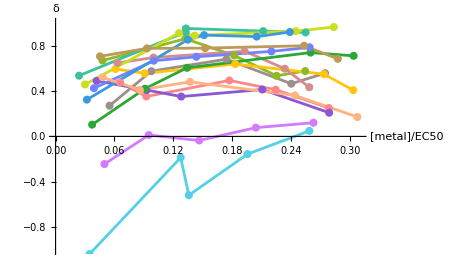

```mathematica
plot1=Show[
Table[ListPlot[Sort[Table[{Mean[Table[(r1[j,i,k]+r2[j,i,k])/2,{k,1,2}]],Mean[Table[observeddelta[j,i,k],{k,1,2}]]},{i,1,5}]],Joined->True,PlotStyle->color[doublelist[[j]]]],{j,1,15}],
Table[ListPlot[Sort[Table[{Mean[Table[(r1[j,i,k]+r2[j,i,k])/2,{k,1,2}]],Mean[Table[observeddelta[j,i,k],{k,1,2}]]},{i,1,5}]],PlotStyle->color[doublelist[[j]]]],{j,1,15}],
PlotRange->{{0,0.31},{-1,1}},AxesLabel->{"[metal]/EC50","δ"},ImageSize->450,AxesOrigin->{0,0}
]
```

Expected delta* (averaged over two trials) vs mean r in those two single environments:

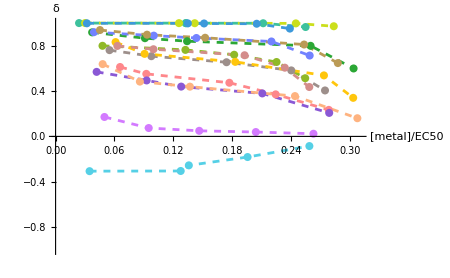

```mathematica
plot2=Show[
Table[ListPlot[Sort[Table[{Mean[Table[(r1[j,i,k]+r2[j,i,k])/2,{k,1,2}]],Mean[Table[targetdelta[j,i,k],{k,1,2}]]},{i,1,5}]],Joined->True,PlotStyle->{Dashed,color[doublelist[[j]]]}],{j,1,15}],
Table[ListPlot[Sort[Table[{Mean[Table[(r1[j,i,k]+r2[j,i,k])/2,{k,1,2}]],Mean[Table[targetdelta[j,i,k],{k,1,2}]]},{i,1,5}]],PlotStyle->color[doublelist[[j]]]],{j,1,15}],
PlotRange->{{0,0.31},{-1,1}},AxesLabel->{"[metal]/EC50","δ"},ImageSize->450,AxesOrigin->{0,0}
]
```

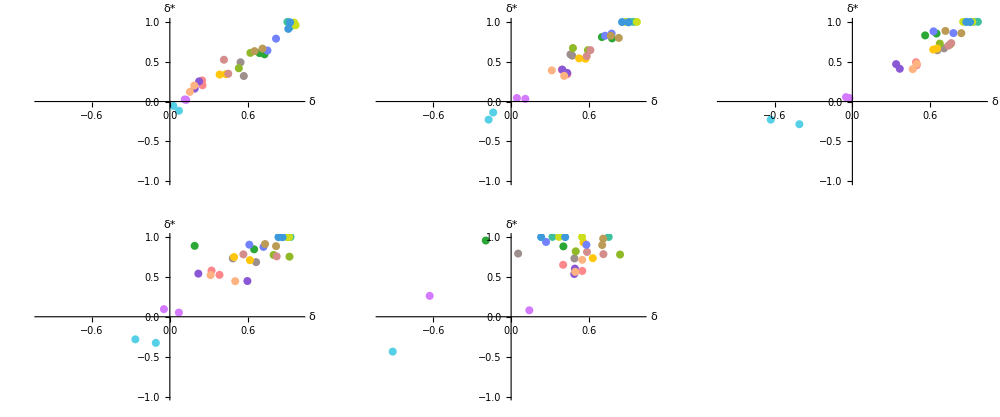

```mathematica
GraphicsGrid[{Table[Show[
Table[ListPlot[Table[{observeddelta[j,i,k],targetdelta[j,i,k]},{k,1,2}],PlotStyle->color[doublelist[[j]]]],{j,1,15}],
PlotRange->{{-1,1},{-1,1}},AxesLabel->{"δ","δ*"},ImageSize->450,AxesOrigin->{0,0}
],{i,1,3}],
Table[Show[
Table[ListPlot[Table[{observeddelta[j,i,k],targetdelta[j,i,k]},{k,1,2}],PlotStyle->color[doublelist[[j]]]],{j,1,15}],
PlotRange->{{-1,1},{-1,1}},AxesLabel->{"δ","δ*"},ImageSize->450,AxesOrigin->{0,0}
],{i,4,5}]},ImageSize->1000]
```

Legend ordered by delta

```mathematica
Sort[Table[{delta[doublelist[[i]]][[6]],Text[Style[doublelist[[i]],color[doublelist[[i]]]]]},{i,1,15}],#1[[1]]>#2[[1]]&][[All,2]]//MatrixForm
```

(CoCu
CuNi
CuZn
CoZn
NiZn
CoNi
CdCu
CdZn
CdNi
CdCo
CdMn
CoMn
MnNi
MnZn
CuMn)

## OD data as a measure of fitness

## Fitting OD data

#### Data upload

```mathematica
SetDirectory["~/Documents/Students/PennyKahn/DoubleMetalTolerance"];
```

```mathematica
datafile=Import["vgraph_growthrates_unavg_mM_19Feb25.csv"];
```

```mathematica
header=datafile[[1]]
```

{metal,conc,trial,met1_mM,met2_mM,replicate,initOD,finalOD,maxSlope}

```mathematica
datafile=Drop[datafile,1];
```

Column for the maximum growth rate estimates:

```mathematica
rcol=Flatten[Position[header,"finalOD"]][[1]]
```

8

There is an NA growth rate in one of the rows:

```mathematica
deleteme=Position[datafile[[All,rcol]],_?StringQ]//Flatten
```

{111,1}

```mathematica
datafile[[deleteme[[1]]]]
```

{CoMn,1,one,0.7,0.86,1,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

Removing this row :

```mathematica
Length[datafile]
datafile=Drop[datafile,{deleteme[[1]]}];
Length[datafile]
```

580

579

For OD, we use the final OD minus the initial OD as the measure of fitness, allowing for the fact that different metals have different initial ODs:

```mathematica
For[i=1,i≤Length[datafile],i++,
datafile[[i,rcol]]=datafile[[i,rcol]]-datafile[[i,rcol-1]]];
```

The list of double metals tested:

```mathematica
doublelist=DeleteDuplicates[Select[datafile,#[[5]]>0&][[All,1]]]
```

{CdCo,CdCu,CdMn,CdNi,CdZn,CoCu,CoMn,CoNi,CoZn,CuMn,CuNi,CuZn,MnNi,MnZn,NiZn}

```mathematica
Length[doublelist]
```

15

```mathematica
color["CdCo"]=RGBColor["#9D8F8B"];
color["CdCu"]=RGBColor["#90B927"];
color["CdMn"]=RGBColor["#FE878B"];
color["CdNi"]=RGBColor["#FFC60C"];
color["CdZn"]=RGBColor["#D48D8B"];
color["CoCu"]=RGBColor["#3DC19D"];
color["CoMn"]=RGBColor["#8A58D5"];
color["CoNi"]=RGBColor["#2BA735"];
color["CoZn"]=RGBColor["#7282FF"];
color["CuMn"]=RGBColor["#55D0E6"];
color["CuNi"]=RGBColor["#CBDF1C"];
color["CuZn"]=RGBColor["#3C99DB"];
color["MnNi"]=RGBColor["#FEB380"];
color["MnZn"]=RGBColor["#D37AFF"];
color["NiZn"]=RGBColor["#BB9B56"];
```

#### General model of metal interactions

Let us explore how metal concentrations interact for two metals.  We will use the method of Jonker et al. (2009) to estimate the synergism/antagonism of the metal interactions.  

This model assumes that increasing the concentration of one metal leads to a log-logistic-like decline in growth rate, with max as the maximal growth rate when no metal is added (x1=0):

```mathematica
Simplify[max/(1+(c[i]/EC50[i])^β[i])/.c[i]->0,β[i]>0]
```

max

and EC50[i] describes the metal concentration at which there is half-max growth:

```mathematica
Solve[max/(1+(c[i]/EC50[i])^β[i])==max/2,c[i],Assumptions->{max>0,c1>0}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c[580]→EC50[580]}}

The slope at this midpoint (measured relative to the height) is given by -β[i]/(2 EC50[i]):

```mathematica
Simplify[D[max/(1+(c[i]/EC50[i])^β[i]),c[i]]/(max/2)/.c[i]->EC50[i]]
```

-β[580]/(2 EC50[580])

The slope at 0 is 0 as long as β[i]>1 and goes to -infinity otherwise:

```mathematica
D[max/(1+(c[i]/EC50[i])^β[i]),c[i]]/(max/2)/.c[i]->0
```

-(2 0^(-1+β[580]) β[580])/((1+0^β[580])^2 EC50[580])

```mathematica
Manipulate[Plot[max/(1+(c/EC50)^β),{c,0,10},AxesLabel->{"[metal]","m"},PlotRange->{Automatic,{0,max}}],{{max,0.25},0,1},{{β,3},1,10},{{EC50,5},0,10}]
```

For two metals, we first determine f^-1(Y), where Y is the growth rate in the two metals in order to estimate the effective concentration c[i] for each metal that would have to be present (when alone) to have the same growth rate as that observed in the metal combination:

```mathematica
Solve[max/(1+((Subscript[c, eff][i])/EC50[i])^β[i])==Y,Subscript[c, eff][i]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c_eff[580]→(-1+max/Y)^(1/β[580]) EC50[580]}}

Equation 3 then divides the actual concentration for each of the two metals (c[1] and c[2]) by this effective concentration needed to give the growth seen in the metal concentration :

```mathematica
c[1]/(Subscript[c, eff][1])+c[2]/(Subscript[c, eff][2])
```

c[1]/c_eff[1]+c[2]/c_eff[2]

If the metals being combined were exactly the same, then the effective concentrations that yield the same growth rate Y as seen in the mixture should just be twice (c_eff[i] = 2 c[i] for each metal i).  In this case, the above becomes c[1]/c_eff[1]+c[2]/c_eff[2]=1/2+1/2=1. This is the “concentration addition” assumption: toxins when combined are constrained to behave in a way that is blind to whether the toxins are actually the same exact ones or behave as if they were.

Alternatively, if the metals interact, Jonker et al [OR BEFORE] allowed for a deviation from CA, that accounted for the relative toxicity of each metal being combined:

```mathematica
c[1]/(Subscript[c, eff][1])+c[2]/(Subscript[c, eff][2])==Exp[a (c[1]/EC50[1] c[2]/EC50[2])/(c[1]/EC50[1]+c[2]/EC50[2])^2]
```

c[1]/c_eff[1]+c[2]/c_eff[2]==ⅇ^((a c[1] c[2])/(EC50[1] (c[1]/EC50[1]+c[2]/EC50[2])^2 EC50[2]))

```mathematica
fitme[conc_,Y_]:=fitme[conc,Y]=Block[{},
c[1]=conc[[1]];
c[2]=conc[[2]];
c[1]/((max/Y-1)^(1/β[1]) EC50[1])+c[2]/((max/Y-1)^(1/β[2]) EC50[2])-Exp[a (c[1]/EC50[1] c[2]/EC50[2])/(c[1]/EC50[1]+c[2]/EC50[2])^2]
]
```

If a is zero (no interaction), then the above is zero (concentration addition):

```mathematica
Simplify[PowerExpand[c[1]/((max/Y-1)^(1/β[1]) EC50[1])+c[2]/((max/Y-1)^(1/β[2]) EC50[2])-1/.Y->max/(1+((2c[1])/EC50[1])^β[1])/.β[2]->β[1]/.EC50[2]->EC50[1]/.c[2]->c[1]],β[1]>0]
```

0

```mathematica
Clear[findY]
findY[{0,0},param_,a_]:=param[[1]];
findY[conc_,param_,a_]:=findY[conc,param]=Block[{c1=conc[[1]],c2=conc[[2]],
max=param[[1]],EC501=param[[2]],β1=param[[3]],EC502=param[[4]],β2=param[[5]]},
Y/.FindRoot[c1/((max/Y-1)^(1/β1) EC501)+c2/((max/Y-1)^(1/β2) EC502)-Exp[a (c1/EC501 c2/EC502)/(c1/EC501+c2/EC502)^2]==0,{Y,max/2}]
]
```

We can use maximum growth rate of 0.3 and measure the metal concentrations relative to their EC50’s (so EC50 is effectively 1). The βs and a remain free parameters in this plot:

```mathematica
Manipulate[Plot3D[findY[{c1,c2},{max,1,β1,1,β2},a],{c1,0,2},{c2,0,2},AxesLabel->{"[metal]","[metal2]","m"},PlotRange->{All,All,{0,max}}],{{max,0.3},0,1},{{β1,3},1,10},{{β2,3},1,10},{{a,0},-5,5}]
```

Using this combined growth rate to estimate δ:

```mathematica
TRYparam={0.3,1,3,1,3};
```

{0.971106,0.957979,0.938901,0.91119,0.870968,0.812652,0.728238,0.606327,0.430849}

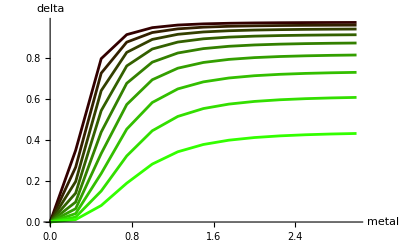

```mathematica
For[TRYc=0,TRYc≤3,TRYc=TRYc+1/4,
For[TRYa=-2,TRYa≤2,TRYa=TRYa+1/2,
delta[TRYc,TRYa]=Chop[1-2 findY[{TRYc,TRYc},TRYparam,TRYa]/(findY[{TRYc,0},TRYparam,TRYa]+findY[{0,TRYc},TRYparam,TRYa])]
]
]
Table[delta[3,a],{a,-2,2,1/2}]
Show[Table[
ListPlot[Table[{c,delta[c,a]},{c,0,3,1/4}],Joined->True,PlotStyle->RGBColor[0.2,(a+2)/4,0]],{a,-2,2,1/2}],
AxesLabel->{"metal","delta"}
]
```

Smaller βs

{0.898845,0.870486,0.834311,0.788247,0.72973,0.65561,0.562078,0.444605,0.297933}

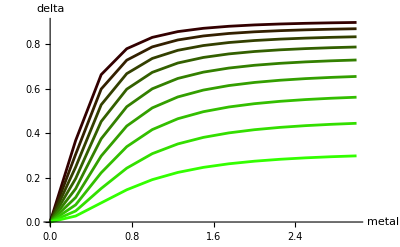

```mathematica
TRYparam={0.3,1,2,1,2};

For[TRYc=0,TRYc≤3,TRYc=TRYc+1/4,
For[TRYa=-2,TRYa≤2,TRYa=TRYa+1/2,
delta[TRYc,TRYa]=Chop[1-2 findY[{TRYc,TRYc},TRYparam,TRYa]/(findY[{TRYc,0},TRYparam,TRYa]+findY[{0,TRYc},TRYparam,TRYa])]
]
]
Table[delta[3,a],{a,-2,2,1/2}]
Show[Table[
ListPlot[Table[{c,delta[c,a]},{c,0,3,1/4}],Joined->True,PlotStyle->RGBColor[0.2,(a+2)/4,0]],{a,-2,2,1/2}],
AxesLabel->{"metal","delta"}
]
```

Larger βs

{0.991438,0.985885,0.97673,0.961642,0.936777,0.895815,0.82837,0.717414,0.535133}

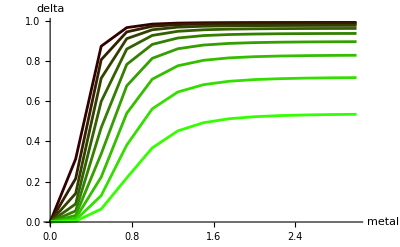

```mathematica
TRYparam={0.3,1,4,1,4};

For[TRYc=0,TRYc≤3,TRYc=TRYc+1/4,
For[TRYa=-2,TRYa≤2,TRYa=TRYa+1/2,
delta[TRYc,TRYa]=Chop[1-2 findY[{TRYc,TRYc},TRYparam,TRYa]/(findY[{TRYc,0},TRYparam,TRYa]+findY[{0,TRYc},TRYparam,TRYa])]
]
]
Table[delta[3,a],{a,-2,2,1/2}]
Show[Table[
ListPlot[Table[{c,delta[c,a]},{c,0,3,1/4}],Joined->True,PlotStyle->RGBColor[0.2,(a+2)/4,0]],{a,-2,2,1/2}],
AxesLabel->{"metal","delta"}
]
```

Different βs

Power::infy: Infinite expression 1/0. encountered.

{0.984252,0.975723,0.962787,0.943296,0.914136,0.870841,0.807088,0.714069,0.579746}

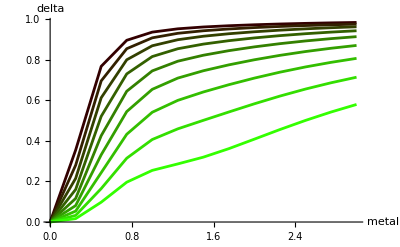

```mathematica
TRYparam={0.3,1,2,1,4};

For[TRYc=0,TRYc≤3,TRYc=TRYc+1/4,
For[TRYa=-2,TRYa≤2,TRYa=TRYa+1/2,
delta[TRYc,TRYa]=Chop[1-2 findY[{TRYc,TRYc},TRYparam,TRYa]/(findY[{TRYc,0},TRYparam,TRYa]+findY[{0,TRYc},TRYparam,TRYa])]
]
]
Table[delta[3,a],{a,-2,2,1/2}]
Show[Table[
ListPlot[Table[{c,delta[c,a]},{c,0,3,1/4}],Joined->True,PlotStyle->RGBColor[0.2,(a+2)/4,0]],{a,-2,2,1/2}],
AxesLabel->{"metal","delta"}
]
```

Measuring the metal concentrations relative to their EC50 (calling these y[i]) and the combined growth rate, Y, relative to max, there is no explicit solution for the predicted growth rate in the metal combination:

```mathematica
Solve[y[1]/(1/Y-1)^(1/β[1])+y[2]/(1/Y-1)^(1/β[2])==Exp[a (y[1]y[2])/(y[1]+y[2])^2],Y]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[(-1+1/Y)^(-1/β[1]) y[1]+(-1+1/Y)^(-1/β[2]) y[2]==ⅇ^((a y[1] y[2])/(y[1]+y[2])^2),Y]

There is if the metals have the same β:

```mathematica
Simplify[Solve[y[1]/(1/Y-1)^(1/β)+y[2]/(1/Y-1)^(1/β)==Exp[a (y[1]y[2])/(y[1]+y[2])^2],Y]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Y→1/(1+(ⅇ^(-(a y[1] y[2])/(y[1]+y[2])^2) (y[1]+y[2]))^β)}}

```mathematica
Simplify[Solve[c[1]/((max/Y-1)^(1/β) EC50[1])+c[2]/((max/Y-1)^(1/β) EC50[2])==Exp[a (c[1]/EC50[1] c[2]/EC50[2])/(c[1]/EC50[1]+c[2]/EC50[2])^2],Y]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Y→max/(1+((ⅇ^(-(a c[1] c[2] EC50[1] EC50[2])/(c[2] EC50[1]+c[1] EC50[2])^2) (c[2] EC50[1]+c[1] EC50[2]))/(EC50[1] EC50[2]))^β)}}

Thus, we can predict delta if the beta’s were similar.

```mathematica
Simplify[PowerExpand[1-2 (max/(1+((ⅇ^(-(a c[1] c[2] EC50[1] EC50[2])/(c[2] EC50[1]+c[1] EC50[2])^2) (c[2] EC50[1]+c[1] EC50[2]))/(EC50[1] EC50[2]))^β))/(max/(1+(c[1]/EC50[1])^β)+max/(1+(c[2]/EC50[2])^β))]]
```

1-2/((1+ⅇ^(-(a β c[1] c[2] EC50[1] EC50[2])/(c[2] EC50[1]+c[1] EC50[2])^2) EC50[1]^-β EC50[2]^-β (c[2] EC50[1]+c[1] EC50[2])^β) (EC50[1]^β/(c[1]^β+EC50[1]^β)+EC50[2]^β/(c[2]^β+EC50[2]^β)))

Measuring the metal concentrations relative to their EC50 and setting the metals at an equal concentration relative to EC50:

```mathematica
Simplify[PowerExpand[%/.c[1]->c*EC50[1]/.c[2]->c*EC50[2]]]
```

(c^β (2^β-ⅇ^((a β)/4)))/(2^β c^β+ⅇ^((a β)/4))

Assuming c is large (to get the asymptote), we get: 1-2^-β ⅇ^((a β)/4)

```mathematica
Show[
Plot[(c^β (2^β-ⅇ^((a β)/4)))/(2^β c^β+ⅇ^((a β)/4))/.a->0/.β->4,{c,0,5}],
Plot[1-1/(2^β  ⅇ^(-(a β)/4))/.a->0/.β->4,{c,0,5},PlotStyle->Dashed]
]
```

-Graphics-

With the proportional distance to the optimum equal to  1/(ⅇ^(-(a β)/4+ β Log[2 c])-1):

```mathematica
((1-1/(2^β  ⅇ^(-(a β)/4)))-((c^β (2^β-ⅇ^((a β)/4)))/(2^β c^β+ⅇ^((a β)/4))))/(1-1/(2^β  ⅇ^(-(a β)/4)))//Simplify
```

ⅇ^((a β)/4)/(2^β c^β+ⅇ^((a β)/4))

#### Functions for the likelihood & sum of squares

Expected growth, Y, in two metals at concentration c1 and c2 for a given value of interaction (a):

```mathematica
Clear[fitfindY]
fitfindY[max_?NumericQ,EC501_?NumericQ,β1_?NumericQ,EC502_?NumericQ,β2_?NumericQ,a_?NumericQ,0,0]:=findY[max,EC501,β1,EC502,β2,a,0,0]=max;

fitfindY[max_?NumericQ,EC501_?NumericQ,β1_?NumericQ,EC502_?NumericQ,β2_?NumericQ,a_?NumericQ,c1_?NumericQ,c2_?NumericQ]:=findY[max,EC501,β1,EC502,β2,a,c1,c2]=
Chop[Y/.FindRoot[c1/((max/Y-1)^(1/β1) EC501)+c2/((max/Y-1)^(1/β2) EC502)-Exp[a (c1/EC501 c2/EC502)/(c1/EC501+c2/EC502)^2]==0,{Y,1/10},WorkingPrecision->100]]
```

[?NumericQ was needed in the FindRoot command for Y for the FindMinimum search below to work, avoiding cases where the search returned non-numeric values.]

If a = 0, we can use:

```mathematica
fitfindY[max_?NumericQ,EC501_?NumericQ,β1_?NumericQ,EC502_?NumericQ,β2_?NumericQ,0,0]:=findY[max,EC501,β1,EC502,β2,0,0]=max;

fitfindY[max_?NumericQ,EC501_?NumericQ,β1_?NumericQ,EC502_?NumericQ,β2_?NumericQ,c1_?NumericQ,c2_?NumericQ]:=findY[max,EC501,β1,EC502,β2,c1,c2]=
Chop[Y/.FindRoot[c1/((max/Y-1)^(1/β1) EC501)+c2/((max/Y-1)^(1/β2) EC502)==1,{Y,1/10},WorkingPrecision->100]]
```

The sum of squared differences between the observed and expected growth:

```mathematica
Clear[sumofsquares]
sumofsquares[max_?NumericQ,EC501_?NumericQ,β1_?NumericQ,EC502_?NumericQ,β2_?NumericQ,a_?NumericQ,data_]:=sumofsquares[max,EC501,β1,EC502,β2,a,data]=
Chop[
Sum[(data[[i,3]]-fitfindY[max,EC501,β1,EC502,β2,a,data[[i,1]],data[[i,2]]])^2,{i,1,Length[data]}]]
```

If a = 0, we can use:

```mathematica
sumofsquares[max_?NumericQ,EC501_?NumericQ,β1_?NumericQ,EC502_?NumericQ,β2_?NumericQ,data_]:=sumofsquares[max,EC501,β1,EC502,β2,data]=
Chop[
Sum[(data[[i,3]]-fitfindY[max,EC501,β1,EC502,β2,data[[i,1]],data[[i,2]]])^2,{i,1,Length[data]}]]
```

Assuming that the deviation is normally distributed around the predicted combination fitness (Y) with a constant σ:

```mathematica
FullSimplify[Log[PDF[NormalDistribution[Y,σ],x]],{x>0,Y>0,σ>0}]
```

-(x-Y)^2/(2 σ^2)-1/2 Log[2 π]+Log[1/σ]

```mathematica
Clear[lnlikelihood]
lnlikelihood[max_?NumericQ,EC501_?NumericQ,β1_?NumericQ,EC502_?NumericQ,β2_?NumericQ,a_?NumericQ,σ_?NumericQ,data_]:=lnlikelihood[max,EC501,β1,EC502,β2,a,σ,data]=Chop[
Sum[-(data[[i,3]]-fitfindY[max,EC501,β1,EC502,β2,a,data[[i,1]],data[[i,2]]])^2/(2 σ^2)-1/2 Log[2 π]+Log[1/σ],{i,1,Length[data]}]]
```

If a = 0, we can use:

```mathematica
lnlikelihood[max_?NumericQ,EC501_?NumericQ,β1_?NumericQ,EC502_?NumericQ,β2_?NumericQ,σ_?NumericQ,data_]:=lnlikelihood[max,EC501,β1,EC502,β2,σ,data]=Chop[
Sum[-(data[[i,3]]-fitfindY[max,EC501,β1,EC502,β2,data[[i,1]],data[[i,2]]])^2/(2 σ^2)-1/2 Log[2 π]+Log[1/σ],{i,1,Length[data]}]]
```

#### CdCo growth data: a = 0.86**

```mathematica
ypad="YPAD";
single1="Cd";
single2="Co";
double="CdCo";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,0,0.8775},{0.008,0,0.937},{0.011,0,0.7673},{0.011,0,0.764},{0.017,0,0.6936},{0.017,0,0.6804},{0.026,0,0.1849},{0.026,0,0.2305},{0.038,0,0.1575},{0.038,0,0.1667},{0.005,0,0.9075},{0.005,0,0.8778},{0.01,0,0.7583},{0.01,0,0.7788},{0.016,0,0.7091},{0.016,0,0.6543},{0.022,0,0.3278},{0.022,0,0.5309},{0.027,0,0.2447},{0.027,0,0.2169}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0.7,1.3731},{0,0.7,1.3429},{0,0.86,1.2832},{0,0.86,1.3816},{0,1.,1.0802},{0,1.,1.135},{0,1.32,0.7212},{0,1.32,0.7271},{0,2.05,0.0338},{0,2.05,0.0182},{0,0.5,1.3917},{0,0.5,1.2337},{0,0.85,1.2436},{0,0.85,1.3074},{0,0.9,1.141},{0,0.9,1.1553},{0,0.95,0.6955},{0,0.95,0.6527},{0,1.3,0.0366},{0,1.3,0.0432}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,0.7,0.686},{0.008,0.7,0.7695},{0.008,0.7,0.7363},{0.011,0.86,0.6939},{0.011,0.86,0.6998},{0.011,0.86,0.7089},{0.017,1.,0.1325},{0.017,1.,0.13},{0.017,1.,0.0424},{0.026,1.32,0.0407},{0.026,1.32,0.0226},{0.026,1.32,0.0298},{0.038,2.05,0.025},{0.038,2.05,0.0317},{0.038,2.05,0.0317},{0.005,0.5,0.6779},{0.005,0.5,0.7157},{0.005,0.5,0.6855},{0.01,0.85,0.6875},{0.01,0.85,0.6385},{0.01,0.85,0.7377},{0.016,0.9,0.0933},{0.016,0.9,0.2702},{0.016,0.9,0.142},{0.022,0.95,0.0275},{0.022,0.95,0.019},{0.022,0.95,0.0185},{0.027,1.3,0.018},{0.027,1.3,0.022},{0.027,1.3,0.0188}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.011 | 0.011 | 0.017 | 0.017 | 0.026 | 0.026 | 0.038 | 0.038 | 0.005 | 0.005 | 0.01 | 0.01 | 0.016 | 0.016 | 0.022 | 0.022 | 0.027 | 0.027 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.008 | 0.011 | 0.011 | 0.011 | 0.017 | 0.017 | 0.017 | 0.026 | 0.026 | 0.026 | 0.038 | 0.038 | 0.038 | 0.005 | 0.005 | 0.005 | 0.01 | 0.01 | 0.01 | 0.016 | 0.016 | 0.016 | 0.022 | 0.022 | 0.022 | 0.027 | 0.027 | 0.027
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.86 | 0.86 | 1. | 1. | 1.32 | 1.32 | 2.05 | 2.05 | 0.5 | 0.5 | 0.85 | 0.85 | 0.9 | 0.9 | 0.95 | 0.95 | 1.3 | 1.3 | 0.7 | 0.7 | 0.7 | 0.86 | 0.86 | 0.86 | 1. | 1. | 1. | 1.32 | 1.32 | 1.32 | 2.05 | 2.05 | 2.05 | 0.5 | 0.5 | 0.5 | 0.85 | 0.85 | 0.85 | 0.9 | 0.9 | 0.9 | 0.95 | 0.95 | 0.95 | 1.3 | 1.3 | 1.3
1.4598 | 1.4544 | 1.4005 | 1.4594 | 1.4188 | 1.5012 | 1.4445 | 1.5353 | 1.5101 | 1.5665 | 0.8775 | 0.937 | 0.7673 | 0.764 | 0.6936 | 0.6804 | 0.1849 | 0.2305 | 0.1575 | 0.1667 | 0.9075 | 0.8778 | 0.7583 | 0.7788 | 0.7091 | 0.6543 | 0.3278 | 0.5309 | 0.2447 | 0.2169 | 1.3731 | 1.3429 | 1.2832 | 1.3816 | 1.0802 | 1.135 | 0.7212 | 0.7271 | 0.0338 | 0.0182 | 1.3917 | 1.2337 | 1.2436 | 1.3074 | 1.141 | 1.1553 | 0.6955 | 0.6527 | 0.0366 | 0.0432 | 0.686 | 0.7695 | 0.7363 | 0.6939 | 0.6998 | 0.7089 | 0.1325 | 0.13 | 0.0424 | 0.0407 | 0.0226 | 0.0298 | 0.025 | 0.0317 | 0.0317 | 0.6779 | 0.7157 | 0.6855 | 0.6875 | 0.6385 | 0.7377 | 0.0933 | 0.2702 | 0.142 | 0.0275 | 0.019 | 0.0185 | 0.018 | 0.022 | 0.0188)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{0.008,0.8775},{0.008,0.937},{0.011,0.7673},{0.011,0.764},{0.017,0.6936},{0.017,0.6804},{0.026,0.1849},{0.026,0.2305},{0.038,0.1575},{0.038,0.1667},{0.005,0.9075},{0.005,0.8778},{0.01,0.7583},{0.01,0.7788},{0.016,0.7091},{0.016,0.6543},{0.022,0.3278},{0.022,0.5309},{0.027,0.2447},{0.027,0.2169}}

{max→1.36555,EC501→1.67173,β1→2.67598×10^-8}

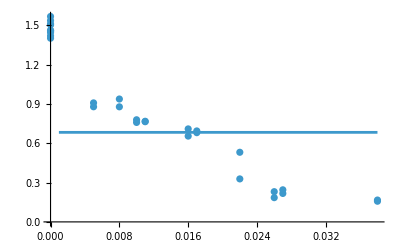

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{0.7,1.3731},{0.7,1.3429},{0.86,1.2832},{0.86,1.3816},{1.,1.0802},{1.,1.135},{1.32,0.7212},{1.32,0.7271},{2.05,0.0338},{2.05,0.0182},{0.5,1.3917},{0.5,1.2337},{0.85,1.2436},{0.85,1.3074},{0.9,1.141},{0.9,1.1553},{0.95,0.6955},{0.95,0.6527},{1.3,0.0366},{1.3,0.0432}}

{max→1.45727,EC502→1.10005,β2→6.0364}

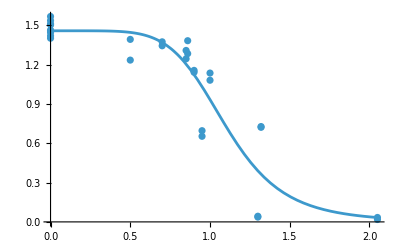

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{1.41141,1.67173,2.67598×10^-8,1.10005,6.0364}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

11.1079

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{2.2757,{max→1.44422,EC501→0.0117561,β1→1.16352,EC502→1.12466,β2→5.75976}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{28.8744,{max→1.44422,EC501→0.0117561,β1→1.16352,EC502→1.12466,β2→5.75977,σ→0.16866}}

Here the fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.0000440263,0.000253834,0.000416637,0.0000451605,-0.000179885}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{2.09013,{max→1.4358,EC501→0.0108564,β1→1.34019,EC502→1.10439,β2→6.44429,a→0.85803}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

FindMaximum::nrnum: The function value 98888.6-251.327 ⅈ is not a real number at {max,EC501,β1,EC502,β2,a,σ} = {1.97945,0.0200027,3.69826,0.778566,5.71103,-2.61154,-0.010799}.

FindMaximum::nrnum: The function value 98887.1-251.327 ⅈ is not a real number at {max,EC501,β1,EC502,β2,a,σ} = {1.97944,0.0200027,3.69826,0.778566,5.71103,-2.61154,-0.010799}.

FindMaximum::nrnum: The function value 98858.8-251.327 ⅈ is not a real number at {max,EC501,β1,EC502,β2,a,σ} = {1.97921,0.0200027,3.69826,0.778566,5.71103,-2.61154,-0.010799}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

{32.277,{max→1.4358,EC501→0.0108564,β1→1.34019,EC502→1.10439,β2→6.44431,a→0.858031,σ→0.161637}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-0.0000339912,0.000221914,0.000353924,0.0000435297,-0.00032739,-0.000192084}

Testing whether adding the parameter “a” significantly improves the fit:

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841. This is NOT SIGNIFICANT:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

0.00908988

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.0598568,0.198288,0.364331,0.48794,0.536469,0.561973,0.621623,0.704259,0.782248,0.844102}

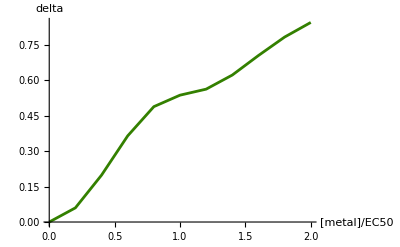

```mathematica
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

0.858031

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

0.0108564

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

1.10439

#### CdCu growth data: a = 1.75***

```mathematica
ypad="YPAD";
single1="Cd";
single2="Cu";
double="CdCu";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,0,0.8775},{0.008,0,0.937},{0.011,0,0.7673},{0.011,0,0.764},{0.017,0,0.6936},{0.017,0,0.6804},{0.026,0,0.1849},{0.026,0,0.2305},{0.038,0,0.1575},{0.038,0,0.1667},{0.005,0,0.9075},{0.005,0,0.8778},{0.01,0,0.7583},{0.01,0,0.7788},{0.016,0,0.7091},{0.016,0,0.6543},{0.022,0,0.3278},{0.022,0,0.5309},{0.027,0,0.2447},{0.027,0,0.2169}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,8.83,1.2866},{0,8.83,1.4425},{0,10.17,1.0509},{0,10.17,0.9717},{0,10.83,0.8337},{0,10.83,0.8388},{0,12.,0.7934},{0,12.,0.911},{0,13.5,0.0144},{0,13.5,0.0575},{0,4.,1.1996},{0,4.,1.3127},{0,8.83,0.9746},{0,8.83,0.9672},{0,10.17,0.7667},{0,10.17,0.7767},{0,10.85,0.8112},{0,10.85,0.7962},{0,12.9,0.0137},{0,12.9,0.0134}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,8.83,0.8523},{0.008,8.83,0.9391},{0.008,8.83,0.8267},{0.011,10.17,0.8666},{0.011,10.17,0.8713},{0.011,10.17,0.8327},{0.017,10.83,0.0195},{0.017,10.83,0.2828},{0.017,10.83,0.0118},{0.026,12.,0.0068},{0.026,12.,0.0091},{0.026,12.,0.012},{0.038,13.5,0.0193},{0.038,13.5,0.0402},{0.038,13.5,0.0175},{0.005,4.,0.8613},{0.005,4.,0.8165},{0.005,4.,0.8365},{0.01,8.83,0.7942},{0.01,8.83,0.9015},{0.01,8.83,0.7205},{0.016,10.17,0.0803},{0.016,10.17,0.0151},{0.016,10.17,0.0916},{0.022,10.85,-0.3814},{0.022,10.85,0.006},{0.022,10.85,0.0125},{0.027,12.9,0.0117},{0.027,12.9,0.0193},{0.027,12.9,0.0195}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.011 | 0.011 | 0.017 | 0.017 | 0.026 | 0.026 | 0.038 | 0.038 | 0.005 | 0.005 | 0.01 | 0.01 | 0.016 | 0.016 | 0.022 | 0.022 | 0.027 | 0.027 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.008 | 0.011 | 0.011 | 0.011 | 0.017 | 0.017 | 0.017 | 0.026 | 0.026 | 0.026 | 0.038 | 0.038 | 0.038 | 0.005 | 0.005 | 0.005 | 0.01 | 0.01 | 0.01 | 0.016 | 0.016 | 0.016 | 0.022 | 0.022 | 0.022 | 0.027 | 0.027 | 0.027
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.83 | 8.83 | 10.17 | 10.17 | 10.83 | 10.83 | 12. | 12. | 13.5 | 13.5 | 4. | 4. | 8.83 | 8.83 | 10.17 | 10.17 | 10.85 | 10.85 | 12.9 | 12.9 | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.83 | 10.83 | 10.83 | 12. | 12. | 12. | 13.5 | 13.5 | 13.5 | 4. | 4. | 4. | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.85 | 10.85 | 10.85 | 12.9 | 12.9 | 12.9
1.4598 | 1.4544 | 1.4005 | 1.4594 | 1.4188 | 1.5012 | 1.4445 | 1.5353 | 1.5101 | 1.5665 | 0.8775 | 0.937 | 0.7673 | 0.764 | 0.6936 | 0.6804 | 0.1849 | 0.2305 | 0.1575 | 0.1667 | 0.9075 | 0.8778 | 0.7583 | 0.7788 | 0.7091 | 0.6543 | 0.3278 | 0.5309 | 0.2447 | 0.2169 | 1.2866 | 1.4425 | 1.0509 | 0.9717 | 0.8337 | 0.8388 | 0.7934 | 0.911 | 0.0144 | 0.0575 | 1.1996 | 1.3127 | 0.9746 | 0.9672 | 0.7667 | 0.7767 | 0.8112 | 0.7962 | 0.0137 | 0.0134 | 0.8523 | 0.9391 | 0.8267 | 0.8666 | 0.8713 | 0.8327 | 0.0195 | 0.2828 | 0.0118 | 0.0068 | 0.0091 | 0.012 | 0.0193 | 0.0402 | 0.0175 | 0.8613 | 0.8165 | 0.8365 | 0.7942 | 0.9015 | 0.7205 | 0.0803 | 0.0151 | 0.0916 | -0.3814 | 0.006 | 0.0125 | 0.0117 | 0.0193 | 0.0195)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{0.008,0.8775},{0.008,0.937},{0.011,0.7673},{0.011,0.764},{0.017,0.6936},{0.017,0.6804},{0.026,0.1849},{0.026,0.2305},{0.038,0.1575},{0.038,0.1667},{0.005,0.9075},{0.005,0.8778},{0.01,0.7583},{0.01,0.7788},{0.016,0.7091},{0.016,0.6543},{0.022,0.3278},{0.022,0.5309},{0.027,0.2447},{0.027,0.2169}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→1.36555,EC501→1.67173,β1→2.67598×10^-8}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{8.83,1.2866},{8.83,1.4425},{10.17,1.0509},{10.17,0.9717},{10.83,0.8337},{10.83,0.8388},{12.,0.7934},{12.,0.911},{13.5,0.0144},{13.5,0.0575},{4.,1.1996},{4.,1.3127},{8.83,0.9746},{8.83,0.9672},{10.17,0.7667},{10.17,0.7767},{10.85,0.8112},{10.85,0.7962},{12.9,0.0137},{12.9,0.0134}}

{max→1.42242,EC502→11.0364,β2→8.48113}

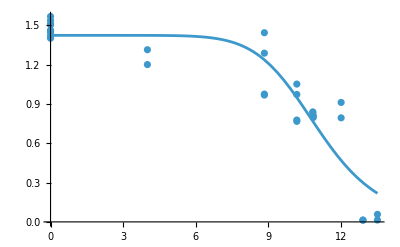

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{1.39399,1.67173,2.67598×10^-8,11.0364,8.48113}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

12.5997

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{3.9734,{max→1.40861,EC501→0.013366,β1→0.961751,EC502→11.2208,β2→8.24318}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{6.58108,{max→1.40861,EC501→0.013366,β1→0.961743,EC502→11.2208,β2→8.24333,σ→0.222862}}

Here the fits aren’t compatible as there is a ridge that is hard to search:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{0.000100911,-0.000142656,0.00080627,-0.000030166,-0.00184979}

Seeing if we get a better sumofsquares fit if starting at the lnlikelihood fit:

```mathematica
FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,max/.maxll[[2]]},{EC501,EC501/.maxll[[2]]},{β1,β1/.maxll[[2]]},{EC502,EC502/.maxll[[2]]},{β2,β2/.maxll[[2]]}}]
```

{3.9734,{max→1.40861,EC501→0.013366,β1→0.961742,EC502→11.2208,β2→8.24335}}

This is a better sum of squares and is closer to the ML fit:

```mathematica
100(({max,EC501,β1,EC502,β2}/.%[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.0000105406,0.0000136448,-0.0000835927,3.14162×10^-6,0.000196408}

Seeing if we get a better lnlikelihood fit if starting at the sumofsquares fit:

```mathematica
FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,max/.ssq[[2]]},{EC501,EC501/.ssq[[2]]},{β1,β1/.ssq[[2]]},{EC502,EC502/.ssq[[2]]},{β2,β2/.ssq[[2]]},{σ,0.01,0,1}}]
```

{6.58108,{max→1.40861,EC501→0.013366,β1→0.961751,EC502→11.2208,β2→8.24317,σ→0.222862}}

This is a lower likelihood (worse fit).

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{2.97154,{max→1.36478,EC501→0.0117905,β1→1.75482,EC502→11.2014,β2→9.99114,a→1.74716}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

FindMaximum::nrnum: The function value 607063.-251.327 ⅈ is not a real number at {max,EC501,β1,EC502,β2,a,σ} = {1.39344,0.0339918,1.0879,10.0191,5.87926,9.89419,-0.00559287}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

{18.2029,{max→1.36466,EC501→0.0117924,β1→1.75512,EC502→11.2016,β2→9.99855,a→1.74723,σ→0.192728}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{0.0081584,-0.0160486,-0.0170181,-0.00246727,-0.0741114,-0.00391348}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841, which it is:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

1.42729×10^-6

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction, the fit is much better:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.00975364,0.0731569,0.211258,0.36649,0.388714,0.342231,0.454676,0.61862,0.750554,0.841774}

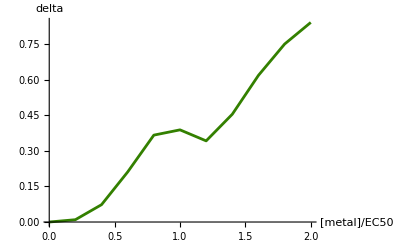

```mathematica
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

1.74723

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

0.0117924

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

11.2016

#### CdMn growth data: a = 0.81**

```mathematica
ypad="YPAD";
single1="Cd";
single2="Mn";
double="CdMn";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,0,0.8775},{0.008,0,0.937},{0.011,0,0.7673},{0.011,0,0.764},{0.017,0,0.6936},{0.017,0,0.6804},{0.026,0,0.1849},{0.026,0,0.2305},{0.038,0,0.1575},{0.038,0,0.1667},{0.005,0,0.9075},{0.005,0,0.8778},{0.01,0,0.7583},{0.01,0,0.7788},{0.016,0,0.7091},{0.016,0,0.6543},{0.022,0,0.3278},{0.022,0,0.5309},{0.027,0,0.2447},{0.027,0,0.2169}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0.86,1.4523},{0,0.86,1.3266},{0,1.14,0.9145},{0,1.14,1.0459},{0,1.31,1.067},{0,1.31,1.1458},{0,1.66,0.7365},{0,1.66,0.726},{0,2.23,0.4567},{0,2.23,0.4334},{0,0.85,1.3842},{0,0.85,1.3551},{0,1.,1.0278},{0,1.,1.0112},{0,1.14,0.957},{0,1.14,0.9658},{0,1.25,0.775},{0,1.25,0.7677},{0,1.6,0.479},{0,1.6,0.5157}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,0.86,0.7352},{0.008,0.86,0.7444},{0.008,0.86,0.6605},{0.011,1.14,0.6225},{0.011,1.14,0.6045},{0.011,1.14,0.6221},{0.017,1.31,0.5969},{0.017,1.31,0.4714},{0.017,1.31,0.5275},{0.026,1.66,0.206},{0.026,1.66,0.0661},{0.026,1.66,0.0899},{0.038,2.23,0.0201},{0.038,2.23,0.0253},{0.038,2.23,0.038},{0.005,0.85,0.6759},{0.005,0.85,0.6623},{0.005,0.85,0.7215},{0.01,1.,0.5493},{0.01,1.,0.5593},{0.01,1.,0.5377},{0.016,1.14,0.4486},{0.016,1.14,0.5207},{0.016,1.14,0.4626},{0.022,1.25,0.1377},{0.022,1.25,0.373},{0.022,1.25,0.4653},{0.027,1.6,0.0283},{0.027,1.6,0.0351},{0.027,1.6,0.032}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.011 | 0.011 | 0.017 | 0.017 | 0.026 | 0.026 | 0.038 | 0.038 | 0.005 | 0.005 | 0.01 | 0.01 | 0.016 | 0.016 | 0.022 | 0.022 | 0.027 | 0.027 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.008 | 0.011 | 0.011 | 0.011 | 0.017 | 0.017 | 0.017 | 0.026 | 0.026 | 0.026 | 0.038 | 0.038 | 0.038 | 0.005 | 0.005 | 0.005 | 0.01 | 0.01 | 0.01 | 0.016 | 0.016 | 0.016 | 0.022 | 0.022 | 0.022 | 0.027 | 0.027 | 0.027
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86 | 0.86 | 1.14 | 1.14 | 1.31 | 1.31 | 1.66 | 1.66 | 2.23 | 2.23 | 0.85 | 0.85 | 1. | 1. | 1.14 | 1.14 | 1.25 | 1.25 | 1.6 | 1.6 | 0.86 | 0.86 | 0.86 | 1.14 | 1.14 | 1.14 | 1.31 | 1.31 | 1.31 | 1.66 | 1.66 | 1.66 | 2.23 | 2.23 | 2.23 | 0.85 | 0.85 | 0.85 | 1. | 1. | 1. | 1.14 | 1.14 | 1.14 | 1.25 | 1.25 | 1.25 | 1.6 | 1.6 | 1.6
1.4598 | 1.4544 | 1.4005 | 1.4594 | 1.4188 | 1.5012 | 1.4445 | 1.5353 | 1.5101 | 1.5665 | 0.8775 | 0.937 | 0.7673 | 0.764 | 0.6936 | 0.6804 | 0.1849 | 0.2305 | 0.1575 | 0.1667 | 0.9075 | 0.8778 | 0.7583 | 0.7788 | 0.7091 | 0.6543 | 0.3278 | 0.5309 | 0.2447 | 0.2169 | 1.4523 | 1.3266 | 0.9145 | 1.0459 | 1.067 | 1.1458 | 0.7365 | 0.726 | 0.4567 | 0.4334 | 1.3842 | 1.3551 | 1.0278 | 1.0112 | 0.957 | 0.9658 | 0.775 | 0.7677 | 0.479 | 0.5157 | 0.7352 | 0.7444 | 0.6605 | 0.6225 | 0.6045 | 0.6221 | 0.5969 | 0.4714 | 0.5275 | 0.206 | 0.0661 | 0.0899 | 0.0201 | 0.0253 | 0.038 | 0.6759 | 0.6623 | 0.7215 | 0.5493 | 0.5593 | 0.5377 | 0.4486 | 0.5207 | 0.4626 | 0.1377 | 0.373 | 0.4653 | 0.0283 | 0.0351 | 0.032)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{0.008,0.8775},{0.008,0.937},{0.011,0.7673},{0.011,0.764},{0.017,0.6936},{0.017,0.6804},{0.026,0.1849},{0.026,0.2305},{0.038,0.1575},{0.038,0.1667},{0.005,0.9075},{0.005,0.8778},{0.01,0.7583},{0.01,0.7788},{0.016,0.7091},{0.016,0.6543},{0.022,0.3278},{0.022,0.5309},{0.027,0.2447},{0.027,0.2169}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→1.36555,EC501→1.67173,β1→2.67598×10^-8}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{0.86,1.4523},{0.86,1.3266},{1.14,0.9145},{1.14,1.0459},{1.31,1.067},{1.31,1.1458},{1.66,0.7365},{1.66,0.726},{2.23,0.4567},{2.23,0.4334},{0.85,1.3842},{0.85,1.3551},{1.,1.0278},{1.,1.0112},{1.14,0.957},{1.14,0.9658},{1.25,0.775},{1.25,0.7677},{1.6,0.479},{1.6,0.5157}}

{max→1.48792,EC502→1.50209,β2→2.8948}

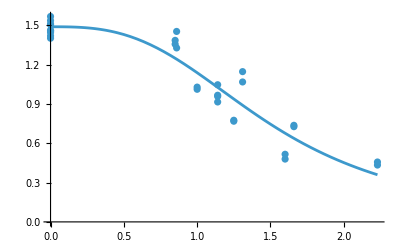

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{1.42673,1.67173,2.67598×10^-8,1.50209,2.8948}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

9.56747

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{1.27627,{max→1.47818,EC501→0.0113174,β1→1.15031,EC502→1.56812,β2→2.60032}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{52.0084,{max→1.47818,EC501→0.0113174,β1→1.1503,EC502→1.56812,β2→2.60031,σ→0.126307}}

The fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.0000645934,0.000393339,0.000332061,-0.0000485995,0.000391826}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{1.15954,{max→1.47468,EC501→0.0105949,β1→1.23218,EC502→1.50887,β2→2.93348,a→0.80586}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

FindMaximum::nrnum: The function value 21669.6-251.327 ⅈ is not a real number at {max,EC501,β1,EC502,β2,a,σ} = {1.68202,0.00671449,2.88037,1.12362,4.81395,-9.85629,-0.0164763}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

{55.8452,{max→1.47468,EC501→0.0105949,β1→1.23218,EC502→1.50887,β2→2.93347,a→0.805857,σ→0.120392}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-0.0000739442,0.000367241,0.000409354,-0.0000219037,0.00035538,0.000316336}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841, which it is:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

0.00560337

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction, the fit is much better:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.083577,0.206876,0.30831,0.375421,0.418259,0.449425,0.476903,0.504103,0.531775,0.559571}

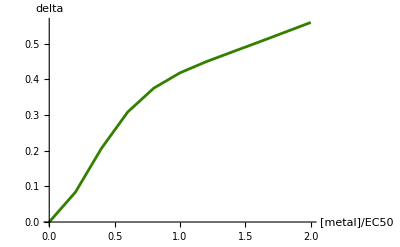

```mathematica
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

0.805857

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

0.0105949

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

1.50887

#### CdNi growth data: a = 2.02***

```mathematica
ypad="YPAD";
single1="Cd";
single2="Ni";
double="CdNi";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,0,0.8775},{0.008,0,0.937},{0.011,0,0.7673},{0.011,0,0.764},{0.017,0,0.6936},{0.017,0,0.6804},{0.026,0,0.1849},{0.026,0,0.2305},{0.038,0,0.1575},{0.038,0,0.1667},{0.005,0,0.9075},{0.005,0,0.8778},{0.01,0,0.7583},{0.01,0,0.7788},{0.016,0,0.7091},{0.016,0,0.6543},{0.022,0,0.3278},{0.022,0,0.5309},{0.027,0,0.2447},{0.027,0,0.2169}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,1.88,1.477},{0,1.88,1.4318},{0,2.4,1.469},{0,2.4,1.371},{0,3.,0.8652},{0,3.,0.9787},{0,3.6,0.5413},{0,3.6,0.5766},{0,5.1,0.0206},{0,5.1,0.005},{0,2.3,1.4688},{0,2.3,1.4886},{0,2.6,1.4167},{0,2.6,1.3268},{0,2.75,0.871},{0,2.75,0.926},{0,3.,0.5344},{0,3.,0.5202},{0,3.2,0.032},{0,3.2,0.0312}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,1.88,1.0252},{0.008,1.88,1.0998},{0.008,1.88,1.0048},{0.011,2.4,0.8012},{0.011,2.4,0.8423},{0.011,2.4,0.812},{0.017,3.,0.3053},{0.017,3.,0.3488},{0.017,3.,0.505},{0.026,3.6,0.0432},{0.026,3.6,0.0242},{0.026,3.6,0.0205},{0.038,5.1,0.0222},{0.038,5.1,0.0152},{0.038,5.1,0.019},{0.005,2.3,0.9596},{0.005,2.3,1.0343},{0.005,2.3,1.046},{0.01,2.6,0.6921},{0.01,2.6,0.6759},{0.01,2.6,0.6214},{0.016,2.75,0.4653},{0.016,2.75,0.228},{0.016,2.75,0.2945},{0.022,3.,0.0195},{0.022,3.,0.0305},{0.022,3.,0.0212},{0.027,3.2,0.0095},{0.027,3.2,0.0095},{0.027,3.2,0.0085}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.011 | 0.011 | 0.017 | 0.017 | 0.026 | 0.026 | 0.038 | 0.038 | 0.005 | 0.005 | 0.01 | 0.01 | 0.016 | 0.016 | 0.022 | 0.022 | 0.027 | 0.027 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.008 | 0.011 | 0.011 | 0.011 | 0.017 | 0.017 | 0.017 | 0.026 | 0.026 | 0.026 | 0.038 | 0.038 | 0.038 | 0.005 | 0.005 | 0.005 | 0.01 | 0.01 | 0.01 | 0.016 | 0.016 | 0.016 | 0.022 | 0.022 | 0.022 | 0.027 | 0.027 | 0.027
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.88 | 1.88 | 2.4 | 2.4 | 3. | 3. | 3.6 | 3.6 | 5.1 | 5.1 | 2.3 | 2.3 | 2.6 | 2.6 | 2.75 | 2.75 | 3. | 3. | 3.2 | 3.2 | 1.88 | 1.88 | 1.88 | 2.4 | 2.4 | 2.4 | 3. | 3. | 3. | 3.6 | 3.6 | 3.6 | 5.1 | 5.1 | 5.1 | 2.3 | 2.3 | 2.3 | 2.6 | 2.6 | 2.6 | 2.75 | 2.75 | 2.75 | 3. | 3. | 3. | 3.2 | 3.2 | 3.2
1.4598 | 1.4544 | 1.4005 | 1.4594 | 1.4188 | 1.5012 | 1.4445 | 1.5353 | 1.5101 | 1.5665 | 0.8775 | 0.937 | 0.7673 | 0.764 | 0.6936 | 0.6804 | 0.1849 | 0.2305 | 0.1575 | 0.1667 | 0.9075 | 0.8778 | 0.7583 | 0.7788 | 0.7091 | 0.6543 | 0.3278 | 0.5309 | 0.2447 | 0.2169 | 1.477 | 1.4318 | 1.469 | 1.371 | 0.8652 | 0.9787 | 0.5413 | 0.5766 | 0.0206 | 0.005 | 1.4688 | 1.4886 | 1.4167 | 1.3268 | 0.871 | 0.926 | 0.5344 | 0.5202 | 0.032 | 0.0312 | 1.0252 | 1.0998 | 1.0048 | 0.8012 | 0.8423 | 0.812 | 0.3053 | 0.3488 | 0.505 | 0.0432 | 0.0242 | 0.0205 | 0.0222 | 0.0152 | 0.019 | 0.9596 | 1.0343 | 1.046 | 0.6921 | 0.6759 | 0.6214 | 0.4653 | 0.228 | 0.2945 | 0.0195 | 0.0305 | 0.0212 | 0.0095 | 0.0095 | 0.0085)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{0.008,0.8775},{0.008,0.937},{0.011,0.7673},{0.011,0.764},{0.017,0.6936},{0.017,0.6804},{0.026,0.1849},{0.026,0.2305},{0.038,0.1575},{0.038,0.1667},{0.005,0.9075},{0.005,0.8778},{0.01,0.7583},{0.01,0.7788},{0.016,0.7091},{0.016,0.6543},{0.022,0.3278},{0.022,0.5309},{0.027,0.2447},{0.027,0.2169}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→1.36555,EC501→1.67173,β1→2.67598×10^-8}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{1.88,1.477},{1.88,1.4318},{2.4,1.469},{2.4,1.371},{3.,0.8652},{3.,0.9787},{3.6,0.5413},{3.6,0.5766},{5.1,0.0206},{5.1,0.005},{2.3,1.4688},{2.3,1.4886},{2.6,1.4167},{2.6,1.3268},{2.75,0.871},{2.75,0.926},{3.,0.5344},{3.,0.5202},{3.2,0.032},{3.2,0.0312}}

{max→1.49104,EC502→2.93571,β2→12.8529}

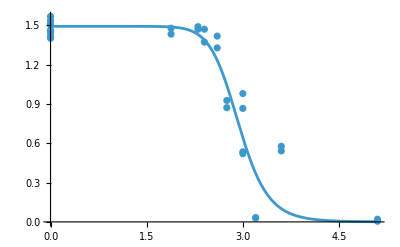

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{1.4283,1.67173,2.67598×10^-8,2.93571,12.8529}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

9.77815

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

FindMinimum::nrnum: The function value -131.603-89.0302 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.56593,0.00556975,0.473728,2.95579,8.34651}.

FindMinimum::nrnum: The function value -131.602-89.0289 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.56592,0.00556975,0.473728,2.95579,8.34651}.

FindMinimum::nrnum: The function value -131.571-89.0047 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.56573,0.00556975,0.473728,2.95579,8.34651}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

{3.67552,{max→1.49713,EC501→0.0140354,β1→0.716452,EC502→2.98568,β2→9.99818}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{9.69854,{max→1.49713,EC501→0.0140355,β1→0.7164,EC502→2.98566,β2→9.99964,σ→0.214345}}

The fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{0.000378422,-0.000882332,0.00726922,0.000479688,-0.014615}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{1.79102,{max→1.49454,EC501→0.0111599,β1→1.69825,EC502→2.9475,β2→9.99971,a→2.02011}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{38.4549,{max→1.49454,EC501→0.0111599,β1→1.69825,EC502→2.9475,β2→9.99999,a→2.02011,σ→0.149625}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{0.0000457486,0.0000812654,0.000368571,0.0000573144,-0.0027172,-0.000238711}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841, which it is:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

3.35287×10^-14

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction, the fit is much better:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.0059429,0.0556629,0.169633,0.298194,0.279713,0.175571,0.276587,0.466999,0.634388,0.757917}

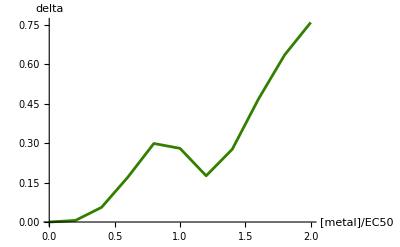

```mathematica
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

2.02011

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

0.0111599

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

2.9475

#### CdZn growth data: a = 1.26***

```mathematica
ypad="YPAD";
single1="Cd";
single2="Zn";
double="CdZn";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,0,0.8775},{0.008,0,0.937},{0.011,0,0.7673},{0.011,0,0.764},{0.017,0,0.6936},{0.017,0,0.6804},{0.026,0,0.1849},{0.026,0,0.2305},{0.038,0,0.1575},{0.038,0,0.1667},{0.005,0,0.9075},{0.005,0,0.8778},{0.01,0,0.7583},{0.01,0,0.7788},{0.016,0,0.7091},{0.016,0,0.6543},{0.022,0,0.3278},{0.022,0,0.5309},{0.027,0,0.2447},{0.027,0,0.2169}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,4.,1.336},{0,4.,1.3572},{0,4.75,1.2102},{0,4.75,1.2322},{0,5.4,0.9341},{0,5.4,1.0006},{0,6.,0.6473},{0,6.,0.6677},{0,6.6,0.171},{0,6.6,0.1993},{0,3.33,1.2977},{0,3.33,1.3343},{0,4.,1.2007},{0,4.,1.2182},{0,4.8,0.9505},{0,4.8,0.9968},{0,5.4,0.685},{0,5.4,0.7097},{0,6.,0.3027},{0,6.,0.283}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.008,4.,1.0712},{0.008,4.,0.983},{0.008,4.,1.0423},{0.011,4.75,0.3966},{0.011,4.75,0.6201},{0.011,4.75,0.4773},{0.017,5.4,0.0655},{0.017,5.4,0.1042},{0.017,5.4,0.117},{0.026,6.,0.0311},{0.026,6.,0.0513},{0.026,6.,0.038},{0.038,6.6,0.0073},{0.038,6.6,0.0058},{0.038,6.6,0.0074},{0.005,3.33,0.9614},{0.005,3.33,0.9291},{0.005,3.33,1.0109},{0.01,4.,0.449},{0.01,4.,0.5582},{0.01,4.,0.3918},{0.016,4.8,0.0991},{0.016,4.8,0.0873},{0.016,4.8,0.0898},{0.022,5.4,0.0149},{0.022,5.4,0.0137},{0.022,5.4,0.0143},{0.027,6.,0.0077},{0.027,6.,0.0107},{0.027,6.,-0.024}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.011 | 0.011 | 0.017 | 0.017 | 0.026 | 0.026 | 0.038 | 0.038 | 0.005 | 0.005 | 0.01 | 0.01 | 0.016 | 0.016 | 0.022 | 0.022 | 0.027 | 0.027 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.008 | 0.008 | 0.008 | 0.011 | 0.011 | 0.011 | 0.017 | 0.017 | 0.017 | 0.026 | 0.026 | 0.026 | 0.038 | 0.038 | 0.038 | 0.005 | 0.005 | 0.005 | 0.01 | 0.01 | 0.01 | 0.016 | 0.016 | 0.016 | 0.022 | 0.022 | 0.022 | 0.027 | 0.027 | 0.027
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4. | 4. | 4.75 | 4.75 | 5.4 | 5.4 | 6. | 6. | 6.6 | 6.6 | 3.33 | 3.33 | 4. | 4. | 4.8 | 4.8 | 5.4 | 5.4 | 6. | 6. | 4. | 4. | 4. | 4.75 | 4.75 | 4.75 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6. | 6.6 | 6.6 | 6.6 | 3.33 | 3.33 | 3.33 | 4. | 4. | 4. | 4.8 | 4.8 | 4.8 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6.
1.4598 | 1.4544 | 1.4005 | 1.4594 | 1.4188 | 1.5012 | 1.4445 | 1.5353 | 1.5101 | 1.5665 | 0.8775 | 0.937 | 0.7673 | 0.764 | 0.6936 | 0.6804 | 0.1849 | 0.2305 | 0.1575 | 0.1667 | 0.9075 | 0.8778 | 0.7583 | 0.7788 | 0.7091 | 0.6543 | 0.3278 | 0.5309 | 0.2447 | 0.2169 | 1.336 | 1.3572 | 1.2102 | 1.2322 | 0.9341 | 1.0006 | 0.6473 | 0.6677 | 0.171 | 0.1993 | 1.2977 | 1.3343 | 1.2007 | 1.2182 | 0.9505 | 0.9968 | 0.685 | 0.7097 | 0.3027 | 0.283 | 1.0712 | 0.983 | 1.0423 | 0.3966 | 0.6201 | 0.4773 | 0.0655 | 0.1042 | 0.117 | 0.0311 | 0.0513 | 0.038 | 0.0073 | 0.0058 | 0.0074 | 0.9614 | 0.9291 | 1.0109 | 0.449 | 0.5582 | 0.3918 | 0.0991 | 0.0873 | 0.0898 | 0.0149 | 0.0137 | 0.0143 | 0.0077 | 0.0107 | -0.024)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{0.008,0.8775},{0.008,0.937},{0.011,0.7673},{0.011,0.764},{0.017,0.6936},{0.017,0.6804},{0.026,0.1849},{0.026,0.2305},{0.038,0.1575},{0.038,0.1667},{0.005,0.9075},{0.005,0.8778},{0.01,0.7583},{0.01,0.7788},{0.016,0.7091},{0.016,0.6543},{0.022,0.3278},{0.022,0.5309},{0.027,0.2447},{0.027,0.2169}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→1.36555,EC501→1.67173,β1→2.67598×10^-8}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{4.,1.336},{4.,1.3572},{4.75,1.2102},{4.75,1.2322},{5.4,0.9341},{5.4,1.0006},{6.,0.6473},{6.,0.6677},{6.6,0.171},{6.6,0.1993},{3.33,1.2977},{3.33,1.3343},{4.,1.2007},{4.,1.2182},{4.8,0.9505},{4.8,0.9968},{5.4,0.685},{5.4,0.7097},{6.,0.3027},{6.,0.283}}

{max→1.44066,EC502→5.51042,β2→8.06572}

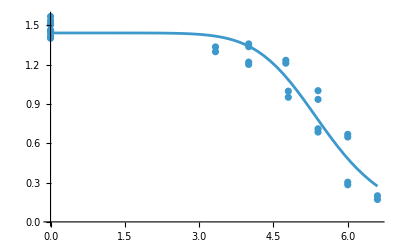

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{1.4031,1.67173,2.67598×10^-8,5.51042,8.06572}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

12.3553

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{2.16347,{max→1.41506,EC501→0.014233,β1→1.28737,EC502→5.62435,β2→8.30136}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{30.8974,{max→1.41506,EC501→0.014233,β1→1.28737,EC502→5.62436,β2→8.30146,σ→0.164449}}

Here the fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{0.0000784363,-0.000146283,0.000301729,-0.0000203006,-0.00119673}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

FindMinimum::nrnum: The function value 353.85-120.593 ⅈ is not a real number at {max,EC501,β1,EC502,β2,a} = {1.393,0.0376238,0.0497318,5.47679,8.04572,-0.19548}.

FindMinimum::nrnum: The function value 353.845-120.592 ⅈ is not a real number at {max,EC501,β1,EC502,β2,a} = {1.39299,0.0376238,0.0497318,5.47679,8.04572,-0.19548}.

FindMinimum::nrnum: The function value 353.759-120.563 ⅈ is not a real number at {max,EC501,β1,EC502,β2,a} = {1.39283,0.0376238,0.0497318,5.47679,8.04572,-0.19548}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

{1.41705,{max→1.40003,EC501→0.012232,β1→1.86236,EC502→5.56415,β2→9.74242,a→1.25873}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

FindMaximum::nrnum: The function value 358.845-251.327 ⅈ is not a real number at {max,EC501,β1,EC502,β2,a,σ} = {1.63784,0.0207221,0.14674,5.20234,7.9807,-9.90149,-0.109271}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

{47.8229,{max→1.40003,EC501→0.0122321,β1→1.86236,EC502→5.56416,β2→9.74299,a→1.25873,σ→0.133091}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{0.000477052,-0.000724475,-0.00021924,-0.000166811,-0.00585582,-0.000181419}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841. This is NOT SIGNIFICANT:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

5.94999×10^-9

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.0172121,0.111857,0.301075,0.498101,0.574332,0.595021,0.693444,0.800912,0.877639,0.926198}

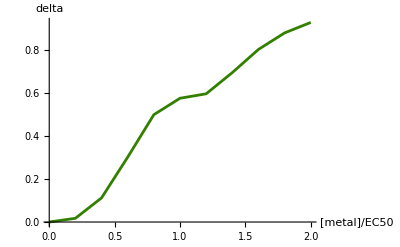

```mathematica
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

1.25873

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

0.0122321

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

5.56416

#### CoCu growth data: a = –2.8***

```mathematica
ypad="YPAD";
single1="Co";
single2="Cu";
double="CoCu";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.7,0,1.3731},{0.7,0,1.3429},{0.86,0,1.2832},{0.86,0,1.3816},{1.,0,1.0802},{1.,0,1.135},{1.32,0,0.7212},{1.32,0,0.7271},{2.05,0,0.0338},{2.05,0,0.0182},{0.5,0,1.3917},{0.5,0,1.2337},{0.85,0,1.2436},{0.85,0,1.3074},{0.9,0,1.141},{0.9,0,1.1553},{0.95,0,0.6955},{0.95,0,0.6527},{1.3,0,0.0366},{1.3,0,0.0432}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,8.83,1.2866},{0,8.83,1.4425},{0,10.17,1.0509},{0,10.17,0.9717},{0,10.83,0.8337},{0,10.83,0.8388},{0,12.,0.7934},{0,12.,0.911},{0,13.5,0.0144},{0,13.5,0.0575},{0,4.,1.1996},{0,4.,1.3127},{0,8.83,0.9746},{0,8.83,0.9672},{0,10.17,0.7667},{0,10.17,0.7767},{0,10.85,0.8112},{0,10.85,0.7962},{0,12.9,0.0137},{0,12.9,0.0134}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.7,8.83,0.0298},{0.7,8.83,0.0305},{0.7,8.83,0.049},{0.86,10.17,0.0113},{0.86,10.17,0.007},{0.86,10.17,0.0112},{1.,10.83,0.0087},{1.,10.83,0.0178},{1.,10.83,0.009},{1.32,12.,0.0089},{1.32,12.,0.018},{1.32,12.,0.0131},{2.05,13.5,0.0239},{2.05,13.5,0.0282},{2.05,13.5,0.038},{0.5,4.,0.032},{0.5,4.,0.0493},{0.5,4.,0.045},{0.85,8.83,0.0104},{0.85,8.83,0.0107},{0.85,8.83,0.0138},{0.9,10.17,-0.0022},{0.9,10.17,0.006},{0.9,10.17,0.0053},{0.95,10.85,0.01},{0.95,10.85,-0.005},{0.95,10.85,0.0114},{1.3,12.9,0.0239},{1.3,12.9,0.0222},{1.3,12.9,0.0196}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.86 | 0.86 | 1. | 1. | 1.32 | 1.32 | 2.05 | 2.05 | 0.5 | 0.5 | 0.85 | 0.85 | 0.9 | 0.9 | 0.95 | 0.95 | 1.3 | 1.3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.7 | 0.86 | 0.86 | 0.86 | 1. | 1. | 1. | 1.32 | 1.32 | 1.32 | 2.05 | 2.05 | 2.05 | 0.5 | 0.5 | 0.5 | 0.85 | 0.85 | 0.85 | 0.9 | 0.9 | 0.9 | 0.95 | 0.95 | 0.95 | 1.3 | 1.3 | 1.3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.83 | 8.83 | 10.17 | 10.17 | 10.83 | 10.83 | 12. | 12. | 13.5 | 13.5 | 4. | 4. | 8.83 | 8.83 | 10.17 | 10.17 | 10.85 | 10.85 | 12.9 | 12.9 | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.83 | 10.83 | 10.83 | 12. | 12. | 12. | 13.5 | 13.5 | 13.5 | 4. | 4. | 4. | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.85 | 10.85 | 10.85 | 12.9 | 12.9 | 12.9
1.4598 | 1.4544 | 1.4005 | 1.4594 | 1.4188 | 1.5012 | 1.4445 | 1.5353 | 1.5101 | 1.5665 | 1.3731 | 1.3429 | 1.2832 | 1.3816 | 1.0802 | 1.135 | 0.7212 | 0.7271 | 0.0338 | 0.0182 | 1.3917 | 1.2337 | 1.2436 | 1.3074 | 1.141 | 1.1553 | 0.6955 | 0.6527 | 0.0366 | 0.0432 | 1.2866 | 1.4425 | 1.0509 | 0.9717 | 0.8337 | 0.8388 | 0.7934 | 0.911 | 0.0144 | 0.0575 | 1.1996 | 1.3127 | 0.9746 | 0.9672 | 0.7667 | 0.7767 | 0.8112 | 0.7962 | 0.0137 | 0.0134 | 0.0298 | 0.0305 | 0.049 | 0.0113 | 0.007 | 0.0112 | 0.0087 | 0.0178 | 0.009 | 0.0089 | 0.018 | 0.0131 | 0.0239 | 0.0282 | 0.038 | 0.032 | 0.0493 | 0.045 | 0.0104 | 0.0107 | 0.0138 | -0.0022 | 0.006 | 0.0053 | 0.01 | -0.005 | 0.0114 | 0.0239 | 0.0222 | 0.0196)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{0.7,1.3731},{0.7,1.3429},{0.86,1.2832},{0.86,1.3816},{1.,1.0802},{1.,1.135},{1.32,0.7212},{1.32,0.7271},{2.05,0.0338},{2.05,0.0182},{0.5,1.3917},{0.5,1.2337},{0.85,1.2436},{0.85,1.3074},{0.9,1.141},{0.9,1.1553},{0.95,0.6955},{0.95,0.6527},{1.3,0.0366},{1.3,0.0432}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→1.45727,EC501→1.10005,β1→6.0364}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{8.83,1.2866},{8.83,1.4425},{10.17,1.0509},{10.17,0.9717},{10.83,0.8337},{10.83,0.8388},{12.,0.7934},{12.,0.911},{13.5,0.0144},{13.5,0.0575},{4.,1.1996},{4.,1.3127},{8.83,0.9746},{8.83,0.9672},{10.17,0.7667},{10.17,0.7767},{10.85,0.8112},{10.85,0.7962},{12.9,0.0137},{12.9,0.0134}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→1.42242,EC502→11.0364,β2→8.48113}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{1.43985,1.10005,6.0364,11.0364,8.48113}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

5.58512

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{5.1028,{max→1.41841,EC501→1.04366,β1→4.73968,EC502→10.7471,β2→7.04196}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{-3.42557,{max→1.41841,EC501→1.04366,β1→4.73968,EC502→10.7471,β2→7.04196,σ→0.252557}}

Here the fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-3.02605×10^-6,1.49996×10^-6,-0.0000513911,7.24881×10^-6,0.000109927}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{1.84962,{max→1.41653,EC501→1.11344,β1→6.34209,EC502→11.0509,β2→8.54387,a→-2.79654}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{37.1668,{max→1.41653,EC501→1.11344,β1→6.34208,EC502→11.0509,β2→8.54386,a→-2.79655,σ→0.152053}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-7.45213×10^-6,2.5309×10^-6,0.0000233636,3.36244×10^-6,0.000107964,-0.0000179657}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841. This is NOT SIGNIFICANT:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

0.

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.17118,0.970164,0.998429,0.999785,0.999932,0.999958,0.999966,0.99997,0.999973,0.999976}

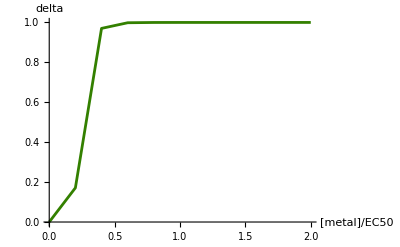

```mathematica
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

-2.79655

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

1.11344

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

11.0509

#### CoMn growth data: a = 2.1***

```mathematica
ypad="YPAD";
single1="Co";
single2="Mn";
double="CoMn";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.7,0,1.3731},{0.7,0,1.3429},{0.86,0,1.2832},{0.86,0,1.3816},{1.,0,1.0802},{1.,0,1.135},{1.32,0,0.7212},{1.32,0,0.7271},{2.05,0,0.0338},{2.05,0,0.0182},{0.5,0,1.3917},{0.5,0,1.2337},{0.85,0,1.2436},{0.85,0,1.3074},{0.9,0,1.141},{0.9,0,1.1553},{0.95,0,0.6955},{0.95,0,0.6527},{1.3,0,0.0366},{1.3,0,0.0432}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0.86,1.4523},{0,0.86,1.3266},{0,1.14,0.9145},{0,1.14,1.0459},{0,1.31,1.067},{0,1.31,1.1458},{0,1.66,0.7365},{0,1.66,0.726},{0,2.23,0.4567},{0,2.23,0.4334},{0,0.85,1.3842},{0,0.85,1.3551},{0,1.,1.0278},{0,1.,1.0112},{0,1.14,0.957},{0,1.14,0.9658},{0,1.25,0.775},{0,1.25,0.7677},{0,1.6,0.479},{0,1.6,0.5157}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.7,0.86,1.3131},{0.7,0.86,1.3355},{0.86,1.14,1.1371},{0.86,1.14,1.1796},{0.86,1.14,1.1613},{1.,1.31,0.7227},{1.,1.31,0.7425},{1.,1.31,0.7906},{1.32,1.66,0.5313},{1.32,1.66,0.5059},{1.32,1.66,0.4905},{2.05,2.23,0.0199},{2.05,2.23,0.026},{2.05,2.23,0.0354},{0.5,0.85,1.3145},{0.5,0.85,1.2295},{0.5,0.85,1.2888},{0.85,1.,0.9707},{0.85,1.,1.0605},{0.85,1.,1.0687},{0.9,1.14,0.6709},{0.9,1.14,0.663},{0.9,1.14,0.7335},{0.95,1.25,0.1155},{0.95,1.25,0.1833},{0.95,1.25,0.1815},{1.3,1.6,0.031},{1.3,1.6,0.0267},{1.3,1.6,0.0329}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.86 | 0.86 | 1. | 1. | 1.32 | 1.32 | 2.05 | 2.05 | 0.5 | 0.5 | 0.85 | 0.85 | 0.9 | 0.9 | 0.95 | 0.95 | 1.3 | 1.3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.86 | 0.86 | 0.86 | 1. | 1. | 1. | 1.32 | 1.32 | 1.32 | 2.05 | 2.05 | 2.05 | 0.5 | 0.5 | 0.5 | 0.85 | 0.85 | 0.85 | 0.9 | 0.9 | 0.9 | 0.95 | 0.95 | 0.95 | 1.3 | 1.3 | 1.3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86 | 0.86 | 1.14 | 1.14 | 1.31 | 1.31 | 1.66 | 1.66 | 2.23 | 2.23 | 0.85 | 0.85 | 1. | 1. | 1.14 | 1.14 | 1.25 | 1.25 | 1.6 | 1.6 | 0.86 | 0.86 | 1.14 | 1.14 | 1.14 | 1.31 | 1.31 | 1.31 | 1.66 | 1.66 | 1.66 | 2.23 | 2.23 | 2.23 | 0.85 | 0.85 | 0.85 | 1. | 1. | 1. | 1.14 | 1.14 | 1.14 | 1.25 | 1.25 | 1.25 | 1.6 | 1.6 | 1.6
1.4598 | 1.4544 | 1.4005 | 1.4594 | 1.4188 | 1.5012 | 1.4445 | 1.5353 | 1.5101 | 1.5665 | 1.3731 | 1.3429 | 1.2832 | 1.3816 | 1.0802 | 1.135 | 0.7212 | 0.7271 | 0.0338 | 0.0182 | 1.3917 | 1.2337 | 1.2436 | 1.3074 | 1.141 | 1.1553 | 0.6955 | 0.6527 | 0.0366 | 0.0432 | 1.4523 | 1.3266 | 0.9145 | 1.0459 | 1.067 | 1.1458 | 0.7365 | 0.726 | 0.4567 | 0.4334 | 1.3842 | 1.3551 | 1.0278 | 1.0112 | 0.957 | 0.9658 | 0.775 | 0.7677 | 0.479 | 0.5157 | 1.3131 | 1.3355 | 1.1371 | 1.1796 | 1.1613 | 0.7227 | 0.7425 | 0.7906 | 0.5313 | 0.5059 | 0.4905 | 0.0199 | 0.026 | 0.0354 | 1.3145 | 1.2295 | 1.2888 | 0.9707 | 1.0605 | 1.0687 | 0.6709 | 0.663 | 0.7335 | 0.1155 | 0.1833 | 0.1815 | 0.031 | 0.0267 | 0.0329)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{0.7,1.3731},{0.7,1.3429},{0.86,1.2832},{0.86,1.3816},{1.,1.0802},{1.,1.135},{1.32,0.7212},{1.32,0.7271},{2.05,0.0338},{2.05,0.0182},{0.5,1.3917},{0.5,1.2337},{0.85,1.2436},{0.85,1.3074},{0.9,1.141},{0.9,1.1553},{0.95,0.6955},{0.95,0.6527},{1.3,0.0366},{1.3,0.0432}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→1.45727,EC501→1.10005,β1→6.0364}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{0.86,1.4523},{0.86,1.3266},{1.14,0.9145},{1.14,1.0459},{1.31,1.067},{1.31,1.1458},{1.66,0.7365},{1.66,0.726},{2.23,0.4567},{2.23,0.4334},{0.85,1.3842},{0.85,1.3551},{1.,1.0278},{1.,1.0112},{1.14,0.957},{1.14,0.9658},{1.25,0.775},{1.25,0.7677},{1.6,0.479},{1.6,0.5157}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→1.48792,EC502→1.50209,β2→2.8948}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{1.47259,1.10005,6.0364,1.50209,2.8948}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

10.7709

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{5.69938,{max→1.55301,EC501→1.15503,β1→4.34792,EC502→2.23,β2→0.950603}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{-8.24706,{max→1.55301,EC501→1.15503,β1→4.34791,EC502→2.23,β2→0.950604,σ→0.268596}}

Here the fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{7.62778×10^-7,-0.0000178731,0.0000745175,0.0000761829,-0.000130593}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{3.07937,{max→1.46849,EC501→1.08967,β1→6.43739,EC502→1.48979,β2→3.4085,a→2.00502}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{16.0704,{max→1.46849,EC501→1.08967,β1→6.43738,EC502→1.48979,β2→3.4085,a→2.00502,σ→0.197432}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-6.88714×10^-6,-6.38347×10^-6,0.000160239,0.000012454,-0.0000214977,3.23445×10^-6}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841, which it is:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

3.08342×10^-12

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.01,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.01,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction, the fit is much better:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.01,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.01,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.000514773,0.020059,0.115859,0.281966,0.406649,0.471802,0.523648,0.576575,0.627368,0.672908}

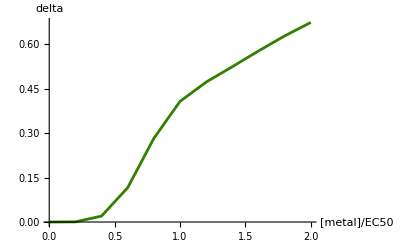

```mathematica
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

Except for very low metal concentrations, the deltas are near one (maximum synergistic toxicity)

```mathematica
a[double]=a/.maxlla[[2]]
```

2.00502

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

1.08967

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

1.48979

#### CoNi growth data: a = 0.59***

```mathematica
ypad="YPAD";
single1="Co";
single2="Ni";
double="CoNi";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.7,0,1.3731},{0.7,0,1.3429},{0.86,0,1.2832},{0.86,0,1.3816},{1.,0,1.0802},{1.,0,1.135},{1.32,0,0.7212},{1.32,0,0.7271},{2.05,0,0.0338},{2.05,0,0.0182},{0.5,0,1.3917},{0.5,0,1.2337},{0.85,0,1.2436},{0.85,0,1.3074},{0.9,0,1.141},{0.9,0,1.1553},{0.95,0,0.6955},{0.95,0,0.6527},{1.3,0,0.0366},{1.3,0,0.0432}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,1.88,1.477},{0,1.88,1.4318},{0,2.4,1.469},{0,2.4,1.371},{0,3.,0.8652},{0,3.,0.9787},{0,3.6,0.5413},{0,3.6,0.5766},{0,5.1,0.0206},{0,5.1,0.005},{0,2.3,1.4688},{0,2.3,1.4886},{0,2.6,1.4167},{0,2.6,1.3268},{0,2.75,0.871},{0,2.75,0.926},{0,3.,0.5344},{0,3.,0.5202},{0,3.2,0.032},{0,3.2,0.0312}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.7,1.88,0.515},{0.7,1.88,0.5828},{0.7,1.88,0.5743},{0.86,2.4,0.0408},{0.86,2.4,0.0343},{0.86,2.4,0.0296},{1.,3.,0.0315},{1.,3.,0.0362},{1.,3.,0.035},{1.32,3.6,0.0537},{1.32,3.6,0.0447},{1.32,3.6,0.0512},{2.05,5.1,0.0117},{2.05,5.1,0.0144},{2.05,5.1,0.0162},{0.5,2.3,0.4393},{0.5,2.3,0.489},{0.5,2.3,0.5384},{0.85,2.6,0.0378},{0.85,2.6,0.0398},{0.85,2.6,0.0624},{0.9,2.75,0.0385},{0.9,2.75,0.0422},{0.9,2.75,0.0333},{0.95,3.,0.0182},{0.95,3.,0.0211},{0.95,3.,0.0208},{1.3,3.2,0.0139},{1.3,3.2,0.0122},{1.3,3.2,0.0055}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.86 | 0.86 | 1. | 1. | 1.32 | 1.32 | 2.05 | 2.05 | 0.5 | 0.5 | 0.85 | 0.85 | 0.9 | 0.9 | 0.95 | 0.95 | 1.3 | 1.3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.7 | 0.86 | 0.86 | 0.86 | 1. | 1. | 1. | 1.32 | 1.32 | 1.32 | 2.05 | 2.05 | 2.05 | 0.5 | 0.5 | 0.5 | 0.85 | 0.85 | 0.85 | 0.9 | 0.9 | 0.9 | 0.95 | 0.95 | 0.95 | 1.3 | 1.3 | 1.3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.88 | 1.88 | 2.4 | 2.4 | 3. | 3. | 3.6 | 3.6 | 5.1 | 5.1 | 2.3 | 2.3 | 2.6 | 2.6 | 2.75 | 2.75 | 3. | 3. | 3.2 | 3.2 | 1.88 | 1.88 | 1.88 | 2.4 | 2.4 | 2.4 | 3. | 3. | 3. | 3.6 | 3.6 | 3.6 | 5.1 | 5.1 | 5.1 | 2.3 | 2.3 | 2.3 | 2.6 | 2.6 | 2.6 | 2.75 | 2.75 | 2.75 | 3. | 3. | 3. | 3.2 | 3.2 | 3.2
1.4598 | 1.4544 | 1.4005 | 1.4594 | 1.4188 | 1.5012 | 1.4445 | 1.5353 | 1.5101 | 1.5665 | 1.3731 | 1.3429 | 1.2832 | 1.3816 | 1.0802 | 1.135 | 0.7212 | 0.7271 | 0.0338 | 0.0182 | 1.3917 | 1.2337 | 1.2436 | 1.3074 | 1.141 | 1.1553 | 0.6955 | 0.6527 | 0.0366 | 0.0432 | 1.477 | 1.4318 | 1.469 | 1.371 | 0.8652 | 0.9787 | 0.5413 | 0.5766 | 0.0206 | 0.005 | 1.4688 | 1.4886 | 1.4167 | 1.3268 | 0.871 | 0.926 | 0.5344 | 0.5202 | 0.032 | 0.0312 | 0.515 | 0.5828 | 0.5743 | 0.0408 | 0.0343 | 0.0296 | 0.0315 | 0.0362 | 0.035 | 0.0537 | 0.0447 | 0.0512 | 0.0117 | 0.0144 | 0.0162 | 0.4393 | 0.489 | 0.5384 | 0.0378 | 0.0398 | 0.0624 | 0.0385 | 0.0422 | 0.0333 | 0.0182 | 0.0211 | 0.0208 | 0.0139 | 0.0122 | 0.0055)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{0.7,1.3731},{0.7,1.3429},{0.86,1.2832},{0.86,1.3816},{1.,1.0802},{1.,1.135},{1.32,0.7212},{1.32,0.7271},{2.05,0.0338},{2.05,0.0182},{0.5,1.3917},{0.5,1.2337},{0.85,1.2436},{0.85,1.3074},{0.9,1.141},{0.9,1.1553},{0.95,0.6955},{0.95,0.6527},{1.3,0.0366},{1.3,0.0432}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→1.45727,EC501→1.10005,β1→6.0364}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{1.88,1.477},{1.88,1.4318},{2.4,1.469},{2.4,1.371},{3.,0.8652},{3.,0.9787},{3.6,0.5413},{3.6,0.5766},{5.1,0.0206},{5.1,0.005},{2.3,1.4688},{2.3,1.4886},{2.6,1.4167},{2.6,1.3268},{2.75,0.871},{2.75,0.926},{3.,0.5344},{3.,0.5202},{3.2,0.032},{3.2,0.0312}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→1.49104,EC502→2.93571,β2→12.8529}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{1.47415,1.10005,6.0364,2.93571,12.8529}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

2.67463

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{2.37497,{max→1.49633,EC501→1.14007,β1→4.32174,EC502→2.97775,β2→9.70425}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{27.1667,{max→1.49633,EC501→1.14007,β1→4.32185,EC502→2.97776,β2→9.70339,σ→0.172299}}

Here the fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.000233,0.000540343,-0.00250993,-0.000215339,0.00880061}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{2.01944,{max→1.48897,EC501→1.08928,β1→5.96912,EC502→2.95005,β2→10.,a→0.589951}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{33.6532,{max→1.48897,EC501→1.08928,β1→5.96912,EC502→2.95005,β2→9.99999,a→0.58995,σ→0.15888}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-2.70806×10^-6,1.17159×10^-6,6.92263×10^-6,-1.7979×10^-6,0.0000926821,0.0000457308}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841, which it is:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

0.000315996

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.000417783,0.0586951,0.553361,0.905037,0.969037,0.980657,0.98518,0.988233,0.990527,0.992288}

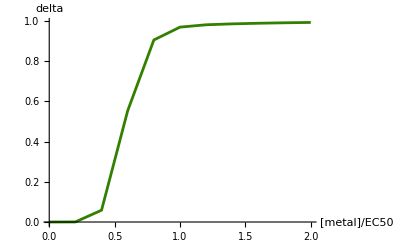

```mathematica
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

0.58995

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

1.08928

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

2.95005

#### CoZn growth data: a = –1.3***

```mathematica
ypad="YPAD";
single1="Co";
single2="Zn";
double="CoZn";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.7,0,1.3731},{0.7,0,1.3429},{0.86,0,1.2832},{0.86,0,1.3816},{1.,0,1.0802},{1.,0,1.135},{1.32,0,0.7212},{1.32,0,0.7271},{2.05,0,0.0338},{2.05,0,0.0182},{0.5,0,1.3917},{0.5,0,1.2337},{0.85,0,1.2436},{0.85,0,1.3074},{0.9,0,1.141},{0.9,0,1.1553},{0.95,0,0.6955},{0.95,0,0.6527},{1.3,0,0.0366},{1.3,0,0.0432}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,4.,1.336},{0,4.,1.3572},{0,4.75,1.2102},{0,4.75,1.2322},{0,5.4,0.9341},{0,5.4,1.0006},{0,6.,0.6473},{0,6.,0.6677},{0,6.6,0.171},{0,6.6,0.1993},{0,3.33,1.2977},{0,3.33,1.3343},{0,4.,1.2007},{0,4.,1.2182},{0,4.8,0.9505},{0,4.8,0.9968},{0,5.4,0.685},{0,5.4,0.7097},{0,6.,0.3027},{0,6.,0.283}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.7,4.,0.0388},{0.7,4.,0.0816},{0.7,4.,0.049},{0.86,4.75,0.0741},{0.86,4.75,0.0557},{0.86,4.75,0.0258},{1.,5.4,0.055},{1.,5.4,0.0717},{1.,5.4,0.0531},{1.32,6.,0.0324},{1.32,6.,0.0422},{1.32,6.,0.0492},{2.05,6.6,0.0409},{2.05,6.6,0.0202},{2.05,6.6,0.0265},{0.5,3.33,0.0848},{0.5,3.33,0.0495},{0.5,3.33,0.074},{0.85,4.,0.0558},{0.85,4.,0.085},{0.85,4.,0.0739},{0.9,4.8,0.0443},{0.9,4.8,0.058},{0.9,4.8,0.0455},{0.95,5.4,0.051},{0.95,5.4,0.0467},{0.95,5.4,0.0545},{1.3,6.,0.0461},{1.3,6.,0.0354},{1.3,6.,0.032}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.86 | 0.86 | 1. | 1. | 1.32 | 1.32 | 2.05 | 2.05 | 0.5 | 0.5 | 0.85 | 0.85 | 0.9 | 0.9 | 0.95 | 0.95 | 1.3 | 1.3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.7 | 0.7 | 0.86 | 0.86 | 0.86 | 1. | 1. | 1. | 1.32 | 1.32 | 1.32 | 2.05 | 2.05 | 2.05 | 0.5 | 0.5 | 0.5 | 0.85 | 0.85 | 0.85 | 0.9 | 0.9 | 0.9 | 0.95 | 0.95 | 0.95 | 1.3 | 1.3 | 1.3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4. | 4. | 4.75 | 4.75 | 5.4 | 5.4 | 6. | 6. | 6.6 | 6.6 | 3.33 | 3.33 | 4. | 4. | 4.8 | 4.8 | 5.4 | 5.4 | 6. | 6. | 4. | 4. | 4. | 4.75 | 4.75 | 4.75 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6. | 6.6 | 6.6 | 6.6 | 3.33 | 3.33 | 3.33 | 4. | 4. | 4. | 4.8 | 4.8 | 4.8 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6.
1.4598 | 1.4544 | 1.4005 | 1.4594 | 1.4188 | 1.5012 | 1.4445 | 1.5353 | 1.5101 | 1.5665 | 1.3731 | 1.3429 | 1.2832 | 1.3816 | 1.0802 | 1.135 | 0.7212 | 0.7271 | 0.0338 | 0.0182 | 1.3917 | 1.2337 | 1.2436 | 1.3074 | 1.141 | 1.1553 | 0.6955 | 0.6527 | 0.0366 | 0.0432 | 1.336 | 1.3572 | 1.2102 | 1.2322 | 0.9341 | 1.0006 | 0.6473 | 0.6677 | 0.171 | 0.1993 | 1.2977 | 1.3343 | 1.2007 | 1.2182 | 0.9505 | 0.9968 | 0.685 | 0.7097 | 0.3027 | 0.283 | 0.0388 | 0.0816 | 0.049 | 0.0741 | 0.0557 | 0.0258 | 0.055 | 0.0717 | 0.0531 | 0.0324 | 0.0422 | 0.0492 | 0.0409 | 0.0202 | 0.0265 | 0.0848 | 0.0495 | 0.074 | 0.0558 | 0.085 | 0.0739 | 0.0443 | 0.058 | 0.0455 | 0.051 | 0.0467 | 0.0545 | 0.0461 | 0.0354 | 0.032)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{0.7,1.3731},{0.7,1.3429},{0.86,1.2832},{0.86,1.3816},{1.,1.0802},{1.,1.135},{1.32,0.7212},{1.32,0.7271},{2.05,0.0338},{2.05,0.0182},{0.5,1.3917},{0.5,1.2337},{0.85,1.2436},{0.85,1.3074},{0.9,1.141},{0.9,1.1553},{0.95,0.6955},{0.95,0.6527},{1.3,0.0366},{1.3,0.0432}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→1.45727,EC501→1.10005,β1→6.0364}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{4.,1.336},{4.,1.3572},{4.75,1.2102},{4.75,1.2322},{5.4,0.9341},{5.4,1.0006},{6.,0.6473},{6.,0.6677},{6.6,0.171},{6.6,0.1993},{3.33,1.2977},{3.33,1.3343},{4.,1.2007},{4.,1.2182},{4.8,0.9505},{4.8,0.9968},{5.4,0.685},{5.4,0.7097},{6.,0.3027},{6.,0.283}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→1.44066,EC502→5.51042,β2→8.06572}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{1.44896,1.10005,6.0364,5.51042,8.06572}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

2.14308

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{1.97254,{max→1.43044,EC501→1.05804,β1→7.5849,EC502→5.4245,β2→9.2373}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{34.593,{max→1.43045,EC501→1.05804,β1→7.58485,EC502→5.4245,β2→9.23713,σ→0.157025}}

Here the fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.000131967,0.0000142109,0.000554963,0.0000788952,0.00181361}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{1.36976,{max→1.43245,EC501→1.10866,β1→6.18113,EC502→5.52087,β2→8.1423,a→-1.31926}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{49.1807,{max→1.43245,EC501→1.10866,β1→6.18113,EC502→5.52087,β2→8.14229,a→-1.31926,σ→0.130851}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-4.22304×10^-6,1.39201×10^-6,0.0000137031,2.01637×10^-6,0.0000561399,-0.0000278145}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841. This is not significant:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

6.61153×10^-8

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.0162934,0.678614,0.973069,0.995831,0.998593,0.999115,0.99927,0.999347,0.999401,0.999446}

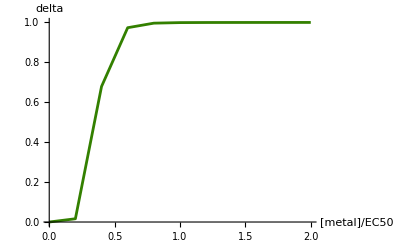

```mathematica
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

-1.31926

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

1.10866

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

5.52087

#### CuMn growth data: a = 2.9*** [SLOW FOR a=0]

```mathematica
ypad="YPAD";
single1="Cu";
single2="Mn";
double="CuMn";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{8.83,0,1.2866},{8.83,0,1.4425},{10.17,0,1.0509},{10.17,0,0.9717},{10.83,0,0.8337},{10.83,0,0.8388},{12.,0,0.7934},{12.,0,0.911},{13.5,0,0.0144},{13.5,0,0.0575},{4.,0,1.1996},{4.,0,1.3127},{8.83,0,0.9746},{8.83,0,0.9672},{10.17,0,0.7667},{10.17,0,0.7767},{10.85,0,0.8112},{10.85,0,0.7962},{12.9,0,0.0137},{12.9,0,0.0134}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0.86,1.4523},{0,0.86,1.3266},{0,1.14,0.9145},{0,1.14,1.0459},{0,1.31,1.067},{0,1.31,1.1458},{0,1.66,0.7365},{0,1.66,0.726},{0,2.23,0.4567},{0,2.23,0.4334},{0,0.85,1.3842},{0,0.85,1.3551},{0,1.,1.0278},{0,1.,1.0112},{0,1.14,0.957},{0,1.14,0.9658},{0,1.25,0.775},{0,1.25,0.7677},{0,1.6,0.479},{0,1.6,0.5157}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{8.83,0.86,1.4595},{8.83,0.86,1.452},{8.83,0.86,1.3971},{10.17,1.14,1.2488},{10.17,1.14,1.2201},{10.17,1.14,1.257},{10.83,1.31,1.1637},{10.83,1.31,1.0878},{10.83,1.31,1.1422},{12.,1.66,0.7398},{12.,1.66,0.7345},{12.,1.66,0.7475},{13.5,2.23,0.2163},{13.5,2.23,0.3192},{13.5,2.23,0.255},{4.,0.85,1.5017},{4.,0.85,1.4504},{4.,0.85,1.3659},{8.83,1.,1.1947},{8.83,1.,1.3105},{8.83,1.,1.2554},{10.17,1.14,1.0343},{10.17,1.14,1.1282},{10.17,1.14,1.1528},{10.85,1.25,0.7785},{10.85,1.25,0.7942},{10.85,1.25,0.7235},{12.9,1.6,0.157},{12.9,1.6,0.1228},{12.9,1.6,0.2333}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.83 | 8.83 | 10.17 | 10.17 | 10.83 | 10.83 | 12. | 12. | 13.5 | 13.5 | 4. | 4. | 8.83 | 8.83 | 10.17 | 10.17 | 10.85 | 10.85 | 12.9 | 12.9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.83 | 10.83 | 10.83 | 12. | 12. | 12. | 13.5 | 13.5 | 13.5 | 4. | 4. | 4. | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.85 | 10.85 | 10.85 | 12.9 | 12.9 | 12.9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86 | 0.86 | 1.14 | 1.14 | 1.31 | 1.31 | 1.66 | 1.66 | 2.23 | 2.23 | 0.85 | 0.85 | 1. | 1. | 1.14 | 1.14 | 1.25 | 1.25 | 1.6 | 1.6 | 0.86 | 0.86 | 0.86 | 1.14 | 1.14 | 1.14 | 1.31 | 1.31 | 1.31 | 1.66 | 1.66 | 1.66 | 2.23 | 2.23 | 2.23 | 0.85 | 0.85 | 0.85 | 1. | 1. | 1. | 1.14 | 1.14 | 1.14 | 1.25 | 1.25 | 1.25 | 1.6 | 1.6 | 1.6
1.4598 | 1.4544 | 1.4005 | 1.4594 | 1.4188 | 1.5012 | 1.4445 | 1.5353 | 1.5101 | 1.5665 | 1.2866 | 1.4425 | 1.0509 | 0.9717 | 0.8337 | 0.8388 | 0.7934 | 0.911 | 0.0144 | 0.0575 | 1.1996 | 1.3127 | 0.9746 | 0.9672 | 0.7667 | 0.7767 | 0.8112 | 0.7962 | 0.0137 | 0.0134 | 1.4523 | 1.3266 | 0.9145 | 1.0459 | 1.067 | 1.1458 | 0.7365 | 0.726 | 0.4567 | 0.4334 | 1.3842 | 1.3551 | 1.0278 | 1.0112 | 0.957 | 0.9658 | 0.775 | 0.7677 | 0.479 | 0.5157 | 1.4595 | 1.452 | 1.3971 | 1.2488 | 1.2201 | 1.257 | 1.1637 | 1.0878 | 1.1422 | 0.7398 | 0.7345 | 0.7475 | 0.2163 | 0.3192 | 0.255 | 1.5017 | 1.4504 | 1.3659 | 1.1947 | 1.3105 | 1.2554 | 1.0343 | 1.1282 | 1.1528 | 0.7785 | 0.7942 | 0.7235 | 0.157 | 0.1228 | 0.2333)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{8.83,1.2866},{8.83,1.4425},{10.17,1.0509},{10.17,0.9717},{10.83,0.8337},{10.83,0.8388},{12.,0.7934},{12.,0.911},{13.5,0.0144},{13.5,0.0575},{4.,1.1996},{4.,1.3127},{8.83,0.9746},{8.83,0.9672},{10.17,0.7667},{10.17,0.7767},{10.85,0.8112},{10.85,0.7962},{12.9,0.0137},{12.9,0.0134}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→1.42242,EC501→11.0364,β1→8.48113}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{0.86,1.4523},{0.86,1.3266},{1.14,0.9145},{1.14,1.0459},{1.31,1.067},{1.31,1.1458},{1.66,0.7365},{1.66,0.726},{2.23,0.4567},{2.23,0.4334},{0.85,1.3842},{0.85,1.3551},{1.,1.0278},{1.,1.0112},{1.14,0.957},{1.14,0.9658},{1.25,0.775},{1.25,0.7677},{1.6,0.479},{1.6,0.5157}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→1.48792,EC502→1.50209,β2→2.8948}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{1.45517,11.0364,8.48113,1.50209,2.8948}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

23.419

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

FindMinimum::nrnum: The function value 5985.91-1305.38 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.69849,10.6729,6.73917,1.39946,0.12479}.

FindMinimum::nrnum: The function value 5363.04-0.510371 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.69806,10.6729,6.73918,1.39927,0.12702}.

FindMinimum::nrnum: The function value -169.351-1375.99 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.69889,10.6729,6.73917,1.39958,0.122369}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{12.4328,{max→1.6977,EC501→10.6729,β1→6.73918,EC502→1.39911,β2→0.128868}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

FindMaximum::nrnum: The function value -356512.+19908.4 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {1.673,10.827,0.49837,1.66815,1.9053,0.360589}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{-15643.8,{max→1.70832,EC501→13.4794,β1→0.170483,EC502→1.37057,β2→2.52515,σ→0.342917}}

Here the fits aren’t compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.621921,-20.8208,3853.,2.08273,-94.8966}

The sum of squares fit is the one that is better:

```mathematica
sumofsquares[max/.maxll[[2]],EC501/.maxll[[2]],β1/.maxll[[2]],EC502/.maxll[[2]],β2/.maxll[[2]],dataset]
```

3682.01

```mathematica
lnlikelihood[max/.ssq[[2]],EC501/.ssq[[2]],β1/.ssq[[2]],EC502/.ssq[[2]],β2/.ssq[[2]],0.08,dataset]
```

-842.769

Restarting the ML fit from the sum of squares fit leads to a better fit:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,max/.ssq[[2]]},{EC501,EC501/.ssq[[2]]},{β1,β1/.ssq[[2]]},{EC502,EC502/.ssq[[2]]},{β2,β2/.ssq[[2]]},{σ,0.04,0,1}}]
```

FindMaximum::nrnum: The function value 5.1153×10^6-15.7021 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {1.6977,10.6729,6.73918,1.39912,0.128746,0.0400003}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{-3700.44,{max→1.6977,EC501→10.6729,β1→6.73918,EC502→1.39911,β2→0.128866,σ→0.0400042}}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{2.32935,{max→1.44915,EC501→10.971,β1→9.13501,EC502→1.48844,β2→3.88471,a→2.9031}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

FindMaximum::nrnum: The function value 1595.24-251.327 ⅈ is not a real number at {max,EC501,β1,EC502,β2,a,σ} = {1.8042,11.4777,7.92061,1.92876,3.83326,7.05247,-0.104453}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

{27.9423,{max→1.44915,EC501→10.971,β1→9.135,EC502→1.48844,β2→3.88471,a→2.9031,σ→0.170637}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-0.0000122012,5.31625×10^-6,0.000174306,0.0000131516,5.68583×10^-7,-8.6866×10^-6}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841. This is significant:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

General::munfl: Exp[-3732.49] is too small to represent as a normalized machine number; precision may be lost.

0.

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/200}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,-0.000639645,-0.00612432,-0.0107295,-0.00299419,-0.0884653,-0.245183,-0.201951,-0.0199314,0.174325,0.338332}

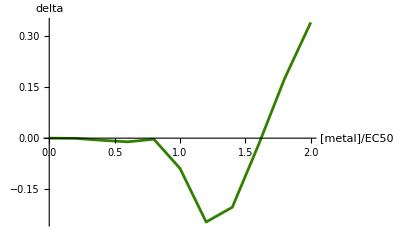

```mathematica
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

2.9031

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

10.971

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

1.48844

#### CuNi growth data: a = –1.9***

```mathematica
ypad="YPAD";
single1="Cu";
single2="Ni";
double="CuNi";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{8.83,0,1.2866},{8.83,0,1.4425},{10.17,0,1.0509},{10.17,0,0.9717},{10.83,0,0.8337},{10.83,0,0.8388},{12.,0,0.7934},{12.,0,0.911},{13.5,0,0.0144},{13.5,0,0.0575},{4.,0,1.1996},{4.,0,1.3127},{8.83,0,0.9746},{8.83,0,0.9672},{10.17,0,0.7667},{10.17,0,0.7767},{10.85,0,0.8112},{10.85,0,0.7962},{12.9,0,0.0137},{12.9,0,0.0134}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,1.88,1.477},{0,1.88,1.4318},{0,2.4,1.469},{0,2.4,1.371},{0,3.,0.8652},{0,3.,0.9787},{0,3.6,0.5413},{0,3.6,0.5766},{0,5.1,0.0206},{0,5.1,0.005},{0,2.3,1.4688},{0,2.3,1.4886},{0,2.6,1.4167},{0,2.6,1.3268},{0,2.75,0.871},{0,2.75,0.926},{0,3.,0.5344},{0,3.,0.5202},{0,3.2,0.032},{0,3.2,0.0312}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{8.83,1.88,0.0057},{8.83,1.88,0.0089},{8.83,1.88,0.0107},{10.17,2.4,0.0041},{10.17,2.4,0.0087},{10.17,2.4,0.0002},{10.83,3.,0.0029},{10.83,3.,0.0069},{10.83,3.,0.0048},{12.,3.6,0.0216},{12.,3.6,0.0174},{12.,3.6,0.0373},{13.5,5.1,0.0422},{13.5,5.1,0.0383},{13.5,5.1,0.0435},{4.,2.3,0.0084},{4.,2.3,0.0032},{4.,2.3,0.0107},{8.83,2.6,0.0073},{8.83,2.6,0.0076},{8.83,2.6,0.0059},{10.17,2.75,0.0188},{10.17,2.75,0.0065},{10.17,2.75,0.0129},{10.85,3.,0.0185},{10.85,3.,0.0106},{10.85,3.,0.0311},{12.9,3.2,0.0467},{12.9,3.2,0.0402},{12.9,3.2,0.0327}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.83 | 8.83 | 10.17 | 10.17 | 10.83 | 10.83 | 12. | 12. | 13.5 | 13.5 | 4. | 4. | 8.83 | 8.83 | 10.17 | 10.17 | 10.85 | 10.85 | 12.9 | 12.9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.83 | 10.83 | 10.83 | 12. | 12. | 12. | 13.5 | 13.5 | 13.5 | 4. | 4. | 4. | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.85 | 10.85 | 10.85 | 12.9 | 12.9 | 12.9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.88 | 1.88 | 2.4 | 2.4 | 3. | 3. | 3.6 | 3.6 | 5.1 | 5.1 | 2.3 | 2.3 | 2.6 | 2.6 | 2.75 | 2.75 | 3. | 3. | 3.2 | 3.2 | 1.88 | 1.88 | 1.88 | 2.4 | 2.4 | 2.4 | 3. | 3. | 3. | 3.6 | 3.6 | 3.6 | 5.1 | 5.1 | 5.1 | 2.3 | 2.3 | 2.3 | 2.6 | 2.6 | 2.6 | 2.75 | 2.75 | 2.75 | 3. | 3. | 3. | 3.2 | 3.2 | 3.2
1.4598 | 1.4544 | 1.4005 | 1.4594 | 1.4188 | 1.5012 | 1.4445 | 1.5353 | 1.5101 | 1.5665 | 1.2866 | 1.4425 | 1.0509 | 0.9717 | 0.8337 | 0.8388 | 0.7934 | 0.911 | 0.0144 | 0.0575 | 1.1996 | 1.3127 | 0.9746 | 0.9672 | 0.7667 | 0.7767 | 0.8112 | 0.7962 | 0.0137 | 0.0134 | 1.477 | 1.4318 | 1.469 | 1.371 | 0.8652 | 0.9787 | 0.5413 | 0.5766 | 0.0206 | 0.005 | 1.4688 | 1.4886 | 1.4167 | 1.3268 | 0.871 | 0.926 | 0.5344 | 0.5202 | 0.032 | 0.0312 | 0.0057 | 0.0089 | 0.0107 | 0.0041 | 0.0087 | 0.0002 | 0.0029 | 0.0069 | 0.0048 | 0.0216 | 0.0174 | 0.0373 | 0.0422 | 0.0383 | 0.0435 | 0.0084 | 0.0032 | 0.0107 | 0.0073 | 0.0076 | 0.0059 | 0.0188 | 0.0065 | 0.0129 | 0.0185 | 0.0106 | 0.0311 | 0.0467 | 0.0402 | 0.0327)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{8.83,1.2866},{8.83,1.4425},{10.17,1.0509},{10.17,0.9717},{10.83,0.8337},{10.83,0.8388},{12.,0.7934},{12.,0.911},{13.5,0.0144},{13.5,0.0575},{4.,1.1996},{4.,1.3127},{8.83,0.9746},{8.83,0.9672},{10.17,0.7667},{10.17,0.7767},{10.85,0.8112},{10.85,0.7962},{12.9,0.0137},{12.9,0.0134}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→1.42242,EC501→11.0364,β1→8.48113}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{1.88,1.477},{1.88,1.4318},{2.4,1.469},{2.4,1.371},{3.,0.8652},{3.,0.9787},{3.6,0.5413},{3.6,0.5766},{5.1,0.0206},{5.1,0.005},{2.3,1.4688},{2.3,1.4886},{2.6,1.4167},{2.6,1.3268},{2.75,0.871},{2.75,0.926},{3.,0.5344},{3.,0.5202},{3.2,0.032},{3.2,0.0312}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→1.49104,EC502→2.93571,β2→12.8529}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{1.45673,11.0364,8.48113,2.93571,12.8529}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

2.11253

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{2.24558,{max→1.47123,EC501→10.857,β1→8.6577,EC502→2.929,β2→10.}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{29.4074,{max→1.47123,EC501→10.857,β1→8.65762,EC502→2.929,β2→9.99996,σ→0.16754}}

Here the fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.0000673297,0.0000398687,0.000957634,0.0000146391,0.000346788}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{1.95886,{max→1.4673,EC501→10.926,β1→8.02462,EC502→2.96285,β2→10.,a→-1.90914}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{34.8714,{max→1.4673,EC501→10.926,β1→8.02461,EC502→2.96285,β2→9.99999,a→-1.90917,σ→0.156479}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-5.74628×10^-6,2.86278×10^-6,0.0000553637,-1.38924×10^-6,0.0000955374,-0.00170466}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841. This is marginally SIGNIFICANT:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

0.000947218

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.0198659,0.906022,0.997228,0.999765,0.999945,0.999967,0.999973,0.999975,0.999977,0.999979}

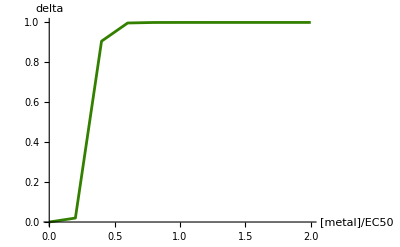

```mathematica
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

-1.90917

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

10.926

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

2.96285

#### CuZn growth data: a = –2.2***

```mathematica
ypad="YPAD";
single1="Cu";
single2="Zn";
double="CuZn";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{8.83,0,1.2866},{8.83,0,1.4425},{10.17,0,1.0509},{10.17,0,0.9717},{10.83,0,0.8337},{10.83,0,0.8388},{12.,0,0.7934},{12.,0,0.911},{13.5,0,0.0144},{13.5,0,0.0575},{4.,0,1.1996},{4.,0,1.3127},{8.83,0,0.9746},{8.83,0,0.9672},{10.17,0,0.7667},{10.17,0,0.7767},{10.85,0,0.8112},{10.85,0,0.7962},{12.9,0,0.0137},{12.9,0,0.0134}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,4.,1.336},{0,4.,1.3572},{0,4.75,1.2102},{0,4.75,1.2322},{0,5.4,0.9341},{0,5.4,1.0006},{0,6.,0.6473},{0,6.,0.6677},{0,6.6,0.171},{0,6.6,0.1993},{0,3.33,1.2977},{0,3.33,1.3343},{0,4.,1.2007},{0,4.,1.2182},{0,4.8,0.9505},{0,4.8,0.9968},{0,5.4,0.685},{0,5.4,0.7097},{0,6.,0.3027},{0,6.,0.283}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{8.83,4.,0.0197},{8.83,4.,0.013},{8.83,4.,0.0165},{10.17,4.75,0.0283},{10.17,4.75,0.0324},{10.17,4.75,0.0202},{10.83,5.4,0.0275},{10.83,5.4,0.0248},{10.83,5.4,0.0293},{12.,6.,0.0575},{12.,6.,0.0384},{12.,6.,0.038},{13.5,6.6,0.0407},{13.5,6.6,0.0414},{13.5,6.6,0.0295},{4.,3.33,0.0284},{4.,3.33,0.0177},{4.,3.33,0.0172},{8.83,4.,0.0256},{8.83,4.,0.0042},{8.83,4.,0.0248},{10.17,4.8,0.0271},{10.17,4.8,0.01},{10.17,4.8,-0.018},{10.85,5.4,0.0428},{10.85,5.4,0.0441},{10.85,5.4,0.0441},{12.9,6.,0.0298},{12.9,6.,0.0355},{12.9,6.,0.0063}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.83 | 8.83 | 10.17 | 10.17 | 10.83 | 10.83 | 12. | 12. | 13.5 | 13.5 | 4. | 4. | 8.83 | 8.83 | 10.17 | 10.17 | 10.85 | 10.85 | 12.9 | 12.9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.83 | 10.83 | 10.83 | 12. | 12. | 12. | 13.5 | 13.5 | 13.5 | 4. | 4. | 4. | 8.83 | 8.83 | 8.83 | 10.17 | 10.17 | 10.17 | 10.85 | 10.85 | 10.85 | 12.9 | 12.9 | 12.9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4. | 4. | 4.75 | 4.75 | 5.4 | 5.4 | 6. | 6. | 6.6 | 6.6 | 3.33 | 3.33 | 4. | 4. | 4.8 | 4.8 | 5.4 | 5.4 | 6. | 6. | 4. | 4. | 4. | 4.75 | 4.75 | 4.75 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6. | 6.6 | 6.6 | 6.6 | 3.33 | 3.33 | 3.33 | 4. | 4. | 4. | 4.8 | 4.8 | 4.8 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6.
1.4598 | 1.4544 | 1.4005 | 1.4594 | 1.4188 | 1.5012 | 1.4445 | 1.5353 | 1.5101 | 1.5665 | 1.2866 | 1.4425 | 1.0509 | 0.9717 | 0.8337 | 0.8388 | 0.7934 | 0.911 | 0.0144 | 0.0575 | 1.1996 | 1.3127 | 0.9746 | 0.9672 | 0.7667 | 0.7767 | 0.8112 | 0.7962 | 0.0137 | 0.0134 | 1.336 | 1.3572 | 1.2102 | 1.2322 | 0.9341 | 1.0006 | 0.6473 | 0.6677 | 0.171 | 0.1993 | 1.2977 | 1.3343 | 1.2007 | 1.2182 | 0.9505 | 0.9968 | 0.685 | 0.7097 | 0.3027 | 0.283 | 0.0197 | 0.013 | 0.0165 | 0.0283 | 0.0324 | 0.0202 | 0.0275 | 0.0248 | 0.0293 | 0.0575 | 0.0384 | 0.038 | 0.0407 | 0.0414 | 0.0295 | 0.0284 | 0.0177 | 0.0172 | 0.0256 | 0.0042 | 0.0248 | 0.0271 | 0.01 | -0.018 | 0.0428 | 0.0441 | 0.0441 | 0.0298 | 0.0355 | 0.0063)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{8.83,1.2866},{8.83,1.4425},{10.17,1.0509},{10.17,0.9717},{10.83,0.8337},{10.83,0.8388},{12.,0.7934},{12.,0.911},{13.5,0.0144},{13.5,0.0575},{4.,1.1996},{4.,1.3127},{8.83,0.9746},{8.83,0.9672},{10.17,0.7667},{10.17,0.7767},{10.85,0.8112},{10.85,0.7962},{12.9,0.0137},{12.9,0.0134}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→1.42242,EC501→11.0364,β1→8.48113}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{4.,1.336},{4.,1.3572},{4.75,1.2102},{4.75,1.2322},{5.4,0.9341},{5.4,1.0006},{6.,0.6473},{6.,0.6677},{6.6,0.171},{6.6,0.1993},{3.33,1.2977},{3.33,1.3343},{4.,1.2007},{4.,1.2182},{4.8,0.9505},{4.8,0.9968},{5.4,0.685},{5.4,0.7097},{6.,0.3027},{6.,0.283}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→1.44066,EC502→5.51042,β2→8.06572}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{1.43154,11.0364,8.48113,5.51042,8.06572}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

3.16851

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{2.9173,{max→1.42833,EC501→10.7776,β1→8.21659,EC502→5.28166,β2→7.61902}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{18.9397,{max→1.42833,EC501→10.7776,β1→8.21648,EC502→5.28166,β2→7.61896,σ→0.190961}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-0.000111612,0.0000558264,0.00129649,0.0000377179,0.000754899}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{1.26682,{max→1.39905,EC501→11.094,β1→8.74333,EC502→5.5628,β2→8.7624,a→-2.19369}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{52.3055,{max→1.39905,EC501→11.094,β1→8.74332,EC502→5.5628,β2→8.76239,a→-2.19369,σ→0.125838}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-0.0000120692,4.30767×10^-6,0.0000808179,4.22153×10^-6,0.000116089,-0.000105705}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841, which it is:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

3.33067×10^-16

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.01,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.01,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction, the fit is much better:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.01,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.01,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.038423,0.945151,0.998316,0.999846,0.999962,0.999977,0.99998,0.999981,0.999981,0.999981}

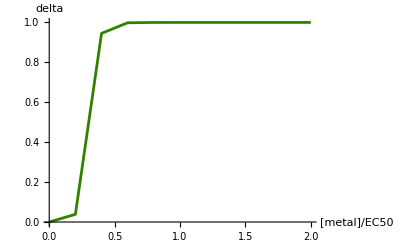

```mathematica
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

Except for very low metal concentrations, the deltas are near one (maximum synergistic toxicity)

```mathematica
a[double]=a/.maxlla[[2]]
```

-2.19369

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

11.094

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

5.5628

#### MnNi growth data: a = 2.1 [Need to fix]

```mathematica
ypad="YPAD";
single1="Mn";
single2="Ni";
double="MnNi";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.86,0,1.4523},{0.86,0,1.3266},{1.14,0,0.9145},{1.14,0,1.0459},{1.31,0,1.067},{1.31,0,1.1458},{1.66,0,0.7365},{1.66,0,0.726},{2.23,0,0.4567},{2.23,0,0.4334},{0.85,0,1.3842},{0.85,0,1.3551},{1.,0,1.0278},{1.,0,1.0112},{1.14,0,0.957},{1.14,0,0.9658},{1.25,0,0.775},{1.25,0,0.7677},{1.6,0,0.479},{1.6,0,0.5157}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,1.88,1.477},{0,1.88,1.4318},{0,2.4,1.469},{0,2.4,1.371},{0,3.,0.8652},{0,3.,0.9787},{0,3.6,0.5413},{0,3.6,0.5766},{0,5.1,0.0206},{0,5.1,0.005},{0,2.3,1.4688},{0,2.3,1.4886},{0,2.6,1.4167},{0,2.6,1.3268},{0,2.75,0.871},{0,2.75,0.926},{0,3.,0.5344},{0,3.,0.5202},{0,3.2,0.032},{0,3.2,0.0312}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.86,1.88,1.3907},{0.86,1.88,1.4711},{0.86,1.88,1.4157},{1.14,2.4,0.865},{1.14,2.4,0.8715},{1.14,2.4,0.9805},{1.31,3.,0.613},{1.31,3.,0.5631},{1.31,3.,0.6433},{1.66,3.6,0.1528},{1.66,3.6,0.0815},{1.66,3.6,0.1667},{2.23,5.1,0.015},{2.23,5.1,0.0286},{2.23,5.1,0.0192},{0.85,2.3,1.4413},{0.85,2.3,1.4421},{0.85,2.3,1.4795},{1.,2.6,0.871},{1.,2.6,0.8337},{1.,2.6,0.8709},{1.14,2.75,0.7055},{1.14,2.75,0.6026},{1.14,2.75,0.5783},{1.25,3.,0.1413},{1.25,3.,0.1802},{1.25,3.,0.218},{1.6,3.2,0.0081},{1.6,3.2,0.0182},{1.6,3.2,0.0295}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86 | 0.86 | 1.14 | 1.14 | 1.31 | 1.31 | 1.66 | 1.66 | 2.23 | 2.23 | 0.85 | 0.85 | 1. | 1. | 1.14 | 1.14 | 1.25 | 1.25 | 1.6 | 1.6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86 | 0.86 | 0.86 | 1.14 | 1.14 | 1.14 | 1.31 | 1.31 | 1.31 | 1.66 | 1.66 | 1.66 | 2.23 | 2.23 | 2.23 | 0.85 | 0.85 | 0.85 | 1. | 1. | 1. | 1.14 | 1.14 | 1.14 | 1.25 | 1.25 | 1.25 | 1.6 | 1.6 | 1.6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.88 | 1.88 | 2.4 | 2.4 | 3. | 3. | 3.6 | 3.6 | 5.1 | 5.1 | 2.3 | 2.3 | 2.6 | 2.6 | 2.75 | 2.75 | 3. | 3. | 3.2 | 3.2 | 1.88 | 1.88 | 1.88 | 2.4 | 2.4 | 2.4 | 3. | 3. | 3. | 3.6 | 3.6 | 3.6 | 5.1 | 5.1 | 5.1 | 2.3 | 2.3 | 2.3 | 2.6 | 2.6 | 2.6 | 2.75 | 2.75 | 2.75 | 3. | 3. | 3. | 3.2 | 3.2 | 3.2
1.4598 | 1.4544 | 1.4005 | 1.4594 | 1.4188 | 1.5012 | 1.4445 | 1.5353 | 1.5101 | 1.5665 | 1.4523 | 1.3266 | 0.9145 | 1.0459 | 1.067 | 1.1458 | 0.7365 | 0.726 | 0.4567 | 0.4334 | 1.3842 | 1.3551 | 1.0278 | 1.0112 | 0.957 | 0.9658 | 0.775 | 0.7677 | 0.479 | 0.5157 | 1.477 | 1.4318 | 1.469 | 1.371 | 0.8652 | 0.9787 | 0.5413 | 0.5766 | 0.0206 | 0.005 | 1.4688 | 1.4886 | 1.4167 | 1.3268 | 0.871 | 0.926 | 0.5344 | 0.5202 | 0.032 | 0.0312 | 1.3907 | 1.4711 | 1.4157 | 0.865 | 0.8715 | 0.9805 | 0.613 | 0.5631 | 0.6433 | 0.1528 | 0.0815 | 0.1667 | 0.015 | 0.0286 | 0.0192 | 1.4413 | 1.4421 | 1.4795 | 0.871 | 0.8337 | 0.8709 | 0.7055 | 0.6026 | 0.5783 | 0.1413 | 0.1802 | 0.218 | 0.0081 | 0.0182 | 0.0295)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{0.86,1.4523},{0.86,1.3266},{1.14,0.9145},{1.14,1.0459},{1.31,1.067},{1.31,1.1458},{1.66,0.7365},{1.66,0.726},{2.23,0.4567},{2.23,0.4334},{0.85,1.3842},{0.85,1.3551},{1.,1.0278},{1.,1.0112},{1.14,0.957},{1.14,0.9658},{1.25,0.775},{1.25,0.7677},{1.6,0.479},{1.6,0.5157}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→1.48792,EC501→1.50209,β1→2.8948}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{1.88,1.477},{1.88,1.4318},{2.4,1.469},{2.4,1.371},{3.,0.8652},{3.,0.9787},{3.6,0.5413},{3.6,0.5766},{5.1,0.0206},{5.1,0.005},{2.3,1.4688},{2.3,1.4886},{2.6,1.4167},{2.6,1.3268},{2.75,0.871},{2.75,0.926},{3.,0.5344},{3.,0.5202},{3.2,0.032},{3.2,0.0312}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→1.49104,EC502→2.93571,β2→12.8529}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{1.48948,1.50209,2.8948,2.93571,12.8529}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

14.6223

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

FindMinimum::nrnum: The function value -182.134-76.0207 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.6523,1.82392,0.448636,2.91163,9.69414}.

FindMinimum::nrnum: The function value 115.722-582.796 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.67662,1.94634,0.484821,2.91339,7.09058}.

FindMinimum::nrnum: The function value 115.72-582.788 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.67661,1.94634,0.484821,2.91339,7.09058}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{6.77839,{max→1.7279,EC501→2.09229,β1→0.229302,EC502→2.78666,β2→7.74569}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

FindMaximum::nrnum: The function value -614.211-687.005 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {1.67572,2.17973,0.442951,2.85478,9.48944,0.275655}.

FindMaximum::nrnum: The function value -594.198-2069.08 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {1.66146,2.17351,0.473584,2.88855,9.08101,0.282625}.

FindMaximum::nrnum: The function value -594.196-2069.05 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {1.66145,2.17351,0.473584,2.88855,9.08101,0.282625}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::steperr: Error in step computation.

FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset⟦All,1⟧],0<β1<10,0<EC502<Max[dataset⟦All,2⟧],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]

Restarting the ML fit from the sum of squares fit leads to a better fit:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,max/.ssq[[2]]},{EC501,EC501/.ssq[[2]]},{β1,β1/.ssq[[2]]},{EC502,EC502/.ssq[[2]]},{β2,β2/.ssq[[2]]},{σ,0.04,0,1}}]
```

FindMaximum::nrnum: The function value -3536.58-14057.2 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {1.7279,2.09229,0.229424,2.78666,7.74569,0.04}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset⟦All,1⟧],0<β1<10,0<EC502<Max[dataset⟦All,2⟧],0<β2<10},{{max,max/.ssq⟦2⟧},{EC501,EC501/.ssq⟦2⟧},{β1,β1/.ssq⟦2⟧},{EC502,EC502/.ssq⟦2⟧},{β2,β2/.ssq⟦2⟧},{σ,0.04,0,1}}]

Here the fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

FindMaximum::nrnum: The function value -3536.58-14057.2 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {1.7279,2.09229,0.229424,2.78666,7.74569,0.04}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

ReplaceAll::reps: {max,1.7279} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {EC501,2.09229} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {β1,0.229302} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {1.7279,2.09229,0.229302,2.78666,7.74569}+{-({max,EC501,β1,EC502,β2}/.{max,1.7279}),-({max,EC501,β1,EC502,β2}/.{EC501,2.09229}),-({max,EC501,β1,EC502,β2}/.{β1,0.229302}),-(«1»),-({max,EC501,β1,EC502,β2}/.{β2,7.74569}),-({max,EC501,β1,EC502,β2}/.{σ,0.04,0,1})} cannot be combined.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{(100 ({1.7279,2.09229,0.229302,2.78666,7.74569}+{-({max,EC501,β1,EC502,β2}/.{max,1.7279}),-({max,EC501,β1,EC502,β2}/.{EC501,2.09229}),-({max,EC501,β1,EC502,β2}/.{β1,0.229302}),-({max,EC501,β1,EC502,β2}/.{EC502,2.78666}),-({max,EC501,β1,EC502,β2}/.{β2,7.74569}),-({max,EC501,β1,EC502,β2}/.{σ,0.04,0,1})}))/({max,EC501,β1,EC502,β2}/.{max,1.7279}),(100 ({1.7279,2.09229,0.229302,2.78666,7.74569}+{-({max,EC501,β1,EC502,β2}/.{max,1.7279}),-({max,EC501,β1,EC502,β2}/.{EC501,2.09229}),-({max,EC501,β1,EC502,β2}/.{β1,0.229302}),-({max,EC501,β1,EC502,β2}/.{EC502,2.78666}),-({max,EC501,β1,EC502,β2}/.{β2,7.74569}),-({max,EC501,β1,EC502,β2}/.{σ,0.04,0,1})}))/({max,EC501,β1,EC502,β2}/.{EC501,2.09229}),(100 ({1.7279,2.09229,0.229302,2.78666,7.74569}+{-({max,EC501,β1,EC502,β2}/.{max,1.7279}),-({max,EC501,β1,EC502,β2}/.{EC501,2.09229}),-({max,EC501,β1,EC502,β2}/.{β1,0.229302}),-({max,EC501,β1,EC502,β2}/.{EC502,2.78666}),-({max,EC501,β1,EC502,β2}/.{β2,7.74569}),-({max,EC501,β1,EC502,β2}/.{σ,0.04,0,1})}))/({max,EC501,β1,EC502,β2}/.{β1,0.229302}),(100 ({1.7279,2.09229,0.229302,2.78666,7.74569}+{-({max,EC501,β1,EC502,β2}/.{max,1.7279}),-({max,EC501,β1,EC502,β2}/.{EC501,2.09229}),-({max,EC501,β1,EC502,β2}/.{β1,0.229302}),-({max,EC501,β1,EC502,β2}/.{EC502,2.78666}),-({max,EC501,β1,EC502,β2}/.{β2,7.74569}),-({max,EC501,β1,EC502,β2}/.{σ,0.04,0,1})}))/({max,EC501,β1,EC502,β2}/.{EC502,2.78666}),(100 ({1.7279,2.09229,0.229302,2.78666,7.74569}+{-({max,EC501,β1,EC502,β2}/.{max,1.7279}),-({max,EC501,β1,EC502,β2}/.{EC501,2.09229}),-({max,EC501,β1,EC502,β2}/.{β1,0.229302}),-({max,EC501,β1,EC502,β2}/.{EC502,2.78666}),-({max,EC501,β1,EC502,β2}/.{β2,7.74569}),-({max,EC501,β1,EC502,β2}/.{σ,0.04,0,1})}))/({max,EC501,β1,EC502,β2}/.{β2,7.74569}),(100 ({1.7279,2.09229,0.229302,2.78666,7.74569}+{-({max,EC501,β1,EC502,β2}/.{max,1.7279}),-({max,EC501,β1,EC502,β2}/.{EC501,2.09229}),-({max,EC501,β1,EC502,β2}/.{β1,0.229302}),-({max,EC501,β1,EC502,β2}/.{EC502,2.78666}),-({max,EC501,β1,EC502,β2}/.{β2,7.74569}),-({max,EC501,β1,EC502,β2}/.{σ,0.04,0,1})}))/({max,EC501,β1,EC502,β2}/.{σ,0.04,0,1})}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{2.44065,{max→1.52924,EC501→1.40971,β1→4.2236,EC502→2.93032,β2→10.,a→2.09432}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{26.0753,{max→1.52924,EC501→1.40971,β1→4.2236,EC502→2.93032,β2→9.99999,a→2.09432,σ→0.174666}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-4.17875×10^-6,5.30181×10^-6,-7.89863×10^-6,-1.09171×10^-6,0.000120091,6.27834×10^-7}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841. This is SIGNIFICANT:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

FindMaximum::nrnum: The function value -3536.58-14057.2 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {1.7279,2.09229,0.229424,2.78666,7.74569,0.04}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{1-(Piecewise[{{GammaRegularized[1/2,0,26.0753-lnlikelihood[max,EC501,β1,EC502,β2,σ,{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665},{0.86,0,1.4523},{0.86,0,1.3266},{1.14,0,0.9145},{1.14,0,1.0459},{1.31,0,1.067},{1.31,0,1.1458},{1.66,0,0.7365},{1.66,0,0.726},{2.23,0,0.4567},{2.23,0,0.4334},{0.85,0,1.3842},{0.85,0,1.3551},{1.,0,1.0278},{1.,0,1.0112},{1.14,0,0.957},{1.14,0,0.9658},{1.25,0,0.775},{1.25,0,0.7677},{1.6,0,0.479},{1.6,0,0.5157},{0,1.88,1.477},{0,1.88,1.4318},{0,2.4,1.469},{0,2.4,1.371},{0,3.,0.8652},{0,3.,0.9787},{0,3.6,0.5413},{0,3.6,0.5766},{0,5.1,0.0206},{0,5.1,0.005},{0,2.3,1.4688},{0,2.3,1.4886},{0,2.6,1.4167},{0,2.6,1.3268},{0,2.75,0.871},{0,2.75,0.926},{0,3.,0.5344},{0,3.,0.5202},{0,3.2,0.032},{0,3.2,0.0312},{0.86,1.88,1.3907},{0.86,1.88,1.4711},{0.86,1.88,1.4157},{1.14,2.4,0.865},{1.14,2.4,0.8715},{1.14,2.4,0.9805},{1.31,3.,0.613},{1.31,3.,0.5631},{1.31,3.,0.6433},{1.66,3.6,0.1528},{1.66,3.6,0.0815},{1.66,3.6,0.1667},{2.23,5.1,0.015},{2.23,5.1,0.0286},{2.23,5.1,0.0192},{0.85,2.3,1.4413},{0.85,2.3,1.4421},{0.85,2.3,1.4795},{1.,2.6,0.871},{1.,2.6,0.8337},{1.,2.6,0.8709},{1.14,2.75,0.7055},{1.14,2.75,0.6026},{1.14,2.75,0.5783},{1.25,3.,0.1413},{1.25,3.,0.1802},{1.25,3.,0.218},{1.6,3.2,0.0081},{1.6,3.2,0.0182},{1.6,3.2,0.0295}}]], 2 (26.0753-lnlikelihood[max,EC501,β1,EC502,β2,σ,{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665},{0.86,0,1.4523},{0.86,0,1.3266},{1.14,0,0.9145},{1.14,0,1.0459},{1.31,0,1.067},{1.31,0,1.1458},{1.66,0,0.7365},{1.66,0,0.726},{2.23,0,0.4567},{2.23,0,0.4334},{0.85,0,1.3842},{0.85,0,1.3551},{1.,0,1.0278},{1.,0,1.0112},{1.14,0,0.957},{1.14,0,0.9658},{1.25,0,0.775},{1.25,0,0.7677},{1.6,0,0.479},{1.6,0,0.5157},{0,1.88,1.477},{0,1.88,1.4318},{0,2.4,1.469},{0,2.4,1.371},{0,3.,0.8652},{0,3.,0.9787},{0,3.6,0.5413},{0,3.6,0.5766},{0,5.1,0.0206},{0,5.1,0.005},{0,2.3,1.4688},{0,2.3,1.4886},{0,2.6,1.4167},{0,2.6,1.3268},{0,2.75,0.871},{0,2.75,0.926},{0,3.,0.5344},{0,3.,0.5202},{0,3.2,0.032},{0,3.2,0.0312},{0.86,1.88,1.3907},{0.86,1.88,1.4711},{0.86,1.88,1.4157},{1.14,2.4,0.865},{1.14,2.4,0.8715},{1.14,2.4,0.9805},{1.31,3.,0.613},{1.31,3.,0.5631},{1.31,3.,0.6433},{1.66,3.6,0.1528},{1.66,3.6,0.0815},{1.66,3.6,0.1667},{2.23,5.1,0.015},{2.23,5.1,0.0286},{2.23,5.1,0.0192},{0.85,2.3,1.4413},{0.85,2.3,1.4421},{0.85,2.3,1.4795},{1.,2.6,0.871},{1.,2.6,0.8337},{1.,2.6,0.8709},{1.14,2.75,0.7055},{1.14,2.75,0.6026},{1.14,2.75,0.5783},{1.25,3.,0.1413},{1.25,3.,0.1802},{1.25,3.,0.218},{1.6,3.2,0.0081},{1.6,3.2,0.0182},{1.6,3.2,0.0295}}])>0}, {0., True}}]),1-(Piecewise[{{GammaRegularized[1/2,0,26.0753-(0<max<2)], 2 (26.0753-(0<max<2))>0}, {0., True}}]),1-(Piecewise[{{GammaRegularized[1/2,0,26.0753-(0<EC501<2.23)], 2 (26.0753-(0<EC501<2.23))>0}, {0., True}}]),1-(Piecewise[{{GammaRegularized[1/2,0,26.0753-(0<β1<10)], 2 (26.0753-(0<β1<10))>0}, {0., True}}]),1-(Piecewise[{{GammaRegularized[1/2,0,26.0753-(0<EC502<5.1)], 2 (26.0753-(0<EC502<5.1))>0}, {0., True}}]),1-(Piecewise[{{GammaRegularized[1/2,0,26.0753-(0<β2<10)], 2 (26.0753-(0<β2<10))>0}, {0., True}}])}

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/100},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/100}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

FindMaximum::nrnum: The function value -3536.58-14057.2 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {1.7279,2.09229,0.229424,2.78666,7.74569,0.04}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

ReplaceAll::reps: {max,1.7279} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {EC501,2.09229} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {β1,0.229302} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMaximum::cvmit will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit::reclim will be suppressed during this calculation.

$Aborted

With an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,-0.000128426,0.00464493,0.0711691,0.286912,0.470535,0.543565,0.636366,0.728214,0.798443,0.84892}

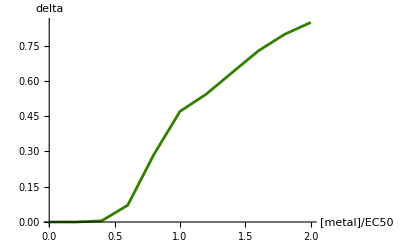

```mathematica
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

2.09432

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

1.40971

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

2.93032

#### MnZn growth data: a = 3.3***

```mathematica
ypad="YPAD";
single1="Mn";
single2="Zn";
double="MnZn";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.86,0,1.4523},{0.86,0,1.3266},{1.14,0,0.9145},{1.14,0,1.0459},{1.31,0,1.067},{1.31,0,1.1458},{1.66,0,0.7365},{1.66,0,0.726},{2.23,0,0.4567},{2.23,0,0.4334},{0.85,0,1.3842},{0.85,0,1.3551},{1.,0,1.0278},{1.,0,1.0112},{1.14,0,0.957},{1.14,0,0.9658},{1.25,0,0.775},{1.25,0,0.7677},{1.6,0,0.479},{1.6,0,0.5157}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,4.,1.336},{0,4.,1.3572},{0,4.75,1.2102},{0,4.75,1.2322},{0,5.4,0.9341},{0,5.4,1.0006},{0,6.,0.6473},{0,6.,0.6677},{0,6.6,0.171},{0,6.6,0.1993},{0,3.33,1.2977},{0,3.33,1.3343},{0,4.,1.2007},{0,4.,1.2182},{0,4.8,0.9505},{0,4.8,0.9968},{0,5.4,0.685},{0,5.4,0.7097},{0,6.,0.3027},{0,6.,0.283}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0.86,4.,1.3332},{0.86,4.,1.3093},{0.86,4.,1.292},{1.14,4.75,1.316},{1.14,4.75,1.2546},{1.14,4.75,1.322},{1.31,5.4,1.1493},{1.31,5.4,1.0929},{1.31,5.4,1.1846},{1.66,6.,1.0254},{1.66,6.,1.0647},{1.66,6.,0.944},{2.23,6.6,0.5565},{2.23,6.6,0.5858},{2.23,6.6,0.5843},{0.85,3.33,1.3982},{0.85,3.33,1.343},{0.85,3.33,1.291},{1.,4.,1.2501},{1.,4.,1.2185},{1.,4.,1.2309},{1.14,4.8,1.122},{1.14,4.8,1.203},{1.14,4.8,1.114},{1.25,5.4,0.9658},{1.25,5.4,0.8792},{1.25,5.4,0.9902},{1.6,6.,0.599},{1.6,6.,0.5812},{1.6,6.,0.4716}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86 | 0.86 | 1.14 | 1.14 | 1.31 | 1.31 | 1.66 | 1.66 | 2.23 | 2.23 | 0.85 | 0.85 | 1. | 1. | 1.14 | 1.14 | 1.25 | 1.25 | 1.6 | 1.6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86 | 0.86 | 0.86 | 1.14 | 1.14 | 1.14 | 1.31 | 1.31 | 1.31 | 1.66 | 1.66 | 1.66 | 2.23 | 2.23 | 2.23 | 0.85 | 0.85 | 0.85 | 1. | 1. | 1. | 1.14 | 1.14 | 1.14 | 1.25 | 1.25 | 1.25 | 1.6 | 1.6 | 1.6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4. | 4. | 4.75 | 4.75 | 5.4 | 5.4 | 6. | 6. | 6.6 | 6.6 | 3.33 | 3.33 | 4. | 4. | 4.8 | 4.8 | 5.4 | 5.4 | 6. | 6. | 4. | 4. | 4. | 4.75 | 4.75 | 4.75 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6. | 6.6 | 6.6 | 6.6 | 3.33 | 3.33 | 3.33 | 4. | 4. | 4. | 4.8 | 4.8 | 4.8 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6.
1.4598 | 1.4544 | 1.4005 | 1.4594 | 1.4188 | 1.5012 | 1.4445 | 1.5353 | 1.5101 | 1.5665 | 1.4523 | 1.3266 | 0.9145 | 1.0459 | 1.067 | 1.1458 | 0.7365 | 0.726 | 0.4567 | 0.4334 | 1.3842 | 1.3551 | 1.0278 | 1.0112 | 0.957 | 0.9658 | 0.775 | 0.7677 | 0.479 | 0.5157 | 1.336 | 1.3572 | 1.2102 | 1.2322 | 0.9341 | 1.0006 | 0.6473 | 0.6677 | 0.171 | 0.1993 | 1.2977 | 1.3343 | 1.2007 | 1.2182 | 0.9505 | 0.9968 | 0.685 | 0.7097 | 0.3027 | 0.283 | 1.3332 | 1.3093 | 1.292 | 1.316 | 1.2546 | 1.322 | 1.1493 | 1.0929 | 1.1846 | 1.0254 | 1.0647 | 0.944 | 0.5565 | 0.5858 | 0.5843 | 1.3982 | 1.343 | 1.291 | 1.2501 | 1.2185 | 1.2309 | 1.122 | 1.203 | 1.114 | 0.9658 | 0.8792 | 0.9902 | 0.599 | 0.5812 | 0.4716)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{0.86,1.4523},{0.86,1.3266},{1.14,0.9145},{1.14,1.0459},{1.31,1.067},{1.31,1.1458},{1.66,0.7365},{1.66,0.726},{2.23,0.4567},{2.23,0.4334},{0.85,1.3842},{0.85,1.3551},{1.,1.0278},{1.,1.0112},{1.14,0.957},{1.14,0.9658},{1.25,0.775},{1.25,0.7677},{1.6,0.479},{1.6,0.5157}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→1.48792,EC501→1.50209,β1→2.8948}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{4.,1.336},{4.,1.3572},{4.75,1.2102},{4.75,1.2322},{5.4,0.9341},{5.4,1.0006},{6.,0.6473},{6.,0.6677},{6.6,0.171},{6.6,0.1993},{3.33,1.2977},{3.33,1.3343},{4.,1.2007},{4.,1.2182},{4.8,0.9505},{4.8,0.9968},{5.4,0.685},{5.4,0.7097},{6.,0.3027},{6.,0.283}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→1.44066,EC502→5.51042,β2→8.06572}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{1.46429,1.50209,2.8948,5.51042,8.06572}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

26.022

Minimizing the sum of squares fails to find a solution:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

FindMinimum::nrnum: The function value 1.3712×10^7+0.00149723 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.7715,1.53292,0.17111,5.36768,3.9731}.

FindMinimum::nrnum: The function value -181.261+385.532 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.76327,1.53292,0.159389,5.36768,3.9731}.

FindMinimum::nrnum: The function value 7464.21-13.9344 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.74688,1.5317,0.126817,5.36767,3.97309}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{28.4238,{max→0.936383,EC501→2.18326,β1→9.22571,EC502→6.6,β2→4.67605}}

```mathematica
FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset⟦All,1⟧],0<β1<10,0<EC502<Max[dataset⟦All,2⟧],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

FindMinimum::nrnum: The function value 1.3712×10^7+0.00149723 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.7715,1.53292,0.17111,5.36768,3.9731}.

FindMinimum::nrnum: The function value -181.261+385.532 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.76327,1.53292,0.159389,5.36768,3.9731}.

FindMinimum::nrnum: The function value 7464.21-13.9344 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.74688,1.5317,0.126817,5.36767,3.97309}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{28.4238,{max→0.936383,EC501→2.18326,β1→9.22571,EC502→6.6,β2→4.67605}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

FindMaximum::nrnum: The function value 55209.7+23304.2 ⅈ is not a real number at {max,EC501,β1,EC502,β2,σ} = {1.74494,2.13126,0.499193,6.06709,1.07492,0.319166}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{-19.9014,{max→1.76395,EC501→2.14087,β1→0.14764,EC502→5.76748,β2→1.694,σ→0.312038}}

Restarting the sum of squares from the ML fit:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,max/.maxll[[2]]},{EC501,EC501/.maxll[[2]]},{β1,β1/.maxll[[2]]},{EC502,EC502/.maxll[[2]]},{β2,β2/.maxll[[2]]}}]
```

FindMinimum::nrnum: The function value 4786.09-72.3636 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.83608,2.14087,0.249949,5.76748,1.694}.

FindMinimum::nrnum: The function value 4786.03-72.3627 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.83607,2.14087,0.249949,5.76748,1.694}.

FindMinimum::nrnum: The function value 4784.87-72.3456 ⅈ is not a real number at {max,EC501,β1,EC502,β2} = {1.83586,2.14087,0.249949,5.76748,1.694}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{7.64683,{max→1.71592,EC501→2.17963,β1→0.14591,EC502→5.74205,β2→1.97973}}

The fits are compatible:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-2.72289,1.81058,-1.17216,-0.440833,16.8671}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{1.32642,{max→1.45138,EC501→1.55191,β1→2.8151,EC502→5.49297,β2→7.74619,a→3.30906}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{50.4667,{max→1.45138,EC501→1.5519,β1→2.8151,EC502→5.49297,β2→7.74616,a→3.30906,σ→0.128764}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-0.0000320968,0.0000344404,0.000012044,0.0000130857,0.000464701,-0.0000128938}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841, which ???

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

0.

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.0001,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/40},{c2,0.0001,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction, the fit is much better:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.01,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.01,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,-0.00341455,-0.0171972,-0.0329466,-0.0733048,-0.2664,-0.578586,-0.714126,-0.622029,-0.425254,-0.211867}

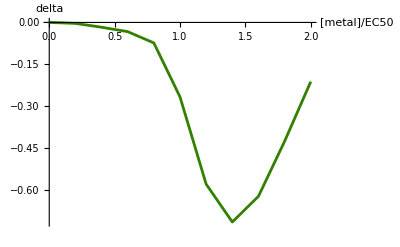

```mathematica
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

3.30906

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

1.5519

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

5.49297

#### NiZn growth data: a = 1.05***

```mathematica
ypad="YPAD";
single1="Ni";
single2="Zn";
double="NiZn";
```

```mathematica
minconc=0;
```

YPAD data

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],ypad]];
YPAD = Table[{minconc,minconc,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,0,1.4598},{0,0,1.4544},{0,0,1.4005},{0,0,1.4594},{0,0,1.4188},{0,0,1.5012},{0,0,1.4445},{0,0,1.5353},{0,0,1.5101},{0,0,1.5665}}

First metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single1]];
Metal1 = Table[{datafile[[rowtab[[j]],4]],0,datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{1.88,0,1.477},{1.88,0,1.4318},{2.4,0,1.469},{2.4,0,1.371},{3.,0,0.8652},{3.,0,0.9787},{3.6,0,0.5413},{3.6,0,0.5766},{5.1,0,0.0206},{5.1,0,0.005},{2.3,0,1.4688},{2.3,0,1.4886},{2.6,0,1.4167},{2.6,0,1.3268},{2.75,0,0.871},{2.75,0,0.926},{3.,0,0.5344},{3.,0,0.5202},{3.2,0,0.032},{3.2,0,0.0312}}

Second metal growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],single2]];
Metal2 = Table[{0,datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{0,4.,1.336},{0,4.,1.3572},{0,4.75,1.2102},{0,4.75,1.2322},{0,5.4,0.9341},{0,5.4,1.0006},{0,6.,0.6473},{0,6.,0.6677},{0,6.6,0.171},{0,6.6,0.1993},{0,3.33,1.2977},{0,3.33,1.3343},{0,4.,1.2007},{0,4.,1.2182},{0,4.8,0.9505},{0,4.8,0.9968},{0,5.4,0.685},{0,5.4,0.7097},{0,6.,0.3027},{0,6.,0.283}}

Combo growth rates

```mathematica
rowtab=Flatten[Position[datafile[[All,1]],double]];
Combo= Table[{datafile[[rowtab[[j]],4]],datafile[[rowtab[[j]],5]],datafile[[rowtab[[j]],rcol]]},{j,1,Length[rowtab]}]
```

{{1.88,4.,0.5877},{1.88,4.,0.657},{1.88,4.,0.6637},{2.4,4.75,0.1561},{2.4,4.75,0.1486},{2.4,4.75,0.149},{3.,5.4,0.0654},{3.,5.4,0.04},{3.,5.4,0.0527},{3.6,6.,0.0344},{3.6,6.,0.011},{3.6,6.,0.0164},{5.1,6.6,0.0138},{5.1,6.6,0.0079},{5.1,6.6,0.027},{2.3,3.33,0.5008},{2.3,3.33,0.5983},{2.3,3.33,0.5278},{2.6,4.,0.1325},{2.6,4.,0.1352},{2.6,4.,0.1647},{2.75,4.8,0.018},{2.75,4.8,0.0233},{2.75,4.8,0.0606},{3.,5.4,0.0187},{3.,5.4,0.0183},{3.,5.4,0.0182},{3.2,6.,0.0094},{3.2,6.,0.0033},{3.2,6.,0.0075}}

```mathematica
max1=Max[Combo[[All,1]]];(*Max concentration tested for plotting*)
max2=Max[Combo[[All,2]]];(*Max concentration tested for plotting*)
```

Here we use yeast growth rate data in the presence of two metals to estimate the parameters, comparing the observations to the Jonker et al. (2005) concentration addition model:

```mathematica
dataset=Join[YPAD,Metal1,Metal2,Combo];
MatrixForm[Transpose[dataset]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.88 | 1.88 | 2.4 | 2.4 | 3. | 3. | 3.6 | 3.6 | 5.1 | 5.1 | 2.3 | 2.3 | 2.6 | 2.6 | 2.75 | 2.75 | 3. | 3. | 3.2 | 3.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.88 | 1.88 | 1.88 | 2.4 | 2.4 | 2.4 | 3. | 3. | 3. | 3.6 | 3.6 | 3.6 | 5.1 | 5.1 | 5.1 | 2.3 | 2.3 | 2.3 | 2.6 | 2.6 | 2.6 | 2.75 | 2.75 | 2.75 | 3. | 3. | 3. | 3.2 | 3.2 | 3.2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4. | 4. | 4.75 | 4.75 | 5.4 | 5.4 | 6. | 6. | 6.6 | 6.6 | 3.33 | 3.33 | 4. | 4. | 4.8 | 4.8 | 5.4 | 5.4 | 6. | 6. | 4. | 4. | 4. | 4.75 | 4.75 | 4.75 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6. | 6.6 | 6.6 | 6.6 | 3.33 | 3.33 | 3.33 | 4. | 4. | 4. | 4.8 | 4.8 | 4.8 | 5.4 | 5.4 | 5.4 | 6. | 6. | 6.
1.4598 | 1.4544 | 1.4005 | 1.4594 | 1.4188 | 1.5012 | 1.4445 | 1.5353 | 1.5101 | 1.5665 | 1.477 | 1.4318 | 1.469 | 1.371 | 0.8652 | 0.9787 | 0.5413 | 0.5766 | 0.0206 | 0.005 | 1.4688 | 1.4886 | 1.4167 | 1.3268 | 0.871 | 0.926 | 0.5344 | 0.5202 | 0.032 | 0.0312 | 1.336 | 1.3572 | 1.2102 | 1.2322 | 0.9341 | 1.0006 | 0.6473 | 0.6677 | 0.171 | 0.1993 | 1.2977 | 1.3343 | 1.2007 | 1.2182 | 0.9505 | 0.9968 | 0.685 | 0.7097 | 0.3027 | 0.283 | 0.5877 | 0.657 | 0.6637 | 0.1561 | 0.1486 | 0.149 | 0.0654 | 0.04 | 0.0527 | 0.0344 | 0.011 | 0.0164 | 0.0138 | 0.0079 | 0.027 | 0.5008 | 0.5983 | 0.5278 | 0.1325 | 0.1352 | 0.1647 | 0.018 | 0.0233 | 0.0606 | 0.0187 | 0.0183 | 0.0182 | 0.0094 | 0.0033 | 0.0075)

Considering only Metal #1: Here we compare the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #1 (solid).

```mathematica
data1=Join[YPAD[[All,{1,3}]],Metal1[[All,{1,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{1.88,1.477},{1.88,1.4318},{2.4,1.469},{2.4,1.371},{3.,0.8652},{3.,0.9787},{3.6,0.5413},{3.6,0.5766},{5.1,0.0206},{5.1,0.005},{2.3,1.4688},{2.3,1.4886},{2.6,1.4167},{2.6,1.3268},{2.75,0.871},{2.75,0.926},{3.,0.5344},{3.,0.5202},{3.2,0.032},{3.2,0.0312}}

```mathematica
soln1=NonlinearModelFit[data1,{If[c1==0,max,max/(1+(c1/EC501)^β1)],0<EC501,max>0,β1>0},{max,EC501,β1},c1];
soln1["ParameterEstimates"]
soln1["BestFitParameters"]
Show[
ListPlot[data1],
Plot[Normal[soln1],{c1,0,max1}]
]
```

{max→1.49104,EC501→2.93571,β1→12.8529}

-Graphics-

Considering only Metal #2: Comparing the constrained model fit (nlm1, dashed) to the model allowing interactions (nlm2, dotted) to a fit to the data only considering the data in metal #2 (solid).

```mathematica
data2=Join[YPAD[[All,{1,3}]],Metal2[[All,{2,3}]]]
```

{{0,1.4598},{0,1.4544},{0,1.4005},{0,1.4594},{0,1.4188},{0,1.5012},{0,1.4445},{0,1.5353},{0,1.5101},{0,1.5665},{4.,1.336},{4.,1.3572},{4.75,1.2102},{4.75,1.2322},{5.4,0.9341},{5.4,1.0006},{6.,0.6473},{6.,0.6677},{6.6,0.171},{6.6,0.1993},{3.33,1.2977},{3.33,1.3343},{4.,1.2007},{4.,1.2182},{4.8,0.9505},{4.8,0.9968},{5.4,0.685},{5.4,0.7097},{6.,0.3027},{6.,0.283}}

```mathematica
soln2=NonlinearModelFit[data2,{If[c2==0,max,max/(1+(c2/EC502)^β2)],0<EC502,max>0,β2>0},{max,EC502,β2},c2];
soln2["ParameterEstimates"]
soln2["BestFitParameters"]
Show[
ListPlot[data2],
Plot[Normal[soln2],{c2,0,max2}]
]
```

{max→1.44066,EC502→5.51042,β2→8.06572}

-Graphics-

```mathematica
TRYmax=((max/.soln1["BestFitParameters"])+(max/.soln2["BestFitParameters"]))/2;
TRYEC501=EC501/.soln1["BestFitParameters"];
TRYβ1=β1/.soln1["BestFitParameters"];
TRYEC502=EC502/.soln2["BestFitParameters"];
TRYβ2=β2/.soln2["BestFitParameters"];
```

```mathematica
TRYparam={TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2}
```

{1.46585,2.93571,12.8529,5.51042,8.06572}

The above parameters from the single metal model fits will be used as starting values for the parameter searches below.

Model fit combined [no interaction]: This assumes no interaction in metal toxicity, just an independent reduction in growth rate (a=0)

For reference, the fit assuming a=0 and the single-metal parameters would be:

```mathematica
sumofsquares[TRYmax,TRYEC501,TRYβ1,TRYEC502,TRYβ2,dataset]
```

3.19581

Minimizing the sum of squares:

```mathematica
ssq=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2}}]
```

{2.5747,{max→1.52728,EC501→2.99338,β1→7.80217,EC502→5.60625,β2→3.73847}}

Maximizing the log likelihood:

```mathematica
maxll=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{σ,0.01,0,1}}]
```

{23.9367,{max→1.52728,EC501→2.99338,β1→7.80216,EC502→5.60625,β2→3.73847,σ→0.179398}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2}/.ssq[[2]])-({max,EC501,β1,EC502,β2}/.maxll[[2]]))/({max,EC501,β1,EC502,β2}/.maxll[[2]])
```

{-2.3908×10^-6,-5.27123×10^-6,0.00012779,0.0000123847,-0.0000915142}

Model fit combined [allowing an interaction]:

Minimizing the sum of squares:

```mathematica
ssqa=FindMinimum[{sumofsquares[max,EC501,β1,EC502,β2,a,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0}}]
```

{1.42407,{max→1.47881,EC501→2.9559,β1→10.,EC502→5.46393,β2→7.7536,a→1.08009}}

Maximizing the log likelihood:

```mathematica
maxlla=FindMaximum[{lnlikelihood[max,EC501,β1,EC502,β2,a,σ,dataset],0<max<2,0<EC501<Max[dataset[[All,1]]],0<β1<10,0<EC502<Max[dataset[[All,2]]],0<β2<10,-10<a<10},{{max,TRYmax},{EC501,TRYEC501},{β1,TRYβ1},{EC502,TRYEC502},{β2,TRYβ2},{a,0},{σ,0.04}}]
```

{47.6252,{max→1.47881,EC501→2.9559,β1→9.99999,EC502→5.46393,β2→7.7536,a→1.08009,σ→0.13342}}

The inferences from the minimizing the sum of squares or maximizing the log likelihood are similar (as they should be), as seen by % differences in the parameters that are <<1%:

```mathematica
100(({max,EC501,β1,EC502,β2,a}/.ssqa[[2]])-({max,EC501,β1,EC502,β2,a}/.maxlla[[2]]))/({max,EC501,β1,EC502,β2,a}/.maxlla[[2]])
```

{-4.05021×10^-6,-5.194×10^-7,0.00005632,2.08618×10^-6,0.0000344083,0.0000156432}

Testing whether adding the parameter “a” significantly improves the fit:

We use a likelihood ratio test to assess significance (see chapter 13 in https://users.stat.ufl.edu/~winner/sta4211/ALSM_5Ed_Kutner.pdf for alternative approaches using the sum of squares).

A log-likelihood ratio test would require that twice the difference in sum of squares should be more than χ_1^2=3.841, which it is:

```mathematica
1-CDF[ChiSquareDistribution[1],2(maxlla[[1]]-maxll[[1]])]
```

5.85632×10^-12

Without an interaction:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxll[[2]],0]]},{c1,0.01,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.01,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

With an interaction, the fit is much better:

```mathematica
Show[
ListPlot3D[Flatten[Table[{c1,c2,Chop[findY[{c1,c2},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]]},{c1,0.01,Max[dataset[[All,1]]]*1.2,Max[dataset[[All,1]]]/20},{c2,0.01,Max[dataset[[All,2]]]*1.2,Max[dataset[[All,2]]]/20}],1],AxesLabel->{StringJoin[{"[",single1,"]"}],StringJoin[{"[",single2,"]"}],"m"},PlotRange->{All,All,{0,Max[dataset[[All,3]]]}},PlotStyle->Opacity[0.5]],
ListPointPlot3D[dataset]
]
```

-Graphics3D-

Estimating delta for this function the x-axis measures concentrations in units of EC50:

{0,0.0000328473,0.0130526,0.308919,0.830982,0.952143,0.970739,0.975297,0.977579,0.979345,0.980908}

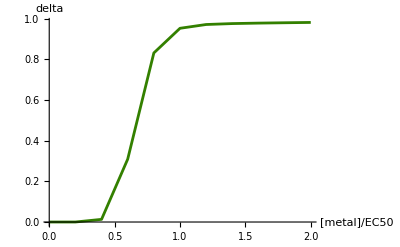

```mathematica
For[TRYc=0,TRYc≤2,TRYc=TRYc+1/5,
delta[TRYc]=Chop[1-2(findY[{TRYc EC501,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]/(findY[{TRYc EC501,0},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]+findY[{0,TRYc EC502},{max,EC501,β1,EC502,β2}/.maxlla[[2]],a/.maxlla[[2]]]))]
]
delta[double]=Table[delta[TRYc],{TRYc,0,2,1/5}]
Show[
ListPlot[Table[{c,delta[c]},{c,0,2,1/5}],Joined->True,PlotStyle->RGBColor[0.2,(0+2)/4,0]],
AxesLabel->{"[metal]/EC50","delta"}
]
```

```mathematica
a[double]=a/.maxlla[[2]]
```

1.08009

```mathematica
EC501[double]=EC501/.maxlla[[2]]
```

2.9559

```mathematica
EC502[double]=EC502/.maxlla[[2]]
```

5.46393

## Overall plots of a’s and delta’s

#### Model parameters

Table[a[doublelist[[i]]],{i,1,Length[doublelist]}]
Table[EC501[doublelist[[i]]],{i,1,Length[doublelist]}]
Table[EC502[doublelist[[i]]],{i,1,Length[doublelist]}]

```mathematica
doublelist={"CdCo","CdCu","CdMn","CdNi","CdZn","CoCu","CoMn","CoNi","CoZn","CuMn","CuNi","CuZn","MnNi","MnZn","NiZn"};
oldalist={-0.16207560765939727,-1.586796997134779,1.2528284963162748,0.8713577334340691,0.20364212368117826,-2.406461694324145,1.9322420937453406,0.8236100628124806,-0.017902299028275274,3.2526851042178415,-0.9788079808413033,-1.7573053558555443,2.244428525043177,2.678896184667141,1.049853881331315};
alist={0.8580314715680565,1.7472282355278907,0.8058570174216009,2.020113981706256,1.2587316235764356,-2.7965451989913728,2.0050204245196888,0.5899502659637897,-1.3192621128097115,2.903101073076883,-1.9091681797713087,-2.1936873839774713,2.0943186659682826,3.309056229360583,1.0800853978892053};
EClist1={0.010856402030976727,0.011792438304092774,0.010594870293785466,0.011159884509238365,0.012232092932777383,1.1134409295926295,1.0896651748799837,1.0892756869977303,1.1086580132356014,10.971005788706464,10.925976327369343,11.094025204960412,1.4097127365220836,1.551904738546649,2.9558956590046392};
EClist2={1.1043913827645155,11.201639220339036,1.508874746227782,2.9474993171018755,5.5641592355853415,11.05089429808391,1.4897902287883737,2.950052014136484,5.5208654407093425,1.4884359949403136,2.962846714821398,5.56279631545141,2.930321847223225,5.492965609735344,5.463930155614109};
```

```mathematica
Table[a[doublelist[[i]]]=alist[[i]],{i,1,Length[doublelist]}]
```

{0.858031,1.74723,0.805857,2.02011,1.25873,-2.79655,2.00502,0.58995,-1.31926,2.9031,-1.90917,-2.19369,2.09432,3.30906,1.08009}

```mathematica
Table[EC501[doublelist[[i]]]=EClist1[[i]],{i,1,Length[doublelist]}]
```

{0.0108564,0.0117924,0.0105949,0.0111599,0.0122321,1.11344,1.08967,1.08928,1.10866,10.971,10.926,11.094,1.40971,1.5519,2.9559}

```mathematica
Table[EC502[doublelist[[i]]]=EClist2[[i]],{i,1,Length[doublelist]}]
```

{1.10439,11.2016,1.50887,2.9475,5.56416,11.0509,1.48979,2.95005,5.52087,1.48844,2.96285,5.5628,2.93032,5.49297,5.46393}

```mathematica
Table[olda[doublelist[[i]]]=oldalist[[i]],{i,1,Length[doublelist]}];
```

```mathematica
lm=LinearModelFit[Table[{olda[doublelist[[i]]],a[doublelist[[i]]]},{i,1,15}],{x},x]
```

FittedModel[…]

```mathematica
Normal[lm]
```

0.246978+0.91189 x

```mathematica
lm["ParameterEstimates"]
```

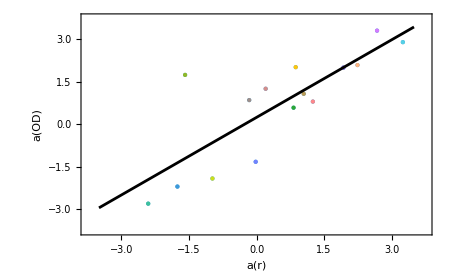

```mathematica
Show[
ListPlot[Table[Style[{olda[doublelist[[i]]],a[doublelist[[i]]]},color[doublelist[[i]]]],{i,1,15}],PlotRange->{{-3.75,3.75},{-3.75,3.75}},AxesLabel->{"a(r)","a(OD)"},PlotStyle->PointSize[Large]],
Plot[Normal[lm],{x,-3.5,3.5},PlotStyle->Black],
Frame->True]
```

```mathematica
delta["CdCo"]={0,0.059856807996265804,0.19828793990405713,0.3643312627172437,0.4879395229933077,0.5364692405307023,0.5619728175828946,0.6216233670356806,0.7042592071245461,0.7822477742166148,0.8441018154176366};
```

```mathematica
delta["CdCu"]={0,0.009753642180230115,0.07315689164617745,0.2112584010891354,0.36649011193548897,0.38871369867257055,0.3422308581265764,0.45467576823639855,0.6186196102128205,0.7505543149705496,0.8417735355562355};
```

```mathematica
delta["CdMn"]={0,0.08357699962945497,0.20687586948621683,0.30831041650189983,0.3754214241090226,0.41825912050215697,0.44942493365312997,0.47690310034713335,0.5041026198683634,0.5317747181159275,0.5595709669201772};
```

```mathematica
delta["CdNi"]={0,0.005942902807367201,0.055662925961483034,0.16963326382716037,0.2981942973211976,0.27971334205917864,0.17557058162748862,0.2765867999635562,0.46699917319450046,0.6343880268954805,0.7579169572141515};
```

```mathematica
delta["CdZn"]={0,0.01721213546870437,0.11185683373281885,0.30107469806534803,0.49810136174231945,0.5743324051233965,0.5950214954752718,0.6934436161390876,0.8009121485992041,0.8776392818230425,0.9261977914245737};
```

```mathematica
delta["CoCu"]={0,0.17117984202029102,0.9701644863970784,0.9984291333936146,0.9997851603975769,0.999932337386306,0.9999584766334262,0.9999663596807512,0.9999704910927342,0.9999734906229817,0.9999759692329723};
```

```mathematica
delta["CoMn"]={0,0.000514773337958907,0.02005899232288777,0.11585934634167905,0.2819659912391921,0.4066489385653098,0.4718020679371048,0.5236476368637282,0.5765747628345859,0.6273684440913694,0.6729082967294677};
```

```mathematica
delta["CoNi"]={0,0.0004177833059745284,0.05869508651196642,0.553360913798514,0.9050371175229182,0.9690366923239436,0.9806573024277991,0.9851797629937386,0.9882326192185494,0.9905266468420586,0.9922884775853317};
```

```mathematica
delta["CoZn"]={0,0.01629339007096764,0.678614230783009,0.973069157929786,0.9958305083255687,0.9985931863127786,0.9991145147385204,0.9992702149919827,0.9993471840851724,0.9994011738579376,0.9994457223998522};
```

```mathematica
delta["CuMn"]={0,-0.0006396451493286825,-0.006124322435797636,-0.010729505058986177,-0.002994190291300658,-0.08846528452750002,-0.24518307119713634,-0.20195133131448006,-0.01993144906823696,0.1743253981964813,0.33833177206823095};
```

```mathematica
delta["CuNi"]={0,0.01986586771765264,0.9060221960968492,0.997228000316343,0.9997649285013157,0.999944694024788,0.9999674707167154,0.9999726879055033,0.9999751338205245,0.9999769586461821,0.999978555389425};
```

```mathematica
delta["CuZn"]={0,0.038423019548315285,0.945151102162424,0.9983156624913412,0.9998464720872643,0.9999618558885534,0.9999770609724791,0.999979924561179,0.9999806160901402,0.9999808167567356,0.9999808838648755};
```

```mathematica
delta["MnNi"]={0,-0.00012842600595242004,0.004644933554873276,0.0711690909606576,0.2869116282689975,0.47053527176342547,0.5435651530016438,0.6363658129616481,0.7282138483040466,0.7984430088262426,0.8489196559444017};
```

```mathematica
delta["MnZn"]={0,-0.0034145510326180073,-0.017197222033129123,-0.03294659525771437,-0.07330479546711888,-0.2663998105190377,-0.5785863369961439,-0.7141257807798991,-0.622029127071253,-0.42525402131185297,-0.21186701205091696} ;
```

```mathematica
delta["NiZn"]={0,0.000032847289529791546,0.013052617507117392,0.3089190792503663,0.8309819844008246,0.9521429293407969,0.9707392238719778,0.975296620709807,0.9775794958751044,0.9793451954420171,0.980907749249755};
```

```mathematica
Join[{Flatten[{"Conc/EC50",Table[TRYc//N,{TRYc,0,2,1/5}]}]},
Table[Flatten[{doublelist[[i]],delta[doublelist[[i]]]}],{i,1,15}]];
(*Export["DeltaTable.csv",%];*)
```

Metal combo, estimated “a”, delta value at EC50:

```mathematica
Table[{doublelist[[i]],a[doublelist[[i]]],delta[doublelist[[i]]][[6]],EC501[doublelist[[i]]],EC502[doublelist[[i]]]},{i,1,15}];
Join[{{"Combo","a","delta[EC50]","EC501","EC502"}},%]//MatrixForm
Export["ParameterTableOD.csv",Join[{{"Combo","a","delta[EC50]","EC501","EC502"}},%%]];
```

(Combo | a | delta[EC50] | EC501 | EC502
CdCo | 0.858031 | 0.536469 | 0.0108564 | 1.10439
CdCu | 1.74723 | 0.388714 | 0.0117924 | 11.2016
CdMn | 0.805857 | 0.418259 | 0.0105949 | 1.50887
CdNi | 2.02011 | 0.279713 | 0.0111599 | 2.9475
CdZn | 1.25873 | 0.574332 | 0.0122321 | 5.56416
CoCu | -2.79655 | 0.999932 | 1.11344 | 11.0509
CoMn | 2.00502 | 0.406649 | 1.08967 | 1.48979
CoNi | 0.58995 | 0.969037 | 1.08928 | 2.95005
CoZn | -1.31926 | 0.998593 | 1.10866 | 5.52087
CuMn | 2.9031 | -0.0884653 | 10.971 | 1.48844
CuNi | -1.90917 | 0.999945 | 10.926 | 2.96285
CuZn | -2.19369 | 0.999962 | 11.094 | 5.5628
MnNi | 2.09432 | 0.470535 | 1.40971 | 2.93032
MnZn | 3.30906 | -0.2664 | 1.5519 | 5.49297
NiZn | 1.08009 | 0.952143 | 2.9559 | 5.46393)

The above rounded:

```mathematica
Table[{doublelist[[i]],1/100.*Round[100a[doublelist[[i]]]],1/100.*Round[100delta[doublelist[[i]]][[6]]],1/100.*Round[100EC501[doublelist[[i]]]],1/100.*Round[100EC502[doublelist[[i]]]]},{i,1,15}];
Join[{{"Combo","a","delta[EC50]","EC501","EC502"}},%]//MatrixForm
```

(Combo | a | delta[EC50] | EC501 | EC502
CdCo | 0.86 | 0.54 | 0.01 | 1.1
CdCu | 1.75 | 0.39 | 0.01 | 11.2
CdMn | 0.81 | 0.42 | 0.01 | 1.51
CdNi | 2.02 | 0.28 | 0.01 | 2.95
CdZn | 1.26 | 0.57 | 0.01 | 5.56
CoCu | -2.8 | 1. | 1.11 | 11.05
CoMn | 2.01 | 0.41 | 1.09 | 1.49
CoNi | 0.59 | 0.97 | 1.09 | 2.95
CoZn | -1.32 | 1. | 1.11 | 5.52
CuMn | 2.9 | -0.09 | 10.97 | 1.49
CuNi | -1.91 | 1. | 10.93 | 2.96
CuZn | -2.19 | 1. | 11.09 | 5.56
MnNi | 2.09 | 0.47 | 1.41 | 2.93
MnZn | 3.31 | -0.27 | 1.55 | 5.49
NiZn | 1.08 | 0.95 | 2.96 | 5.46)

Relationship between delta and a (from the fitted functions) for each metal at their EC50:

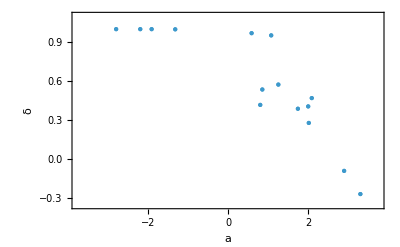

```mathematica
Show[
ListPlot[Table[Style[{a[doublelist[[i]]],delta[doublelist[[i]]][[6]]},color[doublelist[[i]]]],{i,1,15}],PlotRange->{{-3.75,3.75},{-0.35,1.1}},AxesLabel->{"a","δ"},PlotStyle->PointSize[Large]],
Frame->True]
```

Relationship between delta and a (from the fitted functions) for each metal at different fractions of their EC50 (numbers in the bottom left):

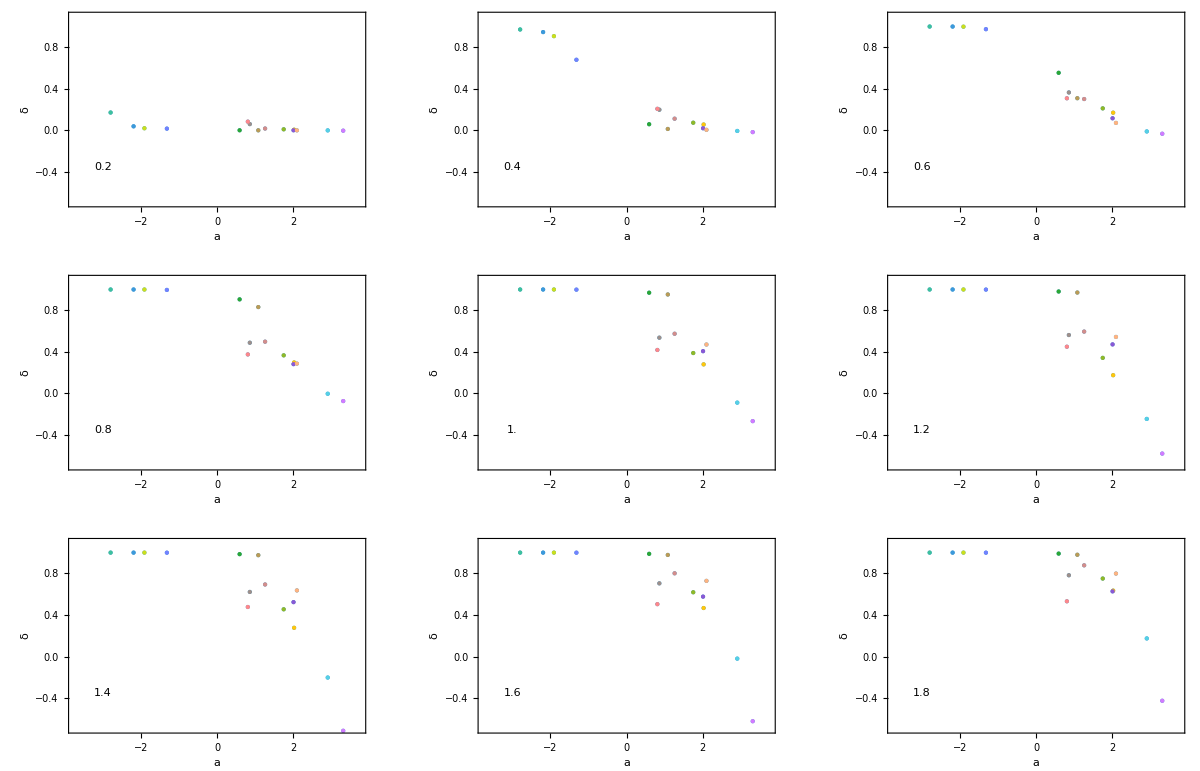

```mathematica
GraphicsGrid[Partition[Table[
Show[
ListPlot[Table[Style[{a[doublelist[[i]]],delta[doublelist[[i]]][[ii]]},color[doublelist[[i]]]],{i,1,15}],PlotRange->{{-3.75,3.75},{-0.7,1.1}},AxesLabel->{"a","δ"},PlotStyle->PointSize[Large]],
Graphics[Text[Round[10(ii-1)/5.]/10.,{-3,-0.35}]],
Frame->True],{ii,2,11}],3]]
```

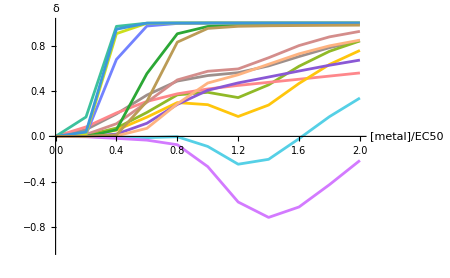

```mathematica
Show[
Table[ListPlot[Table[{(i-1)/5, delta[doublelist[[j]]][[i]]},{i,1,11}],Joined->True,PlotStyle->color[doublelist[[j]]]],{j,1,15}],PlotRange->{{0,2},{-1,1}},AxesLabel->{"[metal]/EC50","δ"},ImageSize->450
]
```

Legend ordered by delta

```mathematica
Sort[Table[{delta[doublelist[[i]]][[6]],Text[Style[doublelist[[i]],color[doublelist[[i]]]]]},{i,1,15}],#1[[1]]>#2[[1]]&][[All,2]]//MatrixForm
```

(CoCu
CuNi
CuZn
CoZn
NiZn
CoNi
CdCu
CdZn
CdNi
CdCo
CdMn
CoMn
MnNi
MnZn
CuMn)

```mathematica
Export["file.png",MatrixForm[%]];
```

Alphabetical order

```mathematica
Table[Text[Style[doublelist[[i]],color[doublelist[[i]]]]],{i,1,15}]//MatrixForm
```

(CdCo
CdCu
CdMn
CdNi
CdZn
CoCu
CoMn
CoNi
CoZn
CuMn
CuNi
CuZn
MnNi
MnZn
NiZn)